```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/Rydberg Custom Gates Custom SWAP.wl"]; (*Configuration File*)
data=Import["/Users/questuser/Documents/Kathryn/SU4Gates9Qubits.csv"]; (*Imported gates from Qiskit*)
(*Import["C:\\Users\\KitKa\\QuESTlink\\Link\\QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["C:\\Users\\KitKa\\QuESTlink\\quest_link.exe"];(*Creating QuEST environment*)Import["C:\\Users\\KitKa\\QuESTlink\\Rydberg Custom Gates Custom SWAP.wl"];(*Configuration File*)data=Import["C:\\Users\\KitKa\\OneDrive\\Documents\\Wolfram Mathematica\\SU4Gates9Qubits.csv"];*)
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}],
(* blockade radius in μm*)
BlockadeRadius->10,
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 100,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[InitLocations]
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

-Graphics3D-

```mathematica
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure*)

MeasErrors[QubitList_]:=Table[Subscript[U,QubitList[[i]]][{{0.9997,0},{0,1.0003}}],{i,1,Length[QubitList]}]
```

```mathematica
KetList[3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]

-Graphics-

U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]

{X_0,X_1,X_2,H_0,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}],X_0,H_0,X_0,X_1,X_2}

{X_0,X_1,X_2,H_0,X_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}],X_0,H_0,X_0,X_1,X_2}

{H_0,U_(0,1,2)[{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}],H_0}

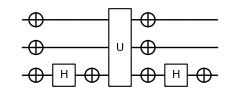

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0)

-Graphics-

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

```mathematica
Toff=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
DrawCircuit[{Toff}]
CCZ=Subscript[U, 0,1,2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]
CCZCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],Toff,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
ToffCirc={Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[H, 0],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2]}
CCZClifCirc={Subscript[H, 0],Toff,Subscript[H, 0]}(*{Subscript[X,1],Subscript[X,2],Subscript[X, 0],CCZ,Subscript[X, 0],Subscript[X,1],Subscript[X,2]}*)
DrawCircuit[ToffCirc]
CalcCircuitMatrix[{Toff}]//MatrixForm
CalcCircuitMatrix[ToffCirc]//MatrixForm
DrawCircuit[CCZCirc]
CalcCircuitMatrix[{CCZ}] //MatrixForm
CalcCircuitMatrix[CCZCirc] // MatrixForm
CalcCircuitMatrix[CCZClifCirc]//MatrixForm
```

```mathematica
{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

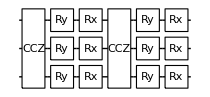
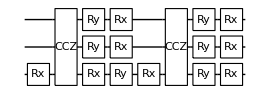
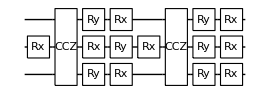
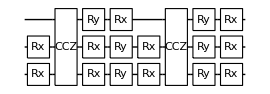
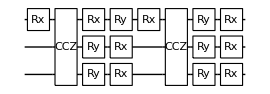
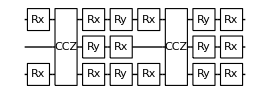
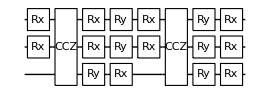
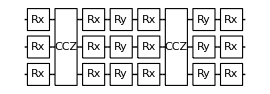

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

{{0.933367,0.00773659,0.00773659,0.00771312,0.00773659,0.00771312,0.00771312,0.00776832},{0.00773795,0.933358,0.00771387,0.00773902,0.00771387,0.00773902,0.00776899,0.00771382},{0.00773795,0.00771387,0.933358,0.00773902,0.00771387,0.00776899,0.00773902,0.00771382},{0.00771367,0.00773771,0.00773771,0.93336,0.0077688,0.00771362,0.00771362,0.00773877},{0.00773795,0.00771387,0.00771387,0.00776899,0.933358,0.00773902,0.00773902,0.00771382},{0.00771367,0.00773771,0.0077688,0.00771362,0.00773771,0.93336,0.00771362,0.00773877},{0.00771367,0.0077688,0.00773771,0.00771362,0.00773771,0.00771362,0.93336,0.00773877},{0.0077685,0.00771333,0.00771333,0.00773682,0.00771333,0.00773682,0.00773682,0.933365}}

```mathematica
InitCirc[NQ_]:=Table[Subscript[Init, b],{b,0,NQ-1,1}]
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed],1]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]
Table[DrawCircuit[GroverIteration3Q[KetList[3][[i]]]],{i,1,8}]
KetList[3]
GroversAlg3Q=Table[SearchSeeds=KetList[3];
ρ=CreateDensityQureg[9];
(*InitZeroState[ρ];*)
InitialisationCirc=ExtractCircuit[GetCircuitSchedule[Join[InitCirc[3],HTrans[0],HTrans[1],HTrans[2]],RydDev,ReplaceAliases->True]];
ApplyCircuit[ρ,InitialisationCirc];
Gr=ExtractCircuit[InsertCircuitNoise[GroverIteration3Q[SearchSeeds[[i]]],RydDev,ReplaceAliases->True]];
ApplyCircuit[ρ,Join[Gr,Gr]];CalcProbOfAllOutcomes[ρ,{0,1,2}],{i,1,8}]

DestroyAllQuregs[];
```

```mathematica
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
ToffSandBread[t_,c1_,c2_]:={Subscript[Ry, t][-Pi/2],Subscript[Rx, t][-Pi],Subscript[Rx, c1][Pi],Subscript[Rx, c2][Pi]}
```

```mathematica
Toff[t_,c1_,c2_]:=Subscript[U, t,c1,c2][{{1,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0}}]
CCZGate[t_,c1_,c2_]:=Subscript[U, t,c1,c2][{{1,0,0,0,0,0,0,0},{0,-1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,0,0,-1,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,0,0,-1,0},{0,0,0,0,0,0,0,-1}}]
```

```mathematica
ToffRyd[t_,c1_,c2_]:={{Subscript[X, t],Subscript[X, c1],Subscript[X, c2],Subscript[H, t],Subscript[X, t],CCZGate[t,c1,c2],Subscript[X, t],Subscript[H, t],Subscript[X, t],Subscript[X, c1],Subscript[X, c2]}}
```

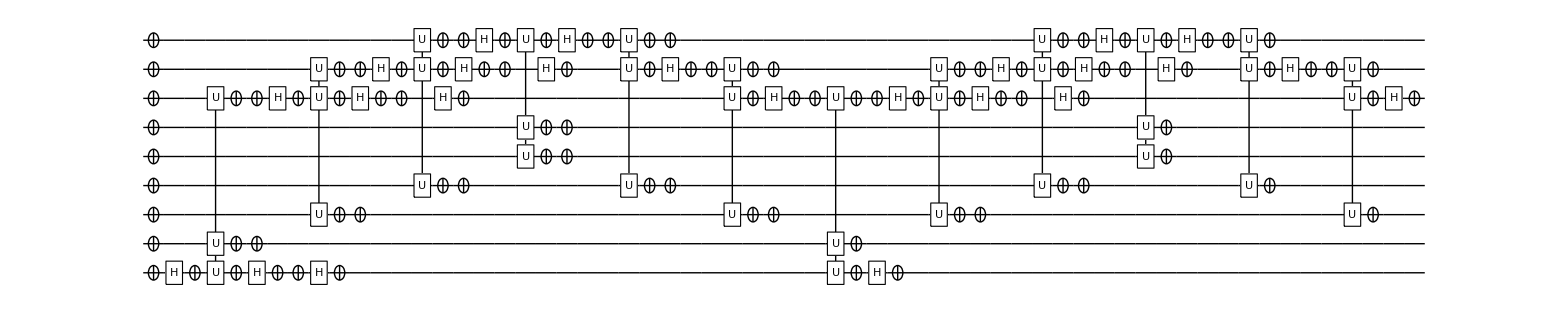

0

```mathematica
(*C4ZMat=DiagonalMatrix[Join[{1},Table[-1,{i,1,2^5-1}]]];
C4XMat=CalcCircuitMatrix[{Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4ZMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]}];
C4XCirc={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4ZMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]};
C4ZCirc={Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[U, 0,1,2,3,4][C4XMat],Subscript[X, 0],Subscript[H, 0],Subscript[X, 0],Subscript[X, 1],Subscript[X, 2],Subscript[X, 3],Subscript[X, 4]};
C4XCircToff={Toff[0,6,1],Toff[6,7,2],Toff[7,8,3],Toff[8,4,5],Toff[7,8,3],Toff[6,7,2],Toff[0,6,1],Toff[6,7,2],Toff[7,8,3],Toff[8,4,5],Toff[7,8,3],Toff[6,7,2]};*)
C4XCircCCZ=Flatten[{ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2]}];
DrawCircuit[C4XCircCCZ]
Length[C5ZMat]
```

```mathematica
?Delete
```

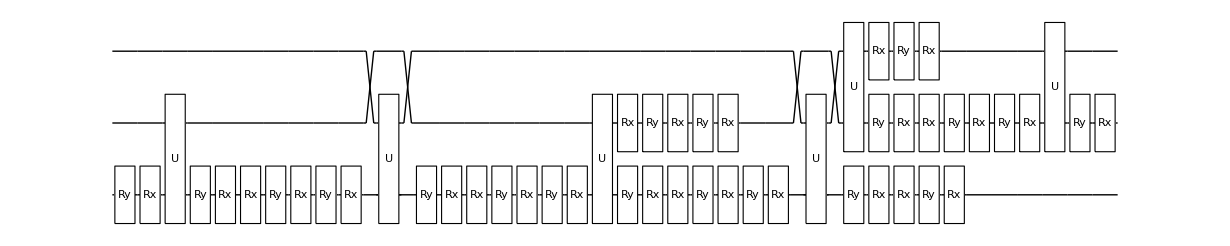

```mathematica
XTrans[i_]:={Subscript[Rx, i][Pi]};
HTrans[i_]:={Subscript[Ry, i][Pi/2],Subscript[Rx, i][Pi]};
HXTrans[q_]:=Subscript[Ry, q][Pi/2]
XHTrans[q_]:=Subscript[Ry, q][-Pi/2]
XHXTrans[q_]:={Subscript[Ry, q][-Pi/2],Subscript[Rx, q][-Pi]}
HXHTrans[q_]:={Subscript[Ry, q][-Pi],Subscript[Rx, q][-Pi]}
TGate[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][-Pi/4],Subscript[Rx, t][-Pi/2]}
Tdg[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][Pi/4],Subscript[Rx, t][-Pi/2]}
Subscript[CCZDecomp,t_,c1_,c2_]:=Flatten[{XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t], Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],XHXTrans[t],Subscript[CZG, t,c1],XHXTrans[t],Tdg[t],XHXTrans[t],Subscript[CZG, t,c2],XHXTrans[t],TGate[t],TGate[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1],TGate[c2],Tdg[c1],XHXTrans[c1],Subscript[CZG, c1,c2],XHXTrans[c1]}]
DrawCircuit[ExtractCircuit[GetCircuitSchedule[Subscript[CCZDecomp, 0,1,2],RydDev,ReplaceAliases->True]]]
```

```mathematica
XHXTra
```

```mathematica
KetList[5][[1]][[2;;]]
```

{0,0,0,0}

```mathematica
CliffCCZRyd={HXTrans[0],HXTrans[0],Table[XTrans[i],{i,1,8}],Subscript[CCZ, 0,6,1],HXTrans[6],Subscript[CCZ, 7,6,2],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,5,4] XHTrans[8],Subscript[CCZ, 8,7,3]}
GroverIteration3Q[SearchSeed_]:=Module[{XIndices=Join[Position[Reverse[SearchSeed][[1]],1],Position[Reverse[SearchSeed][[2;;]],0]]},
Xs=Table[XTrans[XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
Flatten[{Xs,Subscript[CCZ, 0,1,2],Xs,HTrans[0],HTrans[1],HTrans[2],Subscript[CCZ, 0,1,2],HTrans[0],HTrans[1],HTrans[2]}]]
```

```mathematica
?Replace
```

```mathematica
Print[KetList[6][[1]]]
C5XTranspiled=Flatten[{Table[XTrans[i],{i,1,8}],XTrans[0],HXTrans[0],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],,XHTrans[0],XTrans[0],Table[XTrans[i],{i,1,8}]}];
C5ZCliffTrans=Join[HTrans[0],C5XTranspiled,HTrans[0]];

GroverOracle6D3A[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]
GroverDiffusion6D3A=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZ, 8,7,3],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Subscript[CCZ, 0,1,6],HXTrans[6],Subscript[CCZ, 2,6,7],HXTrans[7],Subscript[CCZ, 3,7,8],HXTrans[8],Subscript[CCZ, 4,5,8],XHTrans[8],Subscript[CCZ, 3,8,7],XHTrans[7],Subscript[CCZ, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];
```

```mathematica
RenormList2Q=Table[{},{i,1,64}]

GroverOracle6D3A2Q[SearchSeed_]:=Module[{XIndices=Position[Reverse[SearchSeed][[2;;]],1]},
If[Reverse[SearchSeed][[1]]==0,XStart={XTrans[0],HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0],XTrans[0]},
XStart={HXTrans[0],HXTrans[0]};XEnd={XHTrans[0],XHTrans[0]}];
Xs=Flatten[Table[XTrans[XIndices[[j,1]]],{j,1,Length[XIndices]}]];
(*Print[Xs];*)
Flatten[{XStart,Xs,Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZDecomp, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Xs,XEnd}]]

GroverDiffusion6D3A2Q=Flatten[{Table[HTrans[i],{i,0,5}],Table[XTrans[i],{i,6,8}],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 8,7,3],HXTrans[8],Subscript[CCZ, 8,4,5],XHTrans[8],Subscript[CCZDecomp, 8,7,3],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Subscript[CCZDecomp, 0,1,6],HXTrans[6],Subscript[CCZDecomp, 2,6,7],HXTrans[7],Subscript[CCZDecomp, 3,7,8],HXTrans[8],Subscript[CCZDecomp, 4,5,8],XHTrans[8],Subscript[CCZDecomp, 3,8,7],XHTrans[7],Subscript[CCZDecomp, 2,6,7],XHTrans[6],Table[XTrans[i],{i,6,8}],Table[HTrans[i],{i,0,5}]}];

GroverAlg6D3A2Q[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A2Q[SearchSeed],GroverDiffusion6D3A2Q},{j,1,8}]]]

GroverAlg6D3AVaryIt2Q[SearchSeed_]:=Flatten[{GroverOracle6D3A2Q[SearchSeed],GroverDiffusion6D3A2Q}]
Init9=Table[Subscript[Init, i],{i,0,8}];
GroverDataUnNormCZVaryIt=Table[SearchSeed=KetList[6][[j]];
ρ=CreateDensityQureg[9];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Flatten[{Init9,Table[HTrans[i],{i,0,5}]}],RydDev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroverAlg6D3AVaryIt2Q[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList2Q[[j]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,8}],{j,1,64}];

RenormDataVaryIt2Q=Table[{j,Mean[RenormList2Q[[All,j]]],StandardDeviation[RenormList[[All,j]]]/8},{j,1,8}]
GroverDataUnnormVaryIt2Q=Table[{j,Mean[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]]±StandardDeviation[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]]/8},{j,1,8}]
GroverDataRenormVaryIt2Q=Table[{j,Mean[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]/RenormList2Q[[All,j]]]±StandardDeviation[Diagonal[GroverDataUnNormCZVaryIt[[All,j]]]/RenormList2Q[[All,j]]]/8},{j,1,8}]
PLossVaryIt2Q=Table[{i,(1-RenormDataVaryIt2Q[[i,2]])±RenormDataVaryIt2Q[[i,3]]},{i,1,8}]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

{{1,0.734217,3.58139×10^-9},{2,0.574485,7.81235×10^-9},{3,0.451123,1.15293×10^-8},{4,0.355585,1.43823×10^-8},{5,0.281647,1.68222×10^-8},{6,0.223596,1.9897×10^-8},{7,0.177656,2.43859×10^-8},{8,0.140988,3.02922×10^-8}}

{{1,0.0979423±0.000436605},{2,0.195315±0.00107253},{3,0.258081±0.00161728},{4,0.273696±0.00182908},{5,0.247097±0.00162908},{6,0.195319±0.00115516},{7,0.136402±0.000801417},{8,0.0836495±0.00096609}}

{{1,0.133399±0.000600386},{2,0.340015±0.00195702},{3,0.572281±0.00401965},{4,0.770283±0.00622863},{5,0.878387±0.00757872},{6,0.874709±0.00704773},{7,0.768289±0.00471901},{8,0.592366±0.0047116}}

{{1,0.265783±3.58139×10^-9},{2,0.425515±7.81235×10^-9},{3,0.548877±1.15293×10^-8},{4,0.644415±1.43823×10^-8},{5,0.718353±1.68222×10^-8},{6,0.776404±1.9897×10^-8},{7,0.822344±2.43859×10^-8},{8,0.859012±3.02922×10^-8}}

```mathematica
RenormDataVaryIt2Q={{1,0.7342165303021817,3.5813907106676723*^-9},{2,0.5744849340982545,7.812354455277304*^-9},{3,0.451123347756977,1.1529312939099698*^-8},{4,0.3555850135878708,1.4382338013567163*^-8},{5,0.28164688968026624,1.6822226100152315*^-8},{6,0.22359555509350898,1.9897023196452725*^-8},{7,0.17765624753819118,2.438590391602956*^-8},{8,0.14098756136335625,3.029224370795262*^-8}}
PLossVaryIt2Q=Table[{i,(1-RenormDataVaryIt2Q[[i,2]])±RenormDataVaryIt2Q[[i,3]]},{i,1,8}]
```

{{1,0.734217,3.58139×10^-9},{2,0.574485,7.81235×10^-9},{3,0.451123,1.15293×10^-8},{4,0.355585,1.43823×10^-8},{5,0.281647,1.68222×10^-8},{6,0.223596,1.9897×10^-8},{7,0.177656,2.43859×10^-8},{8,0.140988,3.02922×10^-8}}

{{1,0.265783±3.58139×10^-9},{2,0.425515±7.81235×10^-9},{3,0.548877±1.15293×10^-8},{4,0.644415±1.43823×10^-8},{5,0.718353±1.68222×10^-8},{6,0.776404±1.9897×10^-8},{7,0.822344±2.43859×10^-8},{8,0.859012±3.02922×10^-8}}

```mathematica
DestroyAllQuregs[];
```

```mathematica
DestroyAllQuregs[];
```

```mathematica
RenormList=Table[{},{i,1,64}]

(*GroversAlg6D3A[SearchSeed_]:=Flatten[Join[Table[HTrans[i],{i,0,5}],Table[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A},{j,1,8}]]]*)
(*GroverDataUnNormCCZ=Table[If[IntegerQ[i/8],Print[i]];SearchSeed=KetList[6][[i]];
ρ=CreateDensityQureg[9];
InitZeroState[ρ];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3A[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
RenormList[[i]]=Renorm;
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,64}];
*)
RenormList=Table[{},{i,1,64}];
Init9=Table[Subscript[Init, i],{i,0,8}];
GroversAlg6D3AVaryIt[SearchSeed_]:=Flatten[{GroverOracle6D3A[SearchSeed],GroverDiffusion6D3A}]
GroverDataUnNormCCZVaryIt=Table[SearchSeed=KetList[6][[j]];
ρ=CreateDensityQureg[9];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Flatten[{Init9,Table[HTrans[i],{i,0,5}]}],RydDev,ReplaceAliases->True]]];
Table[ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[GroversAlg6D3AVaryIt[SearchSeed],RydDev,ReplaceAliases->True]]];
Renorm=Total[CalcProbOfAllOutcomes[ρ,Range[0,8]]];
AppendTo[RenormList[[j]],Renorm];
CalcProbOfAllOutcomes[ρ,{0,1,2,3,4,5}],{i,1,8}],{j,1,64}];

RenormDataVaryIt=Table[{j,Mean[RenormList[[All,j]]]±StandardDeviation[RenormList[[All,j]]]/8},{j,1,8}]
GroverDataUnnormVaryIt=Table[{j,Mean[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]]±StandardDeviation[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]]/8},{j,1,8}]
GroverDataRenormVaryIt=Table[{j,Mean[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]/RenormList[[All,j]]]±StandardDeviation[Diagonal[GroverDataUnNormCCZVaryIt[[All,j]]]/RenormList[[All,j]]]/8},{j,1,8}]

(*DrawCircuit[GroverOracle6D3A[KetList[6][[1]]]]
DrawCircuit[ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]]*)
(*ExtractCircuit[GetCircuitSchedule[C5XTranspiled,RydDev,ReplaceAliases->True]]*)
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

{{1,0.851566±3.58139×10^-9},{2,0.771403±7.81235×10^-9},{3,0.698231±1.15293×10^-8},{4,0.63209±1.43823×10^-8},{5,0.572745±1.68222×10^-8},{6,0.519781±1.9897×10^-8},{7,0.472587±2.43859×10^-8},{8,0.430312±3.02922×10^-8}}

{{1,0.113192±4.14217×10^-8},{2,0.262305±1.69378×10^-7},{3,0.408768±3.70746×10^-7},{4,0.513002±5.9389×10^-7},{5,0.549389±7.63541×10^-7},{6,0.516784±8.25608×10^-7},{7,0.427288±7.49598×10^-7},{8,0.307742±5.58081×10^-7}}

{{1,0.132922±4.81461×10^-8},{2,0.340036±2.1661×10^-7},{3,0.585434±5.22789×10^-7},{4,0.811596±9.23773×10^-7},{5,0.959222±1.30839×10^-6},{6,0.994234±1.55395×10^-6},{7,0.904146±1.54327×10^-6},{8,0.715161±1.25049×10^-6}}

```mathematica
RenormDataVaryIt={{1,0.851566298944711,3.5813907106676723*^-9},{2,0.7714033226306559,7.812354455277304*^-9},{3,0.6982306826239474,1.1529312939099698*^-8},{4,0.6320903692286575,1.4382338013567163*^-8},{5,0.5727445243425613,1.6822226100152315*^-8},{6,0.5197814141978313,1.9897023196452725*^-8},{7,0.4725871535890921,2.438590391602956*^-8},{8,0.4303121329096925,0.3029224370795262*^-8}}
PLossVaryIt=Table[{i,(1-RenormDataVaryIt[[i,2]])±RenormDataVaryIt[[i,3]]},{i,1,8}]
```

{{1,0.851566,3.58139×10^-9},{2,0.771403,7.81235×10^-9},{3,0.698231,1.15293×10^-8},{4,0.63209,1.43823×10^-8},{5,0.572745,1.68222×10^-8},{6,0.519781,1.9897×10^-8},{7,0.472587,2.43859×10^-8},{8,0.430312,3.02922×10^-9}}

{{1,0.148434±3.58139×10^-9},{2,0.228597±7.81235×10^-9},{3,0.301769±1.15293×10^-8},{4,0.36791±1.43823×10^-8},{5,0.427255±1.68222×10^-8},{6,0.480219±1.9897×10^-8},{7,0.527413±2.43859×10^-8},{8,0.569688±3.02922×10^-9}}

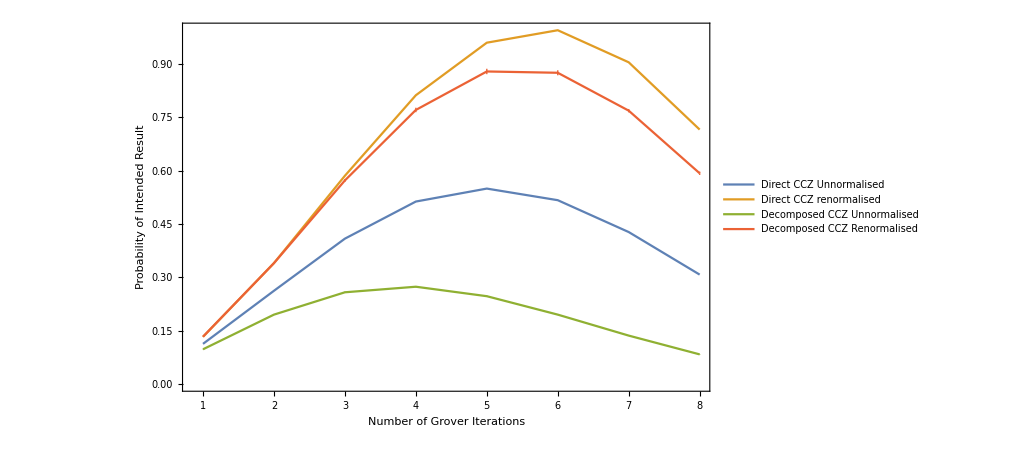

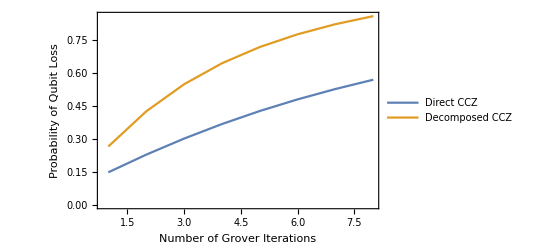

```mathematica
ListLinePlot[{GroverDataUnnormVaryIt,GroverDataRenormVaryIt,GroverDataUnnormVaryIt2Q,GroverDataRenormVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],FrameLabel->{"Number of Grover Iterations","Probability of Intended Result"},PlotRange->All,PlotLegends->{"Direct CCZ Unnormalised","Direct CCZ renormalised","Decomposed CCZ Unnormalised","Decomposed CCZ Renormalised"}]
ListLinePlot[{PLossVaryIt,PLossVaryIt2Q},Frame->True,LabelStyle->Directive[Bold, Medium],FrameLabel->{"Number of Grover Iterations","Probability of Qubit Loss"},PlotRange->All,PlotLegends->{"Direct CCZ","Decomposed CCZ"}]
```

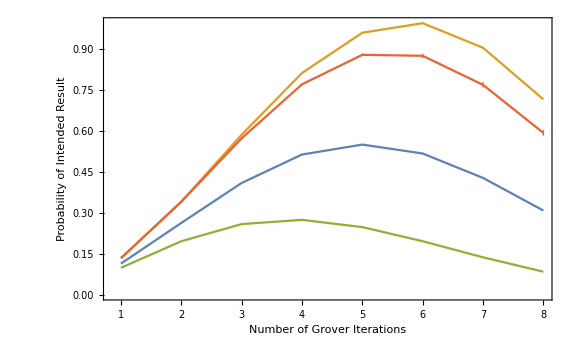

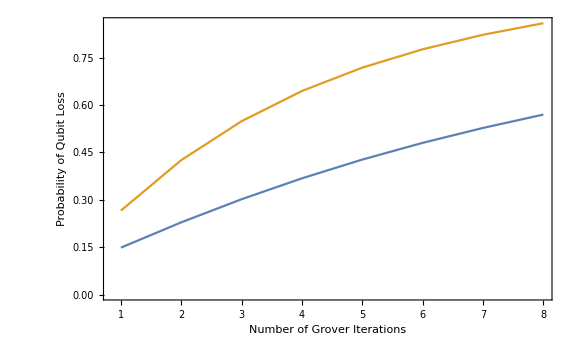

```mathematica
RenormList
```

{0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458396,0.458395,0.458395,0.458395,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458396,0.458396,0.458396,0.458395,0.458395,0.458395,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458395,0.458396,0.458395,0.458395,0.458396,0.458396,0.458396,0.458395,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396,0.458396}

```mathematica
ρ=CreateQureg[9]

Table[InitZeroState[ρ];InputState=KetList[6][[i]];
XIndices=Position[Reverse[InputState],1];
Xs=Table[Subscript[X,XIndices[[j,1]]-1],{j,1,Length[XIndices]}];
ApplyCircuit[ρ,Xs];
ApplyCircuit[ρ,ExtractCircuit[GetCircuitSchedule[Subscript[CCZDecomp, 0,1,2](*GroverOracle6D3A[InputState[1]]*)(*C5XTranspiled*)(*C5ZTrans*),RydDev,ReplaceAliases->True]]];
(*GetAmp[ρ,i-1,i-1]*)Chop[GetQuregMatrix[ρ][[1;;2^3]]],{i,1,8}]//MatrixForm
(*C5XCircCCZ=Flatten[{Table[HTrans[i],{i,0,5}],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],ToffRyd[0,6,1],ToffRyd[6,7,2],ToffRyd[7,8,3],ToffRyd[8,4,5],ToffRyd[7,8,3],ToffRyd[6,7,2],Table[HTrans[i],{i,0,5}]}];*)
DestroyAllQuregs[];
```

0

(-0.92388-0.382683 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.92388+0.382683 ⅈ)

```mathematica
?QuEST`*
```

```mathematica
?Round
```

```mathematica
Sqrt[64]
```

```mathematica
CCZDecomp[t_,c1_,c2_]:=
```

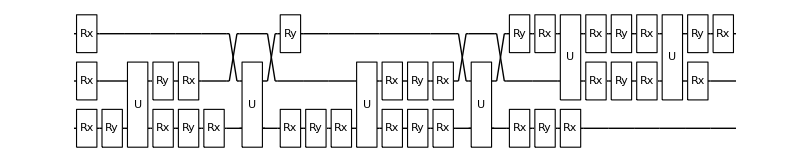

{Rx_1[-1.981],Rx_2[-2.6423],Ry_1[π/2],Ry_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[π/4],Rx_0[-π/2],Rx_1[π/2],Ry_1[3.0061],Rx_1[π/2],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[-π/2],Rx_2[-π/2],Rx_2[2.702],Rx_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[(3 π)/4],Rx_1[-2.7048],Ry_1[0.89527],Rx_0[π/2],Rx_1[0.92944],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[π/2],Rx_2[-π/2],Ry_2[0.93891],CZG_(1,2),Rx_1[π/2],Ry_1[π/2],Rx_1[π/2],Rx_2[π/4],Ry_2[π/2],Rx_2[-π/2],CZG_(1,2),Rx_1[-π/2],Ry_1[π/4],Rx_1[-π/2],Rx_2[π/2]}

{Rx_1[-1.981],Rx_2[-2.6423],Ry_1[π/2],Ry_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[π/4],Rx_0[-π/2],Rx_1[π/2],Ry_1[3.0061],Rx_1[π/2],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[-π/2],Rx_2[-π/2],Ry_2[2.702],Rx_2[π/2],CZG_(0,1),Rx_0[π/2],Ry_0[(3 π)/4],Rx_1[-2.7048],Ry_1[0.89527],Rx_0[π/2],Rx_1[0.92944],CZG_(0,2),Rx_0[-π/2],Ry_0[π/4],Rx_0[π/2],Rx_2[-π/2],Ry_2[0.93891],CZG_(1,2),Rx_1[π/2],Ry_1[π/2],Rx_1[π/2],Rx_2[π/4],Ry_2[π/2],Rx_2[-π/2],CZG_(1,2),Rx_1[-π/2],Ry_1[π/4],Rx_1[-π/2],Rx_2[π/2]}

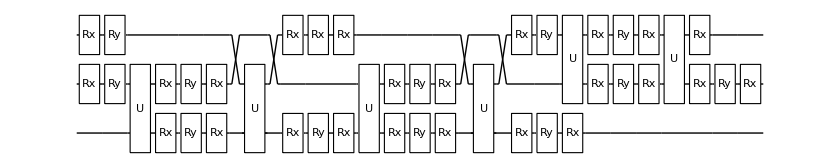

InsertCircuitNoise::error: Encountered gate CZ_(0,1) which is not supported by the given device specification. Note this may be due to preceding gates, if the spec contains constraints which depend on dynamic variables. See ?GetUnsupportedGates.

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

CalcCircuitMatrix::error: Invalid arguments. See ?CalcCircuitMatrix

```mathematica
TGate[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][-Pi/4],Subscript[Rx, t][-Pi/2]}
Tdg[t_]:={Subscript[Rx, t][Pi/2],Subscript[Ry, t][Pi/4],Subscript[Rx, t][-Pi/2]}






{Subscript[Rx, t][-0.09065988720074536],Subscript[Ry, t][-Pi/2],Subscript[Rx, c1][-Pi],Subscript[Rx, c2][-Pi],Subscript[CZG, t,c1],Subscript[Rx, t][-0.800360109933159],Subscript[Ry, t][1.372292382481866],Subscript[Rx, t][1.63614359593572],Subscript[Ry, c1][-Pi],Subscript[Rx, c1][-Pi],Subscript[CZG, t,c2],Subscript[Rx, t][2.3583],Subscript[Ry, t][0.82493],Subscript[Rx, t][-2.7641],Subscript[Ry, c2][Pi],Subscript[CZG, t,c1],Subscript[Rx, t][-0.12796],Subscript[Ry, t][0.68257],Subscript[Rx, t][-2.5412],Subscript[Rx, c1][-π/2],Subscript[Ry, c1][Pi/4],Subscript[Rx, c1][-π/2],Subscript[CZG, t,c2],Subscript[Rx, t][-2.7055],Subscript[Ry, t][2.2467],Subscript[Rx, t][2.211],Subscript[Ry, c2][-π/2],Subscript[Rx, c2][Pi/2],Subscript[CZG, c1,c2],Subscript[Rx, c1][π/2],Subscript[Ry, c1][Pi/2],Subscript[Rx, c1][Pi/2],Subscript[Rx, c2][Pi/4],Subscript[Ry, c2][Pi/2],Subscript[Rx, c2][-Pi/2],Subscript[CZG, c1,c2],Subscript[Rx, c1][-Pi],Subscript[Ry, c2][-Pi/4],Subscript[Rx, c2][-Pi/2]};

DrawCircuit[ExtractCircuit[GetCircuitSchedule[CCZDecomp[0,1,2],RydDev,ReplaceAliases->True]]]//MatrixForm
```

```mathematica
?QuEST`*
```

```mathematica
RenormData2Q={{1,0.13852374960646902},{2,0.1427740470574978},{3,0.14098146173702925},{4,0.14541921091648913},{5,0.1491950028378024},{6,0.15305986367162278},{7,0.15095078115847713},{8,0.1540637895045909},{9,0.1427950885306636},{10,0.14692466464018472},{11,0.14495788478278998},{12,0.14883686786480266},{13,0.15312977688050067},{14,0.15624019772223394},{15,0.1539521063885762},{16,0.15614767425220785},{17,0.14034909135296553},{18,0.14469389068584682},{19,0.14289041870511926},{20,0.14725651032298173},{21,0.15110239623450078},{22,0.15475210246228646},{23,0.15265768988380213},{24,0.15545801670424697},{25,0.14469559064288767},{26,0.14875835588304265},{27,0.14681013666556036},{28,0.15046743952265768},{29,0.15490061458939697},{30,0.15768318563592293},{31,0.15544865775101788},{32,0.1572874483036231},{33,0.13988262097587953},{34,0.1443028214655081},{35,0.14237187850664762},{36,0.14690192757333334},{37,0.1507419445258296},{38,0.15466292276914376},{39,0.1523699587842461},{40,0.15544051477096846},{41,0.14419198238638598},{42,0.1484407016994882},{43,0.14634053363705576},{44,0.15024754538990784},{45,0.1546339622475812},{46,0.15773276174763246},{47,0.15527690739580038},{48,0.15738284630687466},{49,0.1417795189159077},{50,0.1462631985112232},{51,0.144321540863814},{52,0.1487393329901067},{53,0.15267952817921407},{54,0.15634761122411858},{55,0.15407031938711363},{56,0.15679798218817595},{57,0.14612935879120603},{58,0.15027365068219659},{59,0.1481934591435216},{60,0.15183951953597827},{61,0.15640266215466464},{62,0.15914347754535565},{63,0.15674486772683877},{64,0.15847580562835273}};
```

```mathematica
GroverDataUnNormCZ={{0.07151673312187562,0.0016296439763250005,0.001707977259928407,0.0012383318665644943,0.0009760928305335871,0.0010044666954828487,0.0009678780313693899,0.0008701398092486181,0.0011861714345121157,0.0009952603758105196,0.0012349991077716205,0.0009968259846651053,0.0011432330158967713,0.0009562603666942685,0.0010376352073526618,0.0009055336967500919,0.0012366999975431288,0.0009076080182419468,0.00133702454063944,0.0011971651156205008,0.0010101656580784534,0.0007568398070377883,0.0010473396951322113,0.0008566166748933748,0.0012439738079038222,0.0009665517067112579,0.0011582506712822494,0.0009495583099178477,0.0010623161204200992,0.000930042250029258,0.0010644506379289377,0.0008934489510657977,0.001470240469499388,0.000963202773385889,0.0012971879203299572,0.0012813314847567538,0.0010833696679500861,0.0008338400169884747,0.0010623170187440422,0.000927583997119679,0.0012339296509650036,0.0009709061397284534,0.0012026945603750385,0.001036706184893852,0.0010126403590191829,0.0009889116955491392,0.0009646436404723555,0.0008811962984715832,0.0012241404558586684,0.0008967840268563687,0.0012938095091620694,0.0011454904025377628,0.0010379699949512506,0.0008144424265250868,0.0010323301173157415,0.0008749044246211744,0.0011645990773864337,0.000985767681415598,0.001168192099127529,0.0010034875678116115,0.0009619814587435837,0.000883651210188578,0.0009758867035048289,0.0008643758289866169},{0.001743337377378983,0.08500782491669609,0.0010450051025929486,0.0012774766473808068,0.0010785337420807606,0.0008515196312400454,0.0007416105574615664,0.0007710659589199801,0.0009683313678230985,0.0009945897480550157,0.0009932218814374583,0.0009048115339468942,0.0009104512409046379,0.0009333142857224843,0.0008601035868300135,0.0008125688015456534,0.001000887026055564,0.0008481573322122885,0.0009472251087719116,0.0011018142610253183,0.0008492343092995024,0.0007993485926828479,0.0007659980070303875,0.0008256107046857508,0.0008775305646346152,0.001009510129326215,0.0009058992208996518,0.0008105766669964838,0.0008391760444828567,0.0008325397752558827,0.0008549859216473709,0.0008315981668692272,0.0010677714079417105,0.0010785272619991137,0.0009179343206863832,0.0012143926923581332,0.0009940082129639106,0.0008767434278453624,0.0007736213707581705,0.000913438632030733,0.0009413417729770833,0.001037008117639934,0.0009108635826841917,0.0009234024988558036,0.0009228262238491678,0.0008232727100233384,0.000792827851576146,0.0007794552547073624,0.0008920470646890501,0.0009403863434344936,0.0009909549622761635,0.0010186849823253254,0.0008172118491568356,0.0008268338514274515,0.0008072487817581171,0.0007844436745807233,0.0008778299968689174,0.0009607868184309267,0.0009150736643417455,0.0008592111578917621,0.0008282520688459213,0.0007634378684187082,0.0007642759327701684,0.0007660744894926531},{0.0012696794029824264,0.0013536266911152056,0.07451383335702697,0.0017378034725194003,0.0010724824194627315,0.0010290609951942576,0.0009254172694048707,0.0011099992834528588,0.0012618662259927618,0.0010154695696577435,0.0012648082280893357,0.0010489885924848032,0.001115770668543354,0.0009606802489504878,0.0011488940154274854,0.001002252763567328,0.0012016148679112756,0.0009609534410558185,0.0011217040717081477,0.0009743288922940474,0.0010760321745723546,0.0008233963475162289,0.0010098238248199309,0.0008836174604861099,0.0011289627381136048,0.0009269873528598879,0.0012600744162500907,0.0009561082297948929,0.0010806077230778818,0.0009275109958235704,0.0010550881572455478,0.0009546158400005949,0.001185181123879822,0.000980623316064231,0.001327172335249629,0.0010279495429438834,0.0011076748721554367,0.0009346397538704436,0.0010213828561061009,0.0009572812934294821,0.001159082156157473,0.000971052470426335,0.0012018625795977879,0.0010042263796721216,0.0010145027725042292,0.0009778908304900746,0.0009402777945457481,0.0009846029623571456,0.001160282253054259,0.0009434976104187405,0.0012150245536956983,0.0008906088018983914,0.0010770430292139658,0.0008727150518481137,0.0010532208628561469,0.0008844163451425155,0.001116381358523783,0.000962773906145033,0.0011626766378714723,0.0009675990678222145,0.0009700259802867744,0.0008853442306325411,0.0009412448845886538,0.0009111443861790216},{0.0012592254668889003,0.0010989209298156804,0.0018580482250402535,0.08193816407994375,0.0011031906054191074,0.0010134909291649667,0.0011618108041064868,0.000901098959429192,0.0010501280439985528,0.0010205401698160394,0.0010996839641515478,0.001149368112282676,0.0010249988597223806,0.00098087718990998,0.001027682204416173,0.0010683560920952513,0.0008931367571655478,0.0009790734603932919,0.001064580789193324,0.0009100665764509176,0.0009054855673423981,0.0008891064821492959,0.0009919729755801822,0.0009551269207696084,0.000942650118116238,0.0009057545888988071,0.0009890119278629643,0.001112801830017981,0.0010010885281790379,0.000959898464146068,0.0009787872744240825,0.0009516600614452315,0.0009109798427561327,0.0010621520971171678,0.0010960164072118556,0.001126271137699511,0.0010073056914555248,0.0009785752008570374,0.0010713060146887408,0.0009913410706263606,0.0009693515471061341,0.0009881095640141455,0.001037871684060202,0.001106192510656638,0.0010270738158518885,0.0009358305445355791,0.00098945212761281,0.0009130286425104463,0.0008378308283163347,0.0009185808912399446,0.0009986054813029693,0.0010263690644137142,0.0009184494354988906,0.0008811974625740355,0.0009589659967082366,0.0009689836819544609,0.0009411793559173521,0.0009383309905327633,0.0009733112398446379,0.0010400105260926315,0.0009319009822556592,0.0008738750821883094,0.0009333279170912281,0.0008816471234618495},{0.001252117503977786,0.0011556560987740264,0.0011349267971871209,0.0010228354975234469,0.09033452519361806,0.00114444061834903,0.001111812883901094,0.0008213508005942761,0.0010621618943389625,0.0010727608368180147,0.0010526767823965891,0.0009514192175566437,0.0009903945881324218,0.0007585872604479434,0.0009220251436355838,0.0007465714329624346,0.0010365684641544383,0.0009208314493692806,0.0010839401661836827,0.0009090503574838504,0.000992045692075676,0.0006248314177506513,0.0009884711650675654,0.0008571746781649795,0.000955210533401492,0.0009550075112990863,0.0009943363340527756,0.0008458022735543891,0.0010012432554442597,0.0007244679848518717,0.0008539445724539253,0.0006948547395943727,0.0012304426983252418,0.0011183029015741643,0.001104574213920192,0.0009401452656880853,0.0012162135877157624,0.0005237356222728676,0.0009232168933687972,0.0008540605846620853,0.0010276190436029242,0.0011441195865220266,0.0009681185608436046,0.0008559451079851877,0.0009672283517414373,0.0006709161308814198,0.0008488746035609094,0.0007410158735265855,0.0009630677656779743,0.0008737886819131667,0.0010255115763534081,0.0009046134427530332,0.0010966525195937756,0.000626957968286868,0.0009689188615678712,0.0008350116049017932,0.0008847189735446956,0.0009422924213181951,0.0009328962217248229,0.0008172898755212688,0.0009102968234060357,0.0007113207705766541,0.0008544971930129388,0.0007405959663428722},{0.0010033672300992008,0.0012224489393866118,0.0009484273525011996,0.0009123976889144721,0.0013433728546458498,0.09834144792999494,0.0006130520271996645,0.000893805285066689,0.001026179693212782,0.0010014152056421093,0.0009668890462107456,0.0008862348838664018,0.0008594422055959217,0.0008454384315824604,0.0007755753803114216,0.000776681219763028,0.0009357796422027709,0.0009626522663958506,0.0008940391753310203,0.000883388344282728,0.0008115687016258804,0.0007568663374951684,0.0007377248446572811,0.0008740233974079956,0.0009218028900673884,0.0008648262438770556,0.0008895836173363668,0.0008245673624589199,0.0007577753065280969,0.0008636827663612135,0.0006986230393164653,0.0006990293753524953,0.0010123748262832724,0.0011066291929881609,0.0009644732672492247,0.0008763541559069534,0.0008378509613609752,0.000988037767132508,0.0006360532211600901,0.0009763879869736482,0.000948464618926548,0.0009775961396369813,0.0009411941941887233,0.0007715737335282056,0.0008367234942301715,0.0008816553547901368,0.0006489990215283371,0.0008112749276706014,0.000890576383402489,0.0008936651935520374,0.0008743901241605604,0.0008489470404749551,0.0007463888132580445,0.0009075823779413838,0.0007852388660839986,0.0008426905077189658,0.000836701304145509,0.0008184758399787006,0.0008552562019595835,0.0007507792409815097,0.0007674990111328625,0.0008028233294026246,0.000683569846780383,0.0007475280424044126},{0.0011793780008318205,0.0011161225413438504,0.0014263688604928598,0.001036187144987117,0.000814341234418585,0.0008568307557430457,0.08792693877501298,0.0013091244798292493,0.0011846721428097886,0.0011241399524321207,0.0011273053299722816,0.001068017350682479,0.0010729728665758087,0.0008655613672807265,0.001048430485679955,0.0009268116642475648,0.0011875647813212268,0.00097992452521965,0.0011024126673138516,0.0010061576456102336,0.000974759495521674,0.0007278602371760734,0.0009785142151376004,0.0007836856000394143,0.0011107663837527648,0.0009982507705322517,0.0010202644844803344,0.0009939822332662835,0.000951657856723176,0.0007799302351450599,0.001072253569462395,0.0008510641875950184,0.0013345485131482154,0.0011397554577273793,0.0012194879503950747,0.001162417623024999,0.0008979256864976001,0.0006296543189634767,0.0011803896179243907,0.0007361399675473363,0.0011762072515061103,0.0011315551674869924,0.0010837620026246067,0.0010944626670167522,0.0009148256627841431,0.0007539345880294703,0.0009680618969074622,0.0008487827563174881,0.001094839717878225,0.00095675050400679,0.001027258102783685,0.0009659169043305023,0.0009893787752572485,0.0007385428588562274,0.001119974162773942,0.0007516183530011556,0.0010494458100951843,0.0009813015362302071,0.0009791775092569052,0.0009672256449663381,0.0009015748912523955,0.0007615849146905559,0.0009602215671625671,0.0008318069373964585},{0.001030343042219787,0.0011096887526747627,0.0011175635168221456,0.0013664461792888699,0.0009974286382465566,0.000876666925492176,0.001343463014865217,0.0905237144105426,0.001143957390437011,0.0011169037174434658,0.0011773940783783338,0.0010934390129260345,0.0009811099938485124,0.0009986471415369448,0.0010309711364417723,0.0009469420831278506,0.0010721492305476575,0.0010953045510858847,0.0011019034556774645,0.0010739756079266914,0.0007501998246598727,0.0008564664068663726,0.0009366157555317365,0.0008695654608875178,0.001092066748155053,0.0010357869391781366,0.0010894314816878405,0.0009881856883304097,0.0008770103812296901,0.0008918145352358065,0.0009191198384269843,0.0009902571349450038,0.001216404470261903,0.0012038940356212575,0.001142458512131341,0.0011468370765208584,0.0006929412974481332,0.000848173467695022,0.0009473363910195569,0.0010918371086305492,0.0011890307184044793,0.0011076919169334155,0.0011028424899418225,0.0010529703638739677,0.0008612707546602804,0.0009215149826298791,0.000948646216249267,0.0009699809188709577,0.0010289034640260197,0.0010183205567296444,0.0010555245362895863,0.0010092356965717936,0.0007483225099214742,0.0008632678486983051,0.0009040257141284544,0.0009824218217415973,0.0010514109767274017,0.0009922404558645765,0.0010253110165576328,0.0009490596666632684,0.0008268692371175688,0.0008657629906722457,0.000892383607278285,0.0009123666100461846},{0.0013329687345001008,0.001044594562055384,0.0013161489665009908,0.0011352185332291994,0.0010474998658444917,0.0009556681041824066,0.0010804745055910444,0.0009392364316276239,0.07832137528363446,0.0015835040185781736,0.0014654232674632453,0.0010254963001668392,0.000792095324010169,0.0009289068879252368,0.0008333319236921073,0.0007570241727345716,0.0011943220588221232,0.0009841896000291493,0.0012099139969205686,0.0010353130662418223,0.0010428872697413852,0.0009226743230280929,0.0010555710117956588,0.0008957534977798647,0.001106632559255262,0.0008113535533813829,0.0011767209363824729,0.0010537953819631778,0.0009578026641346365,0.0007613121830213832,0.0009469654326302219,0.0007839631535780552,0.0012445563381599362,0.0011524144723834868,0.0012804521962506052,0.0011298102108143896,0.0009620217195033313,0.0010115942164870655,0.0010627441263054628,0.0009485938400546155,0.0012859553763588723,0.0008127241011403754,0.001136239595138775,0.0011206867933852655,0.0009594131094394709,0.0008662001445099252,0.0009128385224990295,0.0008426222772857727,0.0010774053964406646,0.0009915066198077143,0.001253868252906121,0.001082298183293526,0.0009347099439730737,0.0008755472735902651,0.0009733366959708356,0.0008567982252105779,0.001090774832516368,0.0007717583689932591,0.0011145859730311398,0.0009887174880806723,0.0009564818718301949,0.0008052460302939545,0.0009612432665125292,0.0008338054980550351},{0.0011234334771991691,0.0011236754444979937,0.0010720983412337939,0.0010797339984408912,0.001074188195344025,0.0009470799615356108,0.0009161976610595701,0.000934775776793362,0.0017226381017540803,0.08751117410789766,0.0009172635984460424,0.0011532309921265624,0.0010285249961261647,0.0007737545899141852,0.0006544912379589431,0.0007167402248344234,0.0010318394365522157,0.0009706574430029522,0.0009876395357687503,0.0009792735015944265,0.0009560623238238186,0.000909095782926929,0.000903350373276346,0.0008834385462373214,0.0009741986838945417,0.000855297937465231,0.0008328311322523338,0.0010358981688850318,0.0008814817494699772,0.0008249939358120789,0.0007191720601021094,0.0008093883357568597,0.0011365935968757983,0.0010398224662902732,0.0010558029061752934,0.0010544324040390022,0.001086601624811534,0.0008776744095017773,0.0009242114142537872,0.0009284747875588242,0.000999648825715981,0.0010666036599818536,0.0007768061786783174,0.0011134832227152878,0.0009942512236007506,0.0008406705444544547,0.0007233749009907201,0.000855433334227996,0.0010023674173607097,0.0008924521416142624,0.001008717922524546,0.0010115169117863219,0.0009250575275835692,0.0008346943826603682,0.0008203187233039471,0.0008292306349088328,0.0008541862593403567,0.000919723279913917,0.000861692683146152,0.0009320134253854886,0.0008425744145022106,0.0008199163377758164,0.0007928747473695455,0.0007998226791536073},{0.0013530103303443593,0.0011478610667643838,0.001424229896294529,0.0011231973225984875,0.0012449662039083988,0.0010825262122035188,0.001123688939954375,0.0011084383054065037,0.001151814239813189,0.0012835000318013275,0.07757875861975222,0.0016924644531620433,0.0009427379975855228,0.0009499504318405069,0.0007934448356811416,0.0010156606583166966,0.001249628753745985,0.0010504813268774399,0.0012138304112890193,0.0010536827281400411,0.0011697629770743801,0.0010001414154926713,0.0011240181213927095,0.0010397618937936681,0.0010806783012608033,0.0008699785964352469,0.0010575468544106665,0.0009511654485262328,0.001011445476490755,0.0008163703352305254,0.000977694508133218,0.000893925977599311,0.0013284918177430593,0.0011895707528329442,0.0012047743858426309,0.0011845156330276775,0.0011977720000113615,0.001114148531557346,0.0010376866554522226,0.0011036956740889403,0.0010326776293181335,0.0008431403717428115,0.0012213458523559551,0.0009635900068555445,0.0009987169164711648,0.0009413617460577601,0.0009185687061152038,0.0009536268770440578,0.0012310296309900543,0.0010606163693178217,0.0011217287232223284,0.001053811951992782,0.0010682957609811346,0.0009560525752528953,0.0010062621964249767,0.0009764231796937057,0.0010278125849771304,0.0008385393825394084,0.0011323349976459745,0.0008438742955221004,0.0010335751911840732,0.0008883938317369535,0.0010098039429795817,0.000899283940492387},{0.0011111039521072379,0.001160700901632799,0.0012516216168292514,0.0012740434898124654,0.0012110410946072597,0.0011443173858683754,0.0012337842584278053,0.0011584477887807518,0.0013413998326721585,0.001170316576348916,0.0018074723136648088,0.08058015054355916,0.00105200815602905,0.00100027204081731,0.0011318513248089127,0.0008469625738392961,0.0010758549053233302,0.001096394258615843,0.0011731551351656295,0.0010804359092865862,0.0011407656372029804,0.0010786710008959203,0.001138716804358547,0.0011139798607069267,0.0008998996520068277,0.0009819625862312138,0.00107962084219307,0.0009635070273726574,0.0009283186364630797,0.0009287301915528246,0.0010172799484695558,0.0009740979015875008,0.0011822694424949414,0.001213131775712954,0.0012260886636339184,0.001091502804525099,0.001243705316747157,0.0011525481831488372,0.001204639751959193,0.001085640166776295,0.0008706892916630207,0.0010166752000408598,0.001076423581088148,0.001146241826587967,0.0010132715718789843,0.0009814096995815254,0.0010651656612669605,0.0009442546828882534,0.0010605546307968393,0.0010978472237084523,0.0011517082817427526,0.0010108942744269428,0.001072284638449844,0.001019583859161832,0.001085787607394942,0.0010275021516315107,0.0008213630537867516,0.0009064577608323319,0.0010079435539431837,0.0010428519967200683,0.0009605364331033008,0.0009327342285107294,0.001005465593177605,0.0009728108101833553},{0.0010627067393570997,0.0010842091121839735,0.0011699197771895262,0.0010544429467038783,0.001134077924340278,0.0008265810731936971,0.0009394344579665151,0.0007935476402363124,0.0011753662879188302,0.0010834294185521542,0.0010132338212048614,0.0008924835878454904,0.09627881933066094,0.0010413572334900362,0.0008899133304588815,0.0006320061469215816,0.0009876278385424605,0.0009704712188071809,0.001052471732123718,0.0008969358515390741,0.0009601801917078323,0.0007354964182178724,0.0008516139275971,0.0007179799906364293,0.001029796994821884,0.0009123366542541746,0.0009637969926156312,0.0007948636045053327,0.000868013581614334,0.0005829145632478122,0.0008540986530245044,0.0007579547662975747,0.0009758525945967648,0.0011027626772550827,0.0010720552335195985,0.0009380663090748742,0.000985789770259859,0.000867164550371948,0.0008901827780135804,0.0007973058561922957,0.001130485879953734,0.0011066582404798706,0.0009389232289923618,0.0008146303200910908,0.0009963838612893562,0.0004900743489960567,0.0007929130056423065,0.0007410043928796241,0.0009003134848093624,0.0009225038767451498,0.0010027863329002502,0.0008664335620064711,0.0008442158023639543,0.000737160130822499,0.0008822834478192403,0.0007625291277735517,0.0008885845697262793,0.0008203516085388886,0.000916939141508436,0.0008052065016702868,0.0009726880881131325,0.000585302382403054,0.000836882499439293,0.0007372614684754594},{0.0011245266804557142,0.001047250898155193,0.0010699271905323937,0.001049662066359142,0.0010064627471224321,0.0009900648469546268,0.0008171705647791517,0.0008868019422438513,0.000989766242989036,0.0012512321611708823,0.0008879535213526247,0.0008810631247596554,0.0012315448998428502,0.10038910458214935,0.00045925856795710446,0.0007370576988839813,0.0009947108005013217,0.0009211856490025963,0.0009886925511778787,0.0008987638932984655,0.000881976721615739,0.0008432944216000929,0.0007276805997997141,0.0008044786251226979,0.0009705661979079499,0.0010220026858751348,0.0008255540737927193,0.0008533293382459631,0.0008032544284951617,0.0007383581944825387,0.0006276895532386729,0.0007953197585153777,0.0009469767275987049,0.0008939942112943494,0.001072623802264454,0.0008747148625726849,0.0010541010073087307,0.0009600259512844133,0.0007499975025503186,0.0009129908047779151,0.001008486105887383,0.0011255648441143814,0.0008748423280973037,0.00082371466201792,0.0008107743585593079,0.0008963230089429939,0.0005508514700193038,0.0008819159324575006,0.0008895222084536576,0.0008526476972467549,0.0009538270521069441,0.000858432415160492,0.0008846044938864738,0.0007846168116821182,0.0007302149377854367,0.0008302734459667507,0.0008896914207661497,0.000884049552349688,0.0008133827971356195,0.0008339484588187608,0.0007535111791438351,0.0008728397942212,0.0006827533819162594,0.000772279267466121},{0.0012894350841069317,0.001207814604921815,0.0011371660478553735,0.0011198421715210736,0.001152496612617592,0.0009516439723858945,0.0011776214742017985,0.0010021161870217513,0.0010881914090987762,0.001063556133754557,0.0013631199433235036,0.0010029743059868103,0.0006600301187772976,0.0007242383647914368,0.09131419337658292,0.0011172956724698918,0.001205618334107891,0.0010688671159026063,0.001097292153643415,0.001040297605935114,0.0010089945368959464,0.0008433297811776894,0.0010217562284971296,0.0009093494801697738,0.0011192645517555705,0.0009344423494094665,0.0010981698073005306,0.0010106130941558843,0.0008420947171498741,0.0006691835795860199,0.0008596987302011186,0.0007513991478124225,0.0012562635082046048,0.0011676995182914242,0.001114379424208666,0.001064032226920981,0.001025170770219738,0.0009392348252320583,0.000978651350422249,0.0010049805511772219,0.0012049981338612024,0.0010759298459107219,0.0011609944195506768,0.0011400781417554274,0.0007637157772312176,0.000587207023987158,0.0009766884370033286,0.0007018201507297499,0.0011363101974953696,0.0010210544618779642,0.0010561487905718643,0.0009944449175650029,0.0009627304855788505,0.0008275551794709569,0.0009290208102144153,0.000894453836405179,0.0010215811689011274,0.0008897245871250114,0.0009845428179799801,0.0009383851178600865,0.0008742832321084928,0.0006953601004979273,0.0009791862537327823,0.0007333736333668676},{0.0012212680320526897,0.0012435679343801073,0.0012902188797998227,0.0011111038671644709,0.001027704678361736,0.0010914454900916555,0.0011070980525646837,0.0010480286492267085,0.0010256985431547482,0.001109691318195564,0.0011074189150668515,0.001369744364882585,0.000942850985166068,0.0008206610248472797,0.0011093087727844487,0.091540091657899,0.0011408495343579299,0.001123254778411911,0.00116669032151579,0.001044240153243538,0.000937665733343913,0.0009819506620361775,0.001009139516906311,0.0009457996874360075,0.001069962486786179,0.0010911695400924134,0.0010908289404775006,0.00110063487377839,0.000726757618826852,0.000809228480975608,0.0008922381859686,0.0008271201636555804,0.001148560372189433,0.0011529605978615304,0.0011189842853570058,0.001004447690379613,0.0010359127321527492,0.0010680818425959416,0.0010960642114462757,0.0010037877265181303,0.0011919393078697175,0.0011816840979552222,0.001102796869383055,0.0011509761796715064,0.0006980684747710308,0.0008067288925335715,0.000895512437707912,0.0009591459341651872,0.0010765669286422132,0.0010800437389049307,0.0010930597065868287,0.0009998008154065716,0.0009046004697373159,0.0009467083217032313,0.000988944250965187,0.0009081847903555947,0.0010011618015295807,0.0010020748964782939,0.0010359894621998797,0.0009937230277212053,0.000741813507636566,0.0008391057940356202,0.0008887012524388268,0.0009081119918569828},{0.0012211520477157423,0.0009756239210740158,0.0013666710192686716,0.0012716701835846118,0.0010395659242271177,0.0007721977575296469,0.0010044069121607462,0.0008324491295386312,0.0011591597431610814,0.0009151420294223733,0.0011180463847652532,0.000933433986479367,0.0010872207062368232,0.0009243870298878031,0.0009940587599554887,0.0008517648023234263,0.0774367120982396,0.0015565338953014954,0.0014661474301144364,0.0010019777626597063,0.0008887712087085648,0.0009374202096559366,0.0008827470981844908,0.0007907019385669037,0.001078144912217268,0.0009122109632710879,0.0010639642987440776,0.000875816724481655,0.0010349551139582113,0.0008767156709783911,0.0010245686587545377,0.0008717640772330005,0.0010978852218148571,0.0009174837794276789,0.0013587885054764754,0.001236547689970602,0.0010001423327840107,0.0007486209519495712,0.000997024906805561,0.0008412154750052159,0.001163407831101346,0.0009995038636414894,0.0011549629508947421,0.000962020575006955,0.0009412683936938823,0.0008844791523786612,0.0009030279009498921,0.0008050666549969629,0.0012657891894773377,0.0008278538707876543,0.0010999211332109165,0.0010458947342748847,0.0009362254514215482,0.0007460286499780486,0.0009203274733215551,0.0008229936040653204,0.0010846561326234637,0.0008484624243483303,0.0011219048368674746,0.0009745388994112671,0.0008805524065617625,0.0008606096821517101,0.0009115875904951134,0.0008241966896710824},{0.0010686664205669695,0.0008195193650517906,0.0010331939029565272,0.0011891252043639746,0.0009379693196932374,0.0008793027854445804,0.0007430033043342792,0.0008330447339571931,0.000874653812778787,0.0009630940692365883,0.0009055321271120947,0.0008331191942296905,0.0008746793437521402,0.0008765330156250324,0.0008233759577149298,0.0007978618004679847,0.0015522309648124337,0.08961263313532167,0.0008773128224202979,0.001041701861424321,0.0009542478198858991,0.000803173709775834,0.000676087617026186,0.000704772976354741,0.0008834529712516569,0.0009195107840636737,0.0008422287153730428,0.0007932787321362186,0.000833798246081207,0.0008414222910244123,0.0008430728947397154,0.0007990022927260336,0.001001496795266302,0.0007993206988040663,0.0010573195164478954,0.0011389318870821375,0.0008620552821108203,0.0008147594867339922,0.0007666607829214114,0.0007917783425282717,0.0008871938127203853,0.0010174401232241836,0.0009363929191236268,0.0008582571267209257,0.0008632973691684715,0.0007869243599631533,0.0007206161483629207,0.0007347721472644811,0.0008744826868475857,0.0010415072780753953,0.0007565096278004228,0.0009730263180348195,0.0008368714261574268,0.0008004162368620124,0.0006821850196145602,0.0007801895599666586,0.0008674940931123725,0.0008710198203472434,0.0008189420460921215,0.0008782496964182632,0.0008070785425561724,0.0007545157898666132,0.0007559275610930878,0.0007276559928558858},{0.0012757256964814091,0.0010603471357688657,0.0010725137566171428,0.0010378277963269944,0.0010998948519760137,0.0008675694314711499,0.001027397960661172,0.0009199762701873586,0.0011389753857605222,0.0009326307152308694,0.0011574881264131201,0.000965139301506537,0.001065617209227458,0.0009412795108406795,0.001039289827173453,0.0009707523098968921,0.001053132309266195,0.0011705965845564177,0.07987848730057329,0.0015928505152822323,0.0009280348930916175,0.0009052514566787015,0.0008588032108358924,0.000984740157396592,0.0010696540187354075,0.0008790487022583397,0.0011483199662801866,0.0009340942016744966,0.0010510733842053995,0.0008969952957200688,0.0010589168502581024,0.0009203145147707933,0.0012471121410418183,0.0010106667662765794,0.001063022647841279,0.0009547232075711318,0.0010822084304400721,0.0008590586566687619,0.0010156276120663805,0.0008819976832183138,0.0011648839724591063,0.0009938771721363481,0.0011911638191347842,0.0010178140951929246,0.0009393836540092482,0.0008851425414037139,0.0009135051617042196,0.0009240410006930066,0.0009865575558603349,0.0008088683237697783,0.0012628062785341265,0.0008917800926875258,0.0009163182283594333,0.0008213453483233209,0.0009088541269249856,0.0008409598762775683,0.0010292761976420563,0.000865075273122582,0.001072855296290553,0.0008742812164034345,0.0009280053371748431,0.0008864226634953465,0.0008778940003301551,0.0008721516809421666},{0.000986547499812272,0.0010806335454378573,0.0011440442722055063,0.0008677860987518708,0.000984234697869076,0.0009587111064804477,0.0010632223648979096,0.001026136873037501,0.0009832755538175704,0.0009662897499994725,0.001039176569666832,0.0010452451484964055,0.0010362680452806606,0.0009758347191711484,0.0010130574962025757,0.000976652236389219,0.001138261824407079,0.000951873253542439,0.0016079164202524262,0.08570799363456344,0.0009754501269202512,0.0009179462960716312,0.0010181854116153573,0.0008442806050884828,0.0009058046402660579,0.0008996265391242676,0.0009712445167022334,0.0010644875350803854,0.0009596660403026251,0.0009302867955628077,0.0009686845271767817,0.0009739387909994253,0.0009163413413602104,0.00102511860308278,0.0011039537280527845,0.000885943681663466,0.0009399002252801391,0.0009057888564639276,0.0010097765457413336,0.0009782656953566324,0.0010352675460018055,0.0010153079056741865,0.0010191575682197928,0.0011209315715290772,0.0009689288324890159,0.0008967749701436561,0.0009552758476364739,0.0009158243417066967,0.000783622602219075,0.0009018912062833505,0.0009208644792522807,0.0011532906848504558,0.0008777569785162067,0.0008455973710464401,0.000932794224580223,0.00090709153035387,0.0008400176649906582,0.0008970880418522943,0.0009641319200452552,0.0009567348432788491,0.0009401730648710599,0.0008633725779015111,0.000923502029030843,0.0008732609083153602},{0.001127014108756967,0.0010021925713810912,0.001086269803576415,0.0009226661341992849,0.0009624910978422533,0.0006289347579875679,0.0009688470502441062,0.0008786040450392079,0.0010047320869393675,0.0010398197600317769,0.0009712656092183216,0.000843093557793172,0.0009127424820102853,0.0006629984239784494,0.0008045309002423551,0.0006680100817472621,0.0011283168072892486,0.000987879608148319,0.000987292552582356,0.0008555644335831824,0.095639703264291,0.0011723191766791863,0.0009692011409338695,0.0006830774523051773,0.0009033902250760277,0.0008846140041052457,0.0009793848373609057,0.0008490361144610316,0.0009617574508724665,0.0007683684485971004,0.0008215688947193746,0.0006970144189464157,0.001011871083496987,0.0008853977614082919,0.0010658321129851664,0.0009335533206894351,0.0009712450279963454,0.0006012598388661296,0.0009539485427987972,0.0008549436974172066,0.0009035091555807565,0.0010043734205801903,0.0009115693378299686,0.0007860207894630827,0.0008865759011056434,0.0007236589469461972,0.0008112506654550317,0.0006978678717313782,0.0010750769835372752,0.0009410098904413958,0.0009474268668622524,0.000793277772713807,0.001078783106775661,0.0004924091439878059,0.0007909262384244822,0.0007097344737392959,0.0008971889948782373,0.0009343517742447738,0.0008940761293783965,0.0007771053274615311,0.0008680252866715683,0.0006245028366647055,0.000801884775009509,0.0007010378584206898},{0.0009943340769982137,0.0010574298448822203,0.0009394497498655772,0.0008889162047796014,0.0008773796512386114,0.000750877250928041,0.0007590928534531201,0.000948205120625187,0.0009727716427279406,0.0009541072327875827,0.000925431820344404,0.0008071571080292733,0.0007829650124009187,0.0008114967821756243,0.0006731619833188323,0.000745172121554821,0.0008890665935477909,0.0011592386776694986,0.0008039883712714002,0.0007884040892302359,0.0012302713351757027,0.10214353144026984,0.0005242660506469195,0.0007399849854328657,0.0009137789470076837,0.0008413161071004294,0.0008626650890128281,0.0008283696848904767,0.0008102411420437405,0.0008445024377318339,0.0007221173298796128,0.0006823590414080715,0.0009194547521509613,0.0009420394795516696,0.0009072414935577339,0.0008791897785463453,0.0008082680761816011,0.0008066684039477897,0.0007904209292068267,0.0009052508660970141,0.0008668587630169083,0.0008662903280382236,0.0008848306104835817,0.0007252635086615162,0.0008164202430537675,0.0008611037199333604,0.0006612969331744817,0.0007544207505044552,0.0008759609775047458,0.0010338630384385296,0.0008215396990230688,0.0007673414693551363,0.0007252728874181841,0.0009376509015963919,0.0005429531815739443,0.0007947706575185348,0.0008201165918744828,0.000880403558157587,0.000850256862316298,0.0007301849849816484,0.0007657708610834858,0.0007616645842567041,0.0006226136336179898,0.000754670159034601},{0.001252669764507821,0.001062396034190422,0.0011423941437323005,0.0010482407492894096,0.0009992673406626089,0.0007427650730028932,0.0009348216460790356,0.0008123394270922222,0.0011549913569760938,0.0010878682821623556,0.0010501722567013464,0.001046819225928097,0.0009511391828860574,0.0007561947606183004,0.0009487311636239309,0.0008513922053918411,0.0010041861993594615,0.0009352246692904216,0.0013009597398233334,0.0008966439112192817,0.0006759841787140303,0.0007804079558475513,0.09276569572661664,0.001220784789358901,0.001045681731932931,0.0009392734047463031,0.0009757475671933399,0.0009286914327796944,0.0009534014163542671,0.0008286236605144123,0.0009744200518040107,0.0008692066152432754,0.0011452375364442823,0.0009892797336348898,0.0010627275261710161,0.0009819813403301552,0.0009972733600386694,0.0007409397043426608,0.000989099324070734,0.0007609991614262387,0.001086344772462574,0.0010359878522098426,0.0010169899576060984,0.0009950413327833854,0.0008997634113725814,0.0007745500744887663,0.0009363572230036627,0.0008672107593968559,0.001121258066410352,0.0009545895630585069,0.0011138734656237525,0.0010030096896574102,0.0007852368133496551,0.000557504515431565,0.0010924169213417645,0.0006901023719422082,0.0010303121207042559,0.0009538220797286378,0.0009930970396251702,0.0009421112487551596,0.0008309860416106237,0.0006986206769849079,0.0009074567999289749,0.0007663737362241959},{0.0011280025130632689,0.0011658320464005023,0.0011495557498604465,0.0010881741126750003,0.0007894224365253054,0.0009151993067955305,0.0009888465167824055,0.0008600458772303715,0.0011609671139329576,0.0010909383765637026,0.0011403348026028594,0.0010251302771644173,0.0008928521552612276,0.0009431965814947106,0.0009584419603670627,0.0009140932421147294,0.0009030277224089453,0.0009589535483730165,0.0009924785884683613,0.0013022556652187026,0.0009365865573139765,0.0007869290037015406,0.0011567824771821923,0.09420423154999275,0.0009947370912496661,0.0009849194701615537,0.0010597139005959217,0.0009612964643423594,0.0009083052761594553,0.0008971292388125231,0.000932189378339882,0.0008855629132206457,0.0010431771509000537,0.0010604551204896956,0.001084800071677817,0.0010285778258577627,0.0007614775541341933,0.000897288676348729,0.0009541880961928084,0.0008871814169213488,0.0010915541911005508,0.0010196811365188628,0.0010468032711181087,0.0009898454115853182,0.0008904796782149836,0.0009183296513476015,0.0009302724853981147,0.0009648117912823269,0.001061819711817491,0.0010434988949350177,0.0010239350646542961,0.0010794031596012747,0.0006479724702551535,0.0007624855614245377,0.000830329780789822,0.0010208870320540784,0.001039624029807096,0.000999494623287202,0.0010027603839105573,0.0009663209888276414,0.000768589184786467,0.0008304933649791721,0.0008660058549012295,0.00086934115475165},{0.0011600602952262775,0.0010285183858608205,0.0012391022126258325,0.0010668041693825713,0.001021423958268845,0.0009657631539237534,0.0010422875625280617,0.0009090915592956306,0.0010959642435581355,0.0008806833424042865,0.0011942264762266007,0.0011137107611409866,0.001001545942700952,0.0008527786880219991,0.0009122131241243113,0.0007947712755895723,0.001242713378130433,0.0009464787243470385,0.0011218106166964645,0.0009927059366140532,0.0009836876859600583,0.0008835275302661973,0.0010544411004962044,0.0009065692482964708,0.082442823976319,0.001602443632588311,0.0012793597231407544,0.0008590389022493093,0.0007737974164785793,0.0008801990381013256,0.0007971745305876127,0.0007187317304276045,0.0011771991403863433,0.0011283473666402158,0.0013182790162392674,0.001092921342022333,0.0009233948267436326,0.0009387479879808146,0.0009582822622032457,0.0008503428331703905,0.0009573392009487229,0.000790695540443844,0.0011731481283618762,0.0010672884995150005,0.0009506451106808327,0.0008026949050623506,0.0009236544640726183,0.0008184036408063453,0.001065991136012259,0.0009799080280172626,0.001127587367709837,0.0010303473479100602,0.0008984169688874773,0.0008825732260625578,0.0010168783777729598,0.0009093899211318914,0.0012031822710752164,0.000776852431232488,0.0010005222683384329,0.0009381861768760145,0.0008478549083365675,0.0007833244681123122,0.0008282360554236229,0.0007705071031328511},{0.0010955363452263102,0.0009586342541023418,0.0010591883779666553,0.0010258396398588258,0.0010597497676806105,0.0009392558289264235,0.0009327516139499284,0.0009167442730330982,0.0010576620286645096,0.0008638797459608585,0.0009147662259337819,0.0011192136833597383,0.0010153146228390694,0.000923834936279301,0.0007396132603624645,0.0008313654405753659,0.0010166512826083733,0.0011265904445402724,0.0009137667839932962,0.0009649304913260804,0.0010064139590540658,0.0008913122323428055,0.0008763464137838757,0.0009144998414294639,0.001627480350898319,0.08981790445513546,0.0008355354251236409,0.0009811887619821896,0.0009409037594376627,0.0007863789573372398,0.0006500680593346448,0.000702334300979786,0.0011125673358560785,0.0010060518408232225,0.001123318688307441,0.0010353118988961738,0.0010295365651149587,0.0008963863291458374,0.0008551484340489071,0.0008632863570982671,0.0009563223783523842,0.0007999108685647884,0.0009313656788491382,0.0010497625997277786,0.0009314272613381451,0.0008486675508932296,0.0007678304971412983,0.0008044706292865501,0.0010076279230586082,0.0008919315544622746,0.0009133024495918132,0.000993283204498189,0.0009829600469866066,0.0008423422353614291,0.0008776072601492038,0.0009064790740732583,0.0009136050941565004,0.001124511453321725,0.0007069105413354743,0.0009356850277352417,0.0008728044353128042,0.0008025954754722576,0.0006856235884901227,0.0007840660415664846},{0.001322378080805337,0.0011287457086352794,0.0011629439840802225,0.001121843138958405,0.0012055303642919972,0.0010826996144445381,0.0010944842440040762,0.001094593408089294,0.0011508249415281271,0.0009610883917227568,0.0010300990704344352,0.0010146544340815709,0.0010580687462219476,0.0009173586439429727,0.0009933850044185175,0.0009707642597531292,0.0011470202455634482,0.0009892587716792745,0.0013468922575841133,0.0010230453526373522,0.001145988011087936,0.0009878444783380138,0.0010620636644242153,0.0010244703807204734,0.0010082019944039674,0.0011899006105943145,0.08089466573114489,0.001619496262412508,0.0008622291420474266,0.0008729478651204169,0.0007894714187684448,0.0009333136287872901,0.0013729628518997232,0.0011930389405709527,0.0012317708675067258,0.001178838298630498,0.0011140271317122824,0.0010413190899204391,0.0010143211584689746,0.001052106182946478,0.001109843641185004,0.000899002285398549,0.0009874513938893665,0.0009109568375513546,0.0010476576981232517,0.0009061984429097501,0.0009851646075017205,0.0009259161465859161,0.001126151580945312,0.0010119671802950906,0.0010636912499744828,0.0010326922452683657,0.0010875049143082311,0.0010068618664670586,0.0009938135907110058,0.0009882888035655734,0.0009423000521379606,0.0007771136902615522,0.0012398750998282456,0.0009136692644012674,0.0008677405565215828,0.0008568282362998155,0.0008612902917512847,0.0008635006172958709},{0.0011612141631836942,0.0011838008594426113,0.0012509784937893905,0.001038492345831399,0.0012436580661129145,0.0011543553102415305,0.0012292860821589736,0.0011391618497714547,0.000993698575011679,0.0010835841380046572,0.0011701313110952546,0.0009482048098213427,0.0010466191937433139,0.0010201702327721266,0.0011152853686064088,0.0010417565673780092,0.0009837765886491863,0.001052293304561572,0.0011168544889336885,0.0012795230246398716,0.0010968186888430356,0.0010695228031990885,0.0011576413245736055,0.0010867162242144735,0.0013055200163838748,0.0010831189175334877,0.0016304266639258751,0.08221103217786167,0.0009864700810806946,0.0009667553335189781,0.00103545130241445,0.0008510261717663682,0.0012263533200069993,0.001207625371441568,0.001250485034825995,0.0011191353055661696,0.001205748248064236,0.0011200910354489124,0.0011782478334168376,0.0011036053318892712,0.0009043158421759782,0.0010148690084965542,0.0011153434391963238,0.0009184303902868243,0.0009950128190700635,0.0009654461677002592,0.0010700644896453654,0.0009940246584484592,0.0010247334993910204,0.0011083797690451887,0.0011204680510441766,0.0009747958625588612,0.0011285367072149711,0.0010686930735715164,0.0011373679926135552,0.0010334265885273528,0.0008509206883173656,0.0009501919581489974,0.0009893699821212126,0.001228425880627977,0.0009359549106007737,0.0009056965389063914,0.0009770666437018964,0.0009112686015219065},{0.001003862017242578,0.001061910957864769,0.0010948495176052535,0.000962666208270242,0.0009357124890529272,0.0007990139529566475,0.0008604128829641255,0.0007403046543939964,0.0011307743217088917,0.0010509018771343176,0.0009847866407714082,0.0008506771560960473,0.0008401347233047583,0.0006215643226194383,0.0008394802561881384,0.0007727672521594688,0.0009429169398826158,0.0009364615542597905,0.0010647734046119284,0.0009306513845239673,0.0010741490946376965,0.0007896620387568014,0.0008241914482722396,0.0007334976905967361,0.0011145394568156976,0.0009670150582979761,0.0009170926936775867,0.00076857866455478,0.0995233330336552,0.001133444897424371,0.0008100428456215196,0.0005522674620485424,0.0009275530304269821,0.0010018111684908957,0.0010499613253514095,0.000902053448095853,0.0009229676736636288,0.0009004038716013558,0.0009073242446302069,0.0007738048360403178,0.0009604901999601349,0.0008738424433271705,0.000958495582522164,0.0008527179827246222,0.000847760683501267,0.0005954795512802381,0.0008326874428293116,0.000760486811152183,0.0009263785391041724,0.0009143952366788678,0.0009912347859881024,0.0008441736132544047,0.0008526292095376528,0.0007569788695874922,0.0008065673728178052,0.0007365267222860412,0.0010226907731259339,0.0009642854078457059,0.0008381895444209927,0.0007131669303632236,0.0009680314381427881,0.0005227526639677224,0.0007075296086442661,0.0006348066800636125},{0.0010587547481523598,0.0009566342250354906,0.001075400590146371,0.0009448448824168893,0.0009930830204033865,0.0008584486123451268,0.0007728916192578153,0.0008737664596365594,0.0010589166559754836,0.0011297165174367783,0.0009174446108067276,0.0008879660418393784,0.000894004732712343,0.0007539654773691333,0.0006641000813182505,0.000866570206965284,0.0010620891622699009,0.0009751948214483654,0.000932992214161885,0.0009749369375619845,0.0009147287528886937,0.000987532729608986,0.0007405712760059626,0.000796575147371662,0.0009265936327377517,0.0012276314285698188,0.0008007067167196055,0.000796260562327957,0.001193730142560441,0.10197862107796735,0.0004486756432243417,0.0006424155719237744,0.0009418758209961065,0.0008884246599357514,0.0010471139337872599,0.0008919354831035642,0.0010440279984372447,0.0009189459673972345,0.0008030763038755768,0.0008664592247955827,0.0009544663831457251,0.0009581391830662917,0.0008574758457269414,0.0008805480051558591,0.0008293663477417731,0.0007907673611263939,0.0007131858512067088,0.0008328526525991157,0.0008453732429011374,0.0008775107299508888,0.0009612902587805787,0.0008403993459867531,0.0009282538192408709,0.0008259941514685713,0.0006855554026536389,0.0008495630639576621,0.000927199081308029,0.0010921644174977474,0.0007961907756243351,0.0007707707887014045,0.000771492200607421,0.000932553510719421,0.0005067508819009601,0.0007476986433605252},{0.0012587739269447587,0.001182835005892624,0.001091278156453735,0.0010794881090324176,0.0010680530431051308,0.0009078437971617303,0.0009729814305872011,0.00098471943816053,0.0012015928085575352,0.0010635697265689063,0.0011424117926703316,0.0010794626869246326,0.0008745445938358336,0.0007005856720456483,0.0008301726648647736,0.0007931657501098972,0.0011365368246034255,0.001027721178627269,0.0010332801275611554,0.0010198323940481546,0.0009952419320109266,0.0008606751283854665,0.0010898521866239605,0.0009181593230327833,0.0009811782911547232,0.0009262385083879157,0.0012899953043240399,0.0009057538148119274,0.0006020962981243198,0.0007184013583512945,0.09424293938293354,0.0010817052214079142,0.001200720698645602,0.0011113830113768284,0.0010887075865258545,0.0010200932852033901,0.0010560513137694834,0.000959153187754101,0.0009958191964408263,0.001028061695907794,0.0010718701439783663,0.0009472863954583147,0.0010283380591892203,0.0009770069030844023,0.0008935658243325548,0.0007222847165602329,0.0008640233733607243,0.0007588616610146381,0.001118722893619856,0.0009836545807589696,0.0010834420080162775,0.0009517310200486027,0.0008837541489128151,0.000814313635673465,0.0008750204971021302,0.0008767100742155056,0.0010519138412520405,0.0009468165718793394,0.0010892904558023793,0.0010179975129309907,0.0007207954949105299,0.0005695467708189686,0.0009667432843459478,0.000713892030823209},{0.00119703546764002,0.0011876393690143992,0.001227828925510626,0.0010163606052018249,0.0010241046783651163,0.0010689734743072768,0.001086435039628028,0.0009311187825779147,0.0011566573890112578,0.0011868033229717665,0.0011557266194651438,0.0011104654915119092,0.0007850963329277128,0.0008740688501389102,0.0009517617952367932,0.00083232681951375,0.0011017738954472475,0.0011221954761166753,0.001196278929614447,0.0010640188336278257,0.000913571014754106,0.000971955303012954,0.0009837573581001876,0.0009982618659667923,0.0009331599370104569,0.0009953868797076104,0.0010095485743625845,0.0013442657827479848,0.0009510404098448194,0.0007791685844529643,0.0009862065599760207,0.09353647321320471,0.001122471237867709,0.001121786762432417,0.0011405604573999618,0.001002538403016094,0.0010657049105820275,0.0010610621045910886,0.0010902369610559504,0.0010118347174552821,0.001032449504541755,0.0010568577397526732,0.0010780699711641487,0.0010165790170611232,0.0007820044022881185,0.0008811507066566542,0.000940034742462343,0.0008321590160667618,0.0010277090237961722,0.0010553859541779884,0.0010294254717338586,0.0009850451473469215,0.0008945463270037485,0.0009434608097283326,0.0009761299488157801,0.0008876962816144207,0.0010953286521230372,0.0010741894130833019,0.0010368936365838025,0.0011112666388248592,0.0007008621821333302,0.0007752746071131995,0.0008358990992383621,0.0009433688749420051},{0.001207625743995849,0.0009461819313896478,0.0013306104686083542,0.0012939391221223387,0.0011384319077421383,0.0008253047759010535,0.0011011598749223073,0.0009462151140643912,0.0013185654846592685,0.0009977168876182357,0.001152252090441018,0.0010368804206708194,0.0010841468406378348,0.0009596867186922241,0.0010243322539103185,0.0008946251425351054,0.0012132065059385667,0.0008718122323982927,0.0013360776552776691,0.0011509322964201227,0.0011089353687507336,0.0008495905925577001,0.0010925201206337183,0.0009196933019726386,0.0012467655555619653,0.0010219878986336007,0.0011352191574963539,0.0010069071084024114,0.001030537949892412,0.0008703143504223179,0.001043624835967658,0.0008974405492564311,0.07404661761800829,0.001583050937263693,0.0016779092310935163,0.001184266206088086,0.000887607650736239,0.0009392552684958698,0.0008893901379523676,0.0008044417656324339,0.001092830966424159,0.0009688049653371804,0.0012330576203365504,0.0009616712160709264,0.0010723288801679713,0.0009445177781563787,0.0009648753641265732,0.000859396268208244,0.0011690768660598157,0.0008634844536347632,0.0012536136733013788,0.0011498874629404256,0.0009669605308502459,0.0007111592333640549,0.0009695198509687453,0.0007988883867738987,0.0011237700827720775,0.0009523326226129357,0.0011295306720023278,0.0009156000953503975,0.0009989259370153294,0.0009225620373281271,0.0009534932323139505,0.0008405537069990691},{0.0011102637252543243,0.0008330343817010457,0.0009440405403309625,0.0012445361065033266,0.0009982316130346751,0.0009096096972082983,0.0008071664260228733,0.0009442981822974351,0.0009676835017869615,0.0011209121312914458,0.0008916824923648616,0.0009472558928799205,0.0009469167423643413,0.0008636661403061533,0.0007905645043522835,0.0008418369091679527,0.0009406687202653716,0.0009046644564309063,0.0010100586488663082,0.0010530223252128888,0.0008650990993870041,0.0008725342636243221,0.0008613018668631523,0.000829673451140982,0.0009125315614191491,0.0010316963576788305,0.0009027552752588217,0.0008621175050740656,0.0008589975478201879,0.0007961902357808183,0.0007813104970667045,0.000828924862357965,0.0016499553157436984,0.0874098543193422,0.0010015614399493465,0.0012085541219205612,0.0010034529128381585,0.0007372864610446327,0.0006574863603174171,0.0007347862609746487,0.0009247729609692481,0.0009242276665766425,0.0009902810758161034,0.0008671410091315076,0.0008820705629527277,0.0008524892491223064,0.0008105453435537485,0.0007731465841944114,0.0009182253507232384,0.0008178789055897374,0.0009093635923493077,0.0010675813676339668,0.0008053372262347772,0.0007586306199953043,0.0006945047635594408,0.0007759443740010278,0.0008501202746447813,0.0009392853794042993,0.0009078531048952882,0.0007949990511245912,0.0008126258531336841,0.0008068487460198136,0.0007958790397630459,0.0007468865108741331},{0.0012174914737391738,0.0010005517251845911,0.001089848378969825,0.0010429264720279753,0.0011596679912277057,0.0009432893412003923,0.0010744829783645021,0.0009777165925741655,0.0011515820901060387,0.0009813743848539878,0.0012480162512035855,0.0010417188954484563,0.0010414049205216224,0.0009454540825187372,0.001012393559981882,0.0009901380291465402,0.0012118270733690705,0.0009531525552527698,0.001193748877186505,0.0009021184955180854,0.0011553754045601056,0.000918504762131012,0.0011111997002481628,0.000938157325708521,0.0011176784164160162,0.0009793859396576045,0.0012155054940831225,0.0010083269571830725,0.001010904824383335,0.0008835128858468011,0.0010060892369765167,0.0009335215579990597,0.0012131811218733994,0.0012880135484507659,0.07697151025135991,0.0016680181141497366,0.0009481273515292254,0.000942655917566843,0.0008079258084900085,0.0010282117116496637,0.0012291876155202767,0.0009820060577770007,0.0012175035230615925,0.001022228852528932,0.0010534642478958421,0.0009435017996505098,0.0010491648901518758,0.0009667178617522622,0.0011215045621455458,0.0009209851336795774,0.001087699233477561,0.0009350228520539575,0.0009903182826062477,0.0007597048148208157,0.0009509691523771433,0.0008251200209345121,0.0011153751519142102,0.000944052389058202,0.0011728697618452895,0.0009451898855185045,0.001002263769668966,0.0009090206034581314,0.0009855059536193807,0.0009177915924727718},{0.0009481903652260007,0.0010872120528781165,0.0011487939146344358,0.0009239477938421292,0.0010343052812605967,0.0010095602174564704,0.0011104743783142022,0.0010294336273117734,0.0010104162736669798,0.0010427124257531353,0.0010677685673375415,0.0011727028466516644,0.0010222464881128146,0.0009541850021787146,0.0010186994114251187,0.0009685323572662884,0.0008700918255727073,0.0009366973285947473,0.0010568306568085998,0.0010069230782144309,0.0009750528567530347,0.0009264360016586262,0.0010233957049592631,0.0010103363457534898,0.000976767762679119,0.000970058487737764,0.0010050796903058135,0.0010922568159795738,0.0009462327108801972,0.000898747004827818,0.0009755146953483192,0.0009181503985443728,0.0011818152686835592,0.0010369476698443348,0.0017704999061358597,0.08404659552109199,0.0010137128169375213,0.0009414974822702779,0.0010709185084859195,0.0007769653403318223,0.001015592614982642,0.0009653938638356622,0.0010425211997518542,0.0011251944969186162,0.000984289635551027,0.0009461284700642389,0.0009846922701275797,0.0009538362240002689,0.0008678279973479891,0.0009697307769419019,0.0010148345393657541,0.0009046708440198499,0.0008307737305712027,0.0008353201675220096,0.000933125592815191,0.0008984813751488673,0.0009633553611769289,0.000913941676377406,0.0009858656093635052,0.0010622956324581622,0.0009622211256297031,0.0009096757823360592,0.0009405883688535315,0.0009148653364582375},{0.0012572151366632336,0.0011405030948527886,0.0011436028531753083,0.00097521042521918,0.000992990983536849,0.0004913576914528675,0.0009501924828353972,0.00086580171636475,0.001108155956513144,0.001191399600072136,0.0010065801131787305,0.0008552371196427272,0.0010342322944522314,0.0006676175881059021,0.0008419483211325704,0.000756213121607599,0.0010194448967812578,0.0009257921265468685,0.001077459210621568,0.0009666006642101333,0.0010780201616694142,0.0006209299873790376,0.0009895714939300287,0.0008264456643401184,0.0009672351738623857,0.0009744378115452078,0.0009679872354125942,0.0008304873921643301,0.0009679857371779626,0.0007296491090650526,0.0008347621735300653,0.0007449566485400955,0.0011409971421639077,0.0010616534042610056,0.001074423540695704,0.0009387361736044845,0.09279189448656666,0.001130727118378771,0.0011080014098151397,0.0007922334771357561,0.0009432196751783986,0.0009923508525873721,0.0009910990753568554,0.000905233177348446,0.0009542471844291997,0.0007830776860373373,0.0009343289709862677,0.0007482319525046124,0.0010060867178602023,0.0008525860532731221,0.0010116606467198241,0.0008384292560279561,0.0009270279220291919,0.0005802065095143437,0.0009375991558321113,0.0008270125507672831,0.0008796498810167194,0.0009142711521711974,0.0009119679942211665,0.0008083496968376862,0.0009072356819444082,0.0007108735311733474,0.0008502786596012418,0.0006882298042083717},{0.0010636782478973751,0.0011190071078168663,0.000989245208246421,0.0009194995690343659,0.0008533157113966035,0.0007813896241762214,0.0006567872556440973,0.0010131116705587699,0.0010356345011916276,0.0010604773511880686,0.0009594571096924477,0.0008146356869984822,0.0008493434039146481,0.0009222623695862684,0.0006575555305172595,0.0008566649186275393,0.0009697378846197129,0.0009162624638987364,0.0009090941143002486,0.0008889606052602161,0.0007674719674186524,0.0008628238725487065,0.0008089084965305229,0.0008561343500600556,0.0008925181948197703,0.0008766095914945425,0.0008677880986706402,0.0007869493749287688,0.0007855922346050961,0.0008365942145048816,0.0006867890627760137,0.0007640449507237474,0.0009275053813688796,0.001140021721046291,0.0008756677316766337,0.0008721459313396496,0.0013180282744660078,0.10043902078493708,0.0005759868585966064,0.0008434915890207192,0.0009485051942534021,0.0008740954068636481,0.0008889284840745177,0.0008524737034791977,0.0008697339001462646,0.000842530592411639,0.0007964895624183253,0.0007557514737863272,0.0008759407551477043,0.0009483573835459487,0.0008296468712670994,0.0008389529390806301,0.0007555704445546222,0.0007195825876978541,0.0007144963349238175,0.0008604929253907592,0.0008587028193691486,0.0008060629130597454,0.0008414814868377607,0.0007674603932477195,0.0007585912594015874,0.0008262629609064377,0.000705611654778273,0.0007069877064020756},{0.001378975507868363,0.0011814054770082772,0.0012284257047246595,0.0011820760741240064,0.0009281225335936529,0.0006336848212383668,0.001020433494741123,0.000739988792655178,0.0012526631671282984,0.0011813873698094679,0.0011547033810854438,0.0011666586470975727,0.0009255097203425374,0.0007585112575397568,0.000993406790458904,0.000867542235055436,0.001147547510438177,0.001009161381525639,0.0010407340083211196,0.0010120076425037953,0.0010310356165314403,0.0007525794435284783,0.0011100239240332745,0.000765998811154767,0.0011042734276120948,0.0010105445233157349,0.0010412278074347276,0.0010223675333063665,0.0009085253455941173,0.0007790272772741002,0.000977984155208002,0.000860256698007368,0.0010869768009461904,0.0010165234725632217,0.0013378253622456824,0.0009818730828511076,0.0007742323669690485,0.0008354294811918178,0.08996608683735507,0.001279185104443674,0.0010771972221650095,0.0010277683533272438,0.0010007995868358335,0.000978146974055198,0.0010807258373207425,0.0008818368042818554,0.0010468870824461294,0.0009453437990808764,0.001118814934626976,0.0009041968040204695,0.0010871447681213365,0.0009594567695820708,0.0009209769926774477,0.0007043495811698922,0.0009470310863338145,0.000755585053412512,0.0010263003410732625,0.0009525082590158368,0.0009657087970743384,0.0009327916949881126,0.0009466884989809207,0.0007891391176654016,0.0010295780631046543,0.0008460597740600942},{0.0012523372005042695,0.0012623792462450167,0.0012037981805267327,0.00114516743836013,0.0007138033335306507,0.0008772986377468639,0.000984967101990227,0.0009626011048885774,0.001291523338876844,0.001194081956140181,0.0011929602035808775,0.0011325904832613265,0.0008902550529002349,0.0009639535101116435,0.0009835200149923527,0.00099554611236323,0.0010677527081336471,0.0010648865236573004,0.001122897995344362,0.0010028194442574304,0.0007757396005471771,0.0008851219342649809,0.0009340084462642348,0.0009647823087728456,0.0011098999014543354,0.0010435267815184321,0.001081336979127092,0.0009953920533794449,0.0008585386240175703,0.0008961995689482347,0.0009207552140285426,0.0009234340433678853,0.0009810111214367896,0.0010466907693805084,0.0010637668625966133,0.0013356922072805945,0.0009611070738716427,0.0008415757760015782,0.0013046577855458244,0.09185135794251567,0.0010284460715878783,0.0010306855592323448,0.001106114908186266,0.0009802974236114749,0.0009988531794238376,0.000988555539324729,0.0010209889394365997,0.0009618905845620137,0.0010177079576578912,0.0010431590109643686,0.0010523214246596186,0.0010798646417397749,0.0007447588252094115,0.0008472333781340266,0.0009138404354914865,0.0008601474353450472,0.001014717929829298,0.000973355563056728,0.0010358974809242369,0.0009444721813184666,0.0008939292501612317,0.000905469411814803,0.0009308928055307342,0.0009871802520342893},{0.0013152446863283545,0.001177477540910729,0.0012937243195980997,0.0011458874875097946,0.0010095599860439988,0.0010091555492503634,0.0010582449573380108,0.0009338948119952551,0.001073848771798329,0.0008240951222533414,0.0011440105603331434,0.0011259989131858965,0.0010340396387509185,0.0008651197599990289,0.0009861197854292908,0.0008829493208744382,0.0011686101756956556,0.0010675598640513002,0.0012544284976570954,0.001100449866269607,0.000987690856712308,0.000913863773700198,0.0010043884335174272,0.0008846438468177505,0.0011053420558236144,0.0007817092416397358,0.0011434892008424073,0.0009897727158443485,0.001048964638178661,0.0008642600062430492,0.001039329088741719,0.000896803824918146,0.001233342441087425,0.001002366941876328,0.0013141735890593118,0.0011128751108436486,0.0009869988859034936,0.0009306275810399802,0.0010192223411084284,0.0008998878337905703,0.08025097960153435,0.001538579522638041,0.0014668896792785812,0.0009949436509871187,0.0007360969068468281,0.0008672283758953962,0.0007962868663791347,0.0007240576010645166,0.0010769657923257595,0.0009719095971688378,0.0012024024189863426,0.0010093307682891464,0.0009878643545791377,0.0008950210563106742,0.000992885543436345,0.0008615093623249937,0.0010194512160632413,0.000752875139016903,0.001137754871860265,0.0010393473914682022,0.0009113556952735868,0.0007081817532742947,0.000879187250005666,0.0007407059484174267},{0.001173823525418378,0.001125271163022175,0.0010731265117460652,0.0011042194520288094,0.001113994947651589,0.000922872518887519,0.0008859815967418625,0.0009199210524765206,0.001053170857949439,0.000872313049409072,0.0008072998993497048,0.001145745852736215,0.0010342095411006473,0.0009021473823194643,0.0007759681012584534,0.0009229217964395111,0.0010620368423186729,0.0009871913434141325,0.0010365708624044615,0.00102417759714931,0.0009868672141480246,0.0008713190407885455,0.0008228908547611206,0.0008541518466377552,0.0009243267670610237,0.0009225437359618926,0.0008934344242989938,0.0009736266948057002,0.0009251835628102099,0.0008953084278989653,0.0008647890853097423,0.0008643873948406371,0.0010962255512935116,0.0010670698827478999,0.0010430979633489607,0.001041415128120066,0.001023780529675901,0.0008594071513327139,0.0008693574045920162,0.0009100477361249829,0.0016487544943627583,0.08918591219230314,0.0008990900474395947,0.0011127101619058275,0.0009527217569939032,0.0006925083578427922,0.000619845692881439,0.0007134376127052958,0.0010208136152775424,0.0008953974026508135,0.000997890912327762,0.0009633399967294929,0.0009200352846404093,0.0008700992417290905,0.0008714832244596562,0.0008485689347708576,0.0008895032111980977,0.0008052856254140636,0.0008272066255306587,0.001031747423811296,0.0008172065868982703,0.0007747194083946397,0.0006718971028914921,0.000758332495948623},{0.0013705323027254515,0.0012237435672627394,0.0012551114588084855,0.0012347624961049663,0.0011849223831321893,0.0010778806260862486,0.0010700200148696824,0.001108038930547492,0.0010788590862333526,0.0008802031408127412,0.0010368354059665142,0.001001266306332343,0.0010791261881806622,0.0009639538658786359,0.0010019155925236785,0.0009950737367829397,0.0012772180550572928,0.0011232491377366264,0.0011783818660769947,0.0011232006811591855,0.0010876428230010503,0.0009693122143713595,0.0010420822189634914,0.0010206649268433552,0.001098241925303984,0.0008747763056409547,0.0011371802749215161,0.0008847990918286779,0.0011329668152683784,0.0009606110653308741,0.001093768470529194,0.0009819708757317317,0.001285729238867773,0.00109864604087329,0.0013656249410625718,0.0010871287736769176,0.001167020955101614,0.0010467430863912864,0.0010285892295016608,0.0010621780709670595,0.0011184385334969285,0.0012313415969088999,0.07932351653236763,0.0016339474597981884,0.0008630130833302714,0.0008928250868642957,0.0007232481789320559,0.0009501982714741176,0.0012385775386595298,0.001058604108930715,0.0011408402939195083,0.0010555807568091585,0.0011188437060279265,0.0009846822028239692,0.0010646126069540276,0.0010032142852166002,0.0010255829809414562,0.0008353744377597531,0.001017992089310251,0.000911149227352042,0.0009396685869035876,0.0007635041640102417,0.0009260939367801454,0.0008297117850295108},{0.00125045389182983,0.0012852770168493234,0.0012803953307414537,0.001168472616952223,0.0012277042332205286,0.0011341352967816818,0.0012193797214118123,0.0011327365817389314,0.0009351097916184572,0.0010768691161112595,0.0011435344302567817,0.0009936104908709747,0.001069707244459166,0.0010450973988772533,0.0011350322860398492,0.0010246096467930363,0.001143193326449239,0.0011588782881165052,0.001204859721489788,0.0010780040924668033,0.0010992618102472187,0.0010342445476210758,0.0011274831257267188,0.001061440130722279,0.0008885026609594048,0.0009630778721408785,0.0010904097482600896,0.001056943480274865,0.0010516308421149667,0.0010053569258551918,0.0010939149507888522,0.0010523481223173256,0.001052256894179405,0.0010860474648634916,0.0012032021799541846,0.0012635725008142194,0.0011473719559073488,0.0011016904895533978,0.001176846655139493,0.0010404668376254832,0.0012917409342875477,0.0011240491047317413,0.0017412092235606139,0.08180300681946995,0.0009936143263820762,0.0009626360331522508,0.0010601405840831176,0.0007644118486446715,0.0011003327740478918,0.0010979281496252625,0.0011817483311377644,0.0010363532986089265,0.0011099562140191924,0.0010588279227030323,0.0011142750397650566,0.0010591065143861998,0.0008761562925324675,0.0009728582002224459,0.0010430293538452166,0.0009487784246962341,0.0008552593937543662,0.0008754830009217494,0.0009607617404108821,0.0009127521467784008},{0.0010440509864805912,0.001190943932603524,0.0010762802249790935,0.0009309327841176241,0.0009876918442874483,0.0008271384448508078,0.000893227057564431,0.0007900501187957975,0.0011783808332022398,0.0011313047281166007,0.0010072394881482979,0.0008625052909390929,0.0008191879234839794,0.00048714098765307765,0.0007975010344639576,0.0007433647869711318,0.0009669151131602393,0.000983407923852205,0.0010024116985599357,0.0008650778115658232,0.0008701510101833052,0.0007678242351764808,0.0008666172381360288,0.0007637809788000146,0.0009627627880789975,0.0008944462271743468,0.0009803834507509017,0.0008737214017040277,0.0009568049986676384,0.0006049081673744614,0.0008340319263516612,0.0007165300041773524,0.0009744917049735435,0.0010166601252052172,0.001108713160935652,0.0009990411698112855,0.001076082910496656,0.0008145673974448236,0.0009374722963954081,0.0007915809674800329,0.0010564234594104317,0.000990303519261685,0.0009731304325613932,0.0008210528951127817,0.09862599606025198,0.0010297987977574672,0.0009188966809974642,0.0006312558351466201,0.000931681556458571,0.0009123155701507111,0.0010127925911471544,0.0008717964586226067,0.0008691630553716713,0.0007280082947896899,0.0008472326379154625,0.0007049030068074842,0.0009629883286549891,0.00081695546399341,0.000897092315444453,0.0007359810803821626,0.0007900569058742515,0.0005230491670100433,0.0008390729389923467,0.0007486900223525987},{0.0010347931251807076,0.0009873583040359963,0.0010845543109150283,0.0008884435781488097,0.0010471180196796274,0.0009558164584118827,0.0007422469594067266,0.0009447650065756545,0.0010798343152589613,0.0011543236827277574,0.0009246785660965901,0.0008838121639498745,0.0008474605872721652,0.0007373352266124028,0.0005690709960549487,0.0009134638757209963,0.0009389900919294187,0.0009022685441210509,0.0009593308040213614,0.0008528232016264663,0.0009121500172639553,0.0008095662773773794,0.0007334352751687668,0.0008349946805754809,0.0009894262847386446,0.0009267049539189458,0.0008686974272983357,0.0008774780878630005,0.0007962847213581743,0.0008486970617104929,0.000697526779192928,0.0007781837625821053,0.0010639140365862258,0.0009614283668441879,0.0009909438160574362,0.0010318818025040386,0.0009900296469611612,0.0009824309734143197,0.0008131419856508061,0.0008523899274623967,0.0009210602536479128,0.0011542719389276781,0.0008267981078501819,0.0008479549779991998,0.0012160229102090305,0.10222295180384297,0.0004553850383462103,0.0007174487191420362,0.0009326755038050412,0.00087045240974196,0.0009580962104684806,0.000884690385750132,0.0008859584718188892,0.0008075337925919585,0.0007339765294865324,0.0007932491479123294,0.0008921063450741255,0.0009754550702398388,0.000762106698178043,0.0008130625510538144,0.0007367698413428012,0.0006872781957978223,0.0006296484453598672,0.0008000146967704215},{0.0013106792563844997,0.0012361439546461892,0.0011570409080106704,0.0011347245564633682,0.0010298624447773004,0.0009146111412831758,0.000977646112212874,0.001005351298331246,0.0012808293408268334,0.001136747310138484,0.0011959214652304425,0.0011748362918230831,0.0007988211597878788,0.0006111704787219426,0.0008515609248766896,0.0007198774230333365,0.0011676269440209503,0.0010550609695194626,0.0010961597708277588,0.001041822532653554,0.0009680578699989845,0.000854623150737579,0.000927124720890918,0.0009298626511549149,0.0010968344337384064,0.0009732145685517943,0.00102160327620536,0.0010044997181463502,0.0009185111111568145,0.0007279589922834983,0.0009594383431297845,0.0007639158219557709,0.001195170976592092,0.0011071584674717243,0.001048357800571663,0.0010550202739192166,0.0011178458527476513,0.0009374519648025864,0.0011596350751029059,0.0009896194659155734,0.0010131547191969375,0.0009688066623407865,0.0012691054878976255,0.0009564554603123385,0.0006466479665535982,0.0007187589591848589,0.09311720331254839,0.0010892594016296895,0.0011514122888189608,0.0010150128686588808,0.0010642702971825325,0.0009862634868487534,0.0009978558260068317,0.0008514576132361589,0.000979070525299547,0.0009116910209529345,0.0010410091756306373,0.0008508101492185555,0.0010588685012188996,0.0009496797218565404,0.0008059563628831313,0.0006405826415224872,0.0008261458391757793,0.0007150302889821946},{0.001251913329664181,0.001242110167001622,0.0012059354803239009,0.0010659942364930123,0.001044727237574668,0.0010820976957126537,0.0011073846666445368,0.00101247409221521,0.0012522537185713516,0.0012531181583030132,0.0011789189942779646,0.0011720793775709326,0.0007404810963085364,0.0008564526393092604,0.0009424779232763704,0.0008687801804094902,0.001123185328184787,0.0011170583819186826,0.0011300981323160383,0.001024281883007912,0.0009465563173499405,0.0009666703911741866,0.0010111551400767173,0.0009183109727250227,0.0010706205631070146,0.0010590175628629574,0.0011119860122514457,0.0010122258007727513,0.000790161688486843,0.0008823326519444592,0.0009323167333398092,0.000895664397157008,0.0011331373133200305,0.0011848801051517893,0.0012305525741474854,0.0010455847558330665,0.000998902977967032,0.0010515089915544642,0.0010784098155888905,0.0010630927235523795,0.0009756679079102812,0.0010441302302103335,0.0010572317127545863,0.0013283852174165646,0.0009288664059889035,0.0008011117049365135,0.0010871673378234537,0.0925580756707485,0.001073848634565919,0.0010818975169182463,0.0011268817754594537,0.0010102005915772173,0.0009591433420493476,0.0009901604981017338,0.0010223867597332875,0.0009415524511687268,0.0010040781821482082,0.001034744375196436,0.0010393953010615245,0.0010846241248296143,0.0007119466169805346,0.0007908442902032779,0.0008720196239197452,0.0008035758277248405},{0.0010664112668060284,0.0009000841496811145,0.0013804673838349482,0.001252725051565984,0.0010512386657568437,0.0007646300840653396,0.0010423322127390239,0.0008760477486886253,0.001226305912426203,0.0010272509170966221,0.0010810219701811368,0.0009492005814949354,0.0010230658489025779,0.0008812715721555259,0.0009509478488117024,0.0008328574398994941,0.001064829577692067,0.000834599878032221,0.0011362088443459177,0.0010790634167537501,0.0009809237516518355,0.0007816710630898823,0.000984745794728612,0.0008749338409319812,0.0011741583657462024,0.0009184196835527523,0.0011012362125722252,0.0009968325330014958,0.0009445878153359173,0.0008672955666118188,0.0009678784862978941,0.0008423753423224872,0.0011853741744652848,0.0009327565462639633,0.0013462005231298425,0.0012461341460454098,0.001010128468974691,0.0007534775685723766,0.0009375497061452937,0.0007900349327779748,0.0010805988203438576,0.0009135961178305299,0.0011550177367566897,0.0009280770453644836,0.0010175989188616697,0.0009323426656123845,0.0009153064174248921,0.000821701580849528,0.07941489867478657,0.001511287238972454,0.0014393304295670245,0.0009585966966049037,0.0007936799069722896,0.0008664818630224708,0.0008191461335508814,0.0007252192450143394,0.0010109864080522434,0.0008855461311261587,0.0010611558475848214,0.0008515071156963627,0.0009712519480869478,0.0008568157062166621,0.0009605741852297227,0.0008315271892318203},{0.0010649658636695178,0.0007501368752838322,0.0010761004527600055,0.0011876268515862395,0.000899916543163258,0.0008418745937371255,0.000798449727379157,0.0008357501967809825,0.0009041012259235275,0.0010930458918362606,0.0009104460131311303,0.0008475418714485491,0.0009022012100542091,0.0008392503311559461,0.0007288280848626036,0.0007841405161842958,0.0009370937438023491,0.0008546561995492855,0.0007808086806496941,0.001017167466046391,0.0008903004153113723,0.0008410011374942715,0.0007414970994998922,0.0008353670233488233,0.0009254454526590537,0.0009530508492082538,0.0008282032503641895,0.000910229747759884,0.0008598801547559094,0.000802919043890425,0.000765044189047199,0.00078558262929847,0.0009918393747145532,0.0008004207027316368,0.0010215358087665416,0.0011694850431739122,0.0009103251172743534,0.0008531111091449104,0.0006893901834341764,0.0007952422002054537,0.0008721922453355527,0.0009155091303067548,0.0009331117935934315,0.0008415970632079558,0.0008591904466831385,0.0008386692980273852,0.0007885963855128407,0.0007473473976944887,0.0014857750395059124,0.09126163763152181,0.0008693098082113453,0.001008832756179246,0.0008867738176858901,0.000694060492083329,0.0006141444386809892,0.0006821882405898877,0.0008506224054877056,0.0009015866225629845,0.0008572773087119397,0.0007781666486226632,0.0008032390456188087,0.0007738879910344541,0.0008053615995650096,0.0007701480337120293},{0.0012910503804173747,0.0010402791428138337,0.001028180505095938,0.0009704589149100968,0.0011437741827297046,0.0008784446879314527,0.001055959505703248,0.0009171589131736111,0.0011446115334270892,0.0010073783504335057,0.0012274346269265544,0.00105332754736748,0.0009701933634683829,0.0008791379246463027,0.0009840510760517531,0.0009490478024897755,0.0010176671148206277,0.0008346965708836621,0.001059522316536059,0.0009254458988968172,0.000991509346182554,0.0008768692158500175,0.0009613507089760439,0.0008962042358911505,0.0010498310219660433,0.0009120665847320775,0.0011224383297535356,0.0009435971689259069,0.0009684451968392405,0.0008865472993381041,0.0009447721935524171,0.0009094953973754617,0.0012206931847203888,0.0010171337749294138,0.0010622560675796631,0.0010061003218631785,0.0010142128447760963,0.0008260376193101686,0.0009799157826001343,0.0008812257090905112,0.0011498621826228144,0.0009509431139004582,0.001121156205215934,0.0009598941006028163,0.0010041836149503472,0.000949362201082815,0.000978555819021202,0.0009476716688649994,0.0010391349465179024,0.0011459624039466597,0.08158349448485464,0.0015418001552318897,0.0008448053487517898,0.000836808757069757,0.0007537767395084262,0.0009225999976572201,0.0010606221599345272,0.0008686916664770203,0.001145812613548691,0.000922115762215055,0.0010027126933756236,0.0008784017255560321,0.0009739301491094307,0.0008907199908225424},{0.0009624081915754988,0.001064233758881085,0.0011807845513695705,0.0008624177478352717,0.0009732960718539386,0.0009432869595196561,0.0010667570868528806,0.0010098001239855678,0.0010791092120413463,0.0010545299329151464,0.001049315610407071,0.0011820056763332284,0.0009824105615860036,0.0009195474647906059,0.0009978133341398646,0.0009690341791458787,0.0008172391029499562,0.0009323065371237753,0.0009730214680877115,0.0009857648396609583,0.0009356315878756834,0.0009024627063878008,0.0009980760856077404,0.0009548205382065725,0.000904654383901719,0.000966752300267701,0.001008614217126224,0.0010105311711866587,0.0009631184427779528,0.0009017878499914611,0.0009692753287678808,0.000931198187662943,0.0009517165075388176,0.0010541700287065676,0.001089907053925878,0.0008672348885241577,0.0009237220758073871,0.0009087921548827584,0.0010067156400916245,0.0009752868175560119,0.0009886828996510909,0.0009624919151178017,0.001041115203734987,0.0010177601717153923,0.0010140239914188131,0.0009433129466178706,0.0009852932267106936,0.0009333664475673198,0.001118812085751594,0.0009454379921062194,0.001577777754828459,0.08692130561498161,0.0009320546694135373,0.0008852028172691272,0.000964669869722756,0.0007453238958655627,0.000913861288734708,0.000883303230015336,0.0009532128072197779,0.0011104082649754888,0.0009326550945848381,0.0009100033016117176,0.0009431095147285376,0.0008865976079148943},{0.0010691805663321859,0.0009538907255379023,0.001102943739030924,0.000997380545439916,0.0009126561913669409,0.0005658860749872041,0.0009652769282793744,0.0008445726321688687,0.0009850016667593295,0.001071895893559573,0.0009297007232816856,0.0007941701687533051,0.0009135182683322301,0.0007110602859724401,0.0007790350301642873,0.0006941419848562762,0.0010904511448399214,0.0009771479731593108,0.00099204268890539,0.0008344934404530338,0.0009126237615026154,0.0005003772454425439,0.0008091133898399708,0.0007360450947831269,0.0009746315219171172,0.000978206375717197,0.0009291854852597238,0.0007791478064394759,0.0009318783610146842,0.0006800035938440477,0.0007969369186424514,0.0007301491429286981,0.0010912931468034907,0.0009279954754302356,0.0010290103898739453,0.0008523828653810634,0.0009198296740135273,0.0006127848735861496,0.0009566365301866251,0.0008706037130969632,0.0009178451727613413,0.00097358081769736,0.0009088976775861021,0.0008130599961546284,0.0008711681475170429,0.0006913663419578046,0.0008481344623562707,0.0006944351494062202,0.0010340750299240153,0.0009333702512379864,0.0009549028554119819,0.0008034811525696396,0.09762487335166234,0.001129177184030643,0.0009724314699630281,0.0006598443421983102,0.0008128065789830969,0.0008364911128042848,0.0009330184643957376,0.0008202795434621222,0.0009463939714680895,0.0007665291614950346,0.0008360914287249602,0.0006939924775622927},{0.0010153837472041997,0.0009809212477617185,0.0009418259162262572,0.0009352964180264126,0.000810585210499841,0.0007269456106348585,0.0008111909987020263,0.0009333261831791693,0.0009542046932756582,0.0009532551424459876,0.0009001142675524216,0.0007546645283343557,0.0008169204183244791,0.000881118354068253,0.0006555497484817996,0.0007753909017558786,0.000936207887482187,0.0010389678805894681,0.000843636775668112,0.0008027745600165655,0.0007665581079217799,0.0007889168722832238,0.0005614998456973291,0.0008296970511416682,0.0008925486957915617,0.0009492395390908109,0.0008658253442242181,0.0007617702595651588,0.0008148675398581458,0.0007985913350878043,0.000645426443067298,0.00079113280243484,0.0009264021247956134,0.001029044535560354,0.0008711392242514825,0.0008445458973984172,0.0008437475777972282,0.0007290530553655752,0.0007466281094205005,0.0009317302926069023,0.0008883656608845839,0.0008656656987096126,0.0008719486276413046,0.0007702136646773148,0.0008130023990435113,0.0008039381041600392,0.0007119765205052866,0.000764198115796123,0.0008639824712358554,0.0010961009468997995,0.0007856872073195437,0.0007899655790592157,0.001199326147103072,0.10364914542921169,0.000517162432784838,0.0007172795502471426,0.0008738558221096782,0.0007541017967718147,0.0008202739234443164,0.0008192268094840889,0.0008081343614407189,0.000883234413818007,0.0007451906827341672,0.000678989715447277},{0.0012044661023841953,0.0010614432204528778,0.0010803129346776614,0.0010394259320970402,0.0010294201545129585,0.0007452281106787859,0.0009617774563402553,0.00075492564927706,0.001154426642912942,0.0010990149978771005,0.0010858088605291407,0.0010770465742843125,0.0008986597945363044,0.0007744510872675751,0.0009387355535162332,0.0008785616558544059,0.001163305255304864,0.0009979395082051685,0.0011081169053876007,0.0010329426384652063,0.0008090265246503508,0.0005808727170198996,0.0009613795017788931,0.0007154305163182562,0.0010936192556095913,0.0009900353781612846,0.0010617971269417743,0.001004410304039012,0.0008528850155868254,0.0007475528717771632,0.0009167315773821569,0.0008205197787936353,0.001170077502785057,0.0009670296808036419,0.0011208457853270674,0.0009968971922022,0.000958253524857255,0.0007340709408567114,0.0009109682113541721,0.0008030018771409215,0.0010508408131055151,0.0010098238943534378,0.0009870078485038135,0.0009643449949486792,0.0009698047214391844,0.0007968068561583248,0.0009528965853396075,0.0008697184629587918,0.0009763286614647304,0.0009060061794057724,0.0012461140815543746,0.0008893289434937828,0.0006717784389872828,0.0007753263920288764,0.09416256824221313,0.001187733714252407,0.0009876995530761132,0.0008922806661300436,0.0008883901229141619,0.0008828722693710367,0.0009697422562840768,0.0008314735196769952,0.0010204673578591882,0.0008795504936467258},{0.0011087231138945772,0.0011412472795707682,0.001170737787300085,0.0010387180317941176,0.0007799970403447354,0.0009225156779701978,0.0009840047165149018,0.0008566443481212564,0.0011936878776063644,0.0010990123085986058,0.0011289134141591781,0.0010668122823601059,0.0009181902469904523,0.0009550255401013779,0.0009609611671294175,0.0009767902967917925,0.0010901176053097292,0.0010895145062072053,0.001078880647590522,0.0010701654918745915,0.000672231846641298,0.0007954157147019276,0.000865118403576027,0.0009220852406798891,0.0011060327375117629,0.0010611465895559232,0.0010679550400322325,0.0010327903435759303,0.0008239131316886508,0.0008856215305096364,0.0009103760021862692,0.0008731738154665037,0.0010524731539523033,0.0010906184784767923,0.0010863499459150233,0.0010780345356976588,0.000782074263297258,0.0008951509718077665,0.0009651397968191783,0.000852114533967787,0.00104613899602676,0.001009295977611084,0.0010659098017972897,0.0009562178477513063,0.0009186641890431077,0.000956177925930191,0.0009758440470325754,0.0009282946735746489,0.0009300499574952513,0.0009670617700406857,0.0010022146613056198,0.001297221146576506,0.0009338620985682399,0.0007846441691769738,0.0011475387177522869,0.09486116098062071,0.0009475274425899756,0.0009505670341660804,0.0010374700362880995,0.0008969482762709744,0.0009332133637826403,0.0009013593414318718,0.0009382279821910055,0.0009638962948622837},{0.001250531043300185,0.0011943550049667926,0.0012972153982528213,0.001086419258824133,0.0009705911008110598,0.0009761410378207447,0.0009574526781586405,0.0008608973653158451,0.0009582284777037155,0.0008086796327462619,0.0012034913191136662,0.0011007050026576592,0.0010423245384516395,0.0008473569075701055,0.0009911012947815903,0.0008738584174537126,0.0011389804895551056,0.0010438704107441235,0.0011633488157697753,0.0010759384164964858,0.0009544630428319642,0.0009244429812059494,0.0010304444397087394,0.0009150057595365003,0.001037396204018651,0.0008153560071127243,0.0009958684183097033,0.0009537665612415208,0.0009216272241961473,0.0008370965878972226,0.0009128613860554782,0.0008421262113858238,0.0010745964614673966,0.0010262963685938125,0.0012761785106778943,0.0010798275362905575,0.0009747969810080686,0.0009650193305453002,0.0010142828348562683,0.0009055180683249893,0.001017666856221944,0.0008141531107811264,0.001200258894013842,0.001104038842170203,0.0009561912581029957,0.0008102216697953019,0.0008564561110255063,0.0007644660783956725,0.001187163540364459,0.0009123425316528941,0.0011360363576404069,0.0009765116667671502,0.0009399930371619586,0.0008466782445070962,0.0010019834723198106,0.0008681579230332144,0.08371338024078204,0.0015602291679000062,0.0013012747080757587,0.0008556723938828434,0.0007205706613056475,0.0008172729347981471,0.0007793905303418022,0.0006907910344074563},{0.001167596422604106,0.001115078506658141,0.0011450460939230645,0.0010431480070404256,0.0010881100754908358,0.0009373803477493757,0.0008383596757833222,0.0008635466237332759,0.0010373546389468725,0.0007868499672196191,0.0009856942152827004,0.0011234079710479973,0.0010087066260544423,0.000929351340180225,0.000827081198979705,0.0008678902452215063,0.0010603526312291756,0.0009618354000134519,0.000953362349707047,0.001043615165984302,0.0010412129184796733,0.000904625730132699,0.0008698755612992806,0.0009110702602693251,0.0009869546353654286,0.0009782638746717713,0.0007213086471030679,0.0009646820550700172,0.0009573100076194911,0.0008765622387556409,0.0007563065456595414,0.0008609585428424926,0.001102346400411194,0.0008879756199380045,0.0010788766906672375,0.0010300208242338099,0.0010382600829300114,0.0008980513469232444,0.0009266749477299805,0.0009163072218391186,0.0009774729164880997,0.0008158523178132301,0.0009115310677071143,0.0011149572326662892,0.0009485065681818978,0.0008699513201670927,0.0007034026604042509,0.0007921495065041903,0.0010202602736238018,0.001130531591918416,0.0009129312600305614,0.0009588125638351899,0.0009611296992681693,0.0008284002370101084,0.0008396896962493372,0.0009059089039034396,0.0015828101461931947,0.09069475937044763,0.0008618109683920299,0.0009920192917127649,0.0008871706979539896,0.0007171044719888308,0.0006365689151317488,0.0007185073498146254},{0.001422554703902091,0.0012593623971160644,0.0012845702058560907,0.0012548533849015301,0.0011140481566869775,0.0010433458222493855,0.001038067565680706,0.0010915354147534363,0.001191450017713827,0.0009666931606941362,0.0009918834239933223,0.0009568568954934513,0.001143231243673635,0.0009592908528110563,0.001072418138933928,0.000996094466363355,0.001176235577605688,0.0010688700749740807,0.0011101759664584377,0.001100990642045969,0.001103842965512056,0.0010120666034816232,0.0010433631718913606,0.0010296256034174542,0.0009724947722514189,0.0008180055543241175,0.0010708770075212048,0.0009643312896622516,0.0009601028925163787,0.0009254796680722667,0.0009433307636903693,0.0009378697250861926,0.0013070850597459852,0.0011321983020508776,0.0011154757175809093,0.0011161116805394429,0.001169002125072488,0.0010955080634314775,0.0010524455962545158,0.001075223335716848,0.0011005531894505462,0.0009111489829265859,0.0009942583545431774,0.0009761718610587866,0.0009745605666068304,0.0008759434028755602,0.0009435619831610475,0.000913365487353945,0.0011328962674660168,0.0009780222672791114,0.001351575792381468,0.0010188830428621246,0.0010926319639810054,0.0009545970158826228,0.0009955378651667099,0.000990337584647572,0.001026619004715133,0.0011813630949193646,0.08181166168255125,0.0015854533493498905,0.0008279245869072878,0.0008362706793851394,0.0007380379612830166,0.000895115147041027},{0.0013367874496434283,0.0012912981457259918,0.0013208141670183208,0.0012088269717257013,0.0012270519835755958,0.0011252833934681191,0.0012171333751335252,0.0011399747598248111,0.000987060227894567,0.0010988036754017419,0.0012202466364905878,0.000928365509035147,0.0010735228983837718,0.001037767895805803,0.0011583528953263702,0.0010828872992316937,0.001089812908077099,0.0011749489166832641,0.0011674265867789094,0.001028678945747159,0.0011454257558628227,0.0010800340691188438,0.001169071989491648,0.0010963522515169814,0.0009061898138323329,0.0010032863173561573,0.0010470230443437823,0.0010960491077344878,0.001012327165532552,0.0009836327763493463,0.00106167043269594,0.0009961050369102413,0.0011487546695512385,0.0011603035905406228,0.0012522801483108052,0.0009927903745189145,0.0012254004548520182,0.0011480818296674162,0.0012103981763578516,0.0010850134185616475,0.0009553635866396614,0.001049983356468144,0.0011244433121425797,0.0009328579948611318,0.0009727182202876208,0.0009617420330892204,0.0010492680714677103,0.0009732785209678063,0.0009938248119403966,0.0010349154155813846,0.0011280757033819073,0.0013418045467681022,0.0010606483488902725,0.0010538163933091216,0.0011286166405268835,0.001009999821924106,0.0013080847828074527,0.0010932157996674892,0.0016263131794381743,0.08255281457115463,0.0009758201020018866,0.0009685958837835695,0.0010101331288434685,0.0007979502459582818},{0.0010053790760060366,0.0011139680975093913,0.0010418962681404743,0.000900058624323832,0.0009172515385853792,0.0008952192608587224,0.0008830069717319826,0.0007530732080663512,0.0010411677236643018,0.0009571762213620304,0.0010233918169369192,0.0009359227179689229,0.0008140678899541707,0.000589358173856901,0.0008387232575086835,0.0007576541071603146,0.0009721633187358663,0.000978701216814914,0.0009876646660391005,0.0008346779622336581,0.0008592560477070944,0.0007862614164344512,0.0008178468866853576,0.0007611986618978782,0.0010601830622915648,0.0010176946487468455,0.0008931518393021226,0.0007644176225104102,0.0008236777649346165,0.0005565460437498852,0.0006939165463054028,0.0006398280979872111,0.000941839387144086,0.000984374774305804,0.0010596413045097317,0.0009385354605497942,0.0008772455832836468,0.000819960213685516,0.000887247418282915,0.0007628987691754495,0.0010502160481285002,0.0009494397002208659,0.0009231009816967562,0.0007799268171039994,0.0007703344449963999,0.0005827005536036201,0.0008536426465218574,0.000777410801322491,0.0009044036744564011,0.0009123488346694814,0.0010347055590858476,0.0009016913109275325,0.0010688747099844497,0.0007603051530334725,0.0008370382614240617,0.00072608664943022,0.0010179650854017577,0.0009056149003248764,0.0009150233156572711,0.0007359292418082333,0.1013002721140597,0.0010933295712014927,0.0008524802202822979,0.0005635778923752907},{0.0010263581504796429,0.000977707231769457,0.0010721060500029009,0.0008856030155639592,0.0010620865010754006,0.0009364509749893229,0.0007916720437480847,0.0008789545624110603,0.001069423502395819,0.0010175222594596169,0.0009232618792897005,0.0009510015135662318,0.0008556718779963519,0.0007429662807067478,0.0007433407564484994,0.0008663730002285546,0.00091114653563119,0.0009402617746190843,0.0009579893692388205,0.0008370671549945348,0.0009537110240189334,0.0008205376601539928,0.0007010167083222975,0.0008790095274357586,0.0010086595500254773,0.0011169238169374518,0.0008321144980079606,0.0008124046982506052,0.0008218541507933366,0.0008077212251838323,0.0005161756714550485,0.0007644620180569836,0.0009783064935233057,0.0008796839491654774,0.0010299725494039324,0.0009391280031687743,0.001008512347411053,0.0008278808907819696,0.0007963347804218582,0.0008673715509003151,0.000969025043919362,0.001065462326137556,0.0008407496959029025,0.0008406456139181133,0.0008447861453210195,0.0007158459068346331,0.0006644434955453533,0.0008643809686572477,0.0010452365907124756,0.0009425020587773828,0.0009075259392292384,0.0009948840314789214,0.0009115742992747617,0.0010407908659723982,0.00074618034183922,0.0007910593927126067,0.0009022362197514631,0.0011444964766734352,0.000794380785188707,0.0008099984224553867,0.0011787689774319515,0.10319204162882989,0.0004725522054536828,0.0006551645653045711},{0.0012617665919988164,0.0011955131344304289,0.001146350194783898,0.0011019228690074799,0.001059351380714271,0.0009649345385094292,0.0009825347114607332,0.0010518724669134657,0.001159295148014238,0.0010487081464500938,0.001074643747050825,0.0010517519452985444,0.0009433841223214005,0.0007560546872347079,0.0008517077006174476,0.0007725503177526442,0.001147528638120199,0.0010224200807886846,0.0011134396612504135,0.0010038846282197785,0.0008985943563356716,0.0008398214186914222,0.0008622293273987364,0.0009092495910845315,0.0011118534073948107,0.0010128306464519525,0.0011046291020240997,0.0010619054459755945,0.000742326124733711,0.0006069486373260114,0.0008524252495230155,0.000745385325048694,0.0011794846273866615,0.0010926863421515973,0.0010507965721868117,0.001009650365349417,0.001058042630528534,0.000935883436739655,0.0009495443851142226,0.0009891032292489417,0.00110576948889583,0.000959118371382987,0.0010947991577244453,0.0010148327598326434,0.0008385209036124074,0.0006806278402108031,0.0007911741096432944,0.0007706281535246895,0.0011078148273891565,0.0009920267702785298,0.0009990658833052273,0.0010048993529607672,0.0009917628972098596,0.0008488801102412739,0.0011388320005454445,0.0009168202974493145,0.0009687482394535786,0.0008905437073040787,0.001229145599052501,0.0009016432673004109,0.0006256693333477144,0.0007250768728851851,0.09536870277833367,0.0010567600733233469},{0.0012260720847989135,0.0012027171959167417,0.0012148488372744149,0.0010608984693340625,0.0011123695199059026,0.0010921507205976639,0.0011207422910911122,0.0010291280181503513,0.0011238587764894159,0.0011466653196286864,0.0011754982993136497,0.0010505340833244735,0.000823004316668766,0.000932955554838317,0.0009882558967612485,0.0008185788825789742,0.0010852473826989581,0.001106265590576532,0.0010830862461869647,0.0010312519197286404,0.0009204807690548235,0.0009700854441675566,0.0009941057702279549,0.0008751959077174585,0.0011436868347707806,0.0011294562952466915,0.0010997894125832006,0.0011225742436335002,0.0007408457195449582,0.0008206256933996932,0.0008695198616799747,0.0008660909258094616,0.0010936375955756374,0.0011226132402348845,0.001160476714101025,0.0009631205489913571,0.0010276182480766754,0.0010606070328761962,0.001090507631073866,0.0009196067066700887,0.0010725746359204794,0.0011077964727844512,0.00108786617282422,0.0010840520911614328,0.000767654543106493,0.0008444899252441778,0.0009294983558019586,0.0008075435258912717,0.0010925532630072128,0.001128483852199538,0.0011948193463146878,0.0010489028300984748,0.0009201955453321309,0.000964466916562027,0.0009914429755776121,0.0010840425096960372,0.000945369406834059,0.000992410016786606,0.0010173381882726661,0.0013192303758475812,0.0009618323058383735,0.0007858633914225332,0.0009949644289629063,0.09391764055156625}};
```

```mathematica
RenormData={{1,0.45839509607132056},{2,0.4583955395307735},{3,0.45839515218830673},{4,0.45839505760522703},{5,0.4583952413121788},{6,0.4583955677747983},{7,0.458395297429273},{8,0.4583952028460292},{9,0.4583953044372078},{10,0.4583956309015129},{11,0.4583953605543335},{12,0.4583952659713572},{13,0.4583954496785561},{14,0.4583957761454822},{15,0.45839550579578975},{16,0.45839541121264904},{17,0.4583951595992555},{18,0.4583954860596383},{19,0.4583952157163937},{20,0.4583951211340386},{21,0.4583953048390858},{22,0.4583956313020894},{23,0.4583953609563316},{24,0.45839526637381306},{25,0.4583953679638119},{26,0.45839569442850114},{27,0.45839542408109024},{28,0.4583953294988378},{29,0.4583955132041312},{30,0.45839583967144204},{31,0.4583955693215182},{32,0.4583954747391015},{33,0.45839515959925514},{34,0.4583954860596384},{35,0.458395215716394},{36,0.45839512113403835},{37,0.4583953048390861},{38,0.4583956313020899},{39,0.45839536095633204},{40,0.45839526637381245},{41,0.45839536796381164},{42,0.458395694428501},{43,0.4583954240810899},{44,0.45839532949883777},{45,0.458395513204132},{46,0.4583958396714422},{47,0.45839556932151776},{48,0.4583954747391016},{49,0.4583955599363551},{50,0.45839588640659945},{51,0.4583956160536828},{52,0.45839552147145235},{53,0.45839570517823297},{54,0.45839603165109766},{55,0.4583957612956684},{56,0.45839566671327414},{57,0.4583957683038394},{58,0.45839609477838883},{59,0.4583958244213068},{60,0.4583957298391795},{61,0.45839591354620723},{62,0.4583962400233773},{63,0.4583959696637818},{64,0.4583958750814907}};

GroverDataUnNormCCZ={{0.32782110984248664,0.0020582404880243525,0.002063544666711915,0.0020451722510823507,0.002096642904673246,0.002015312463909233,0.0020153695410378095,0.001975699872877443,0.002070128872948338,0.0020724263196800377,0.0020724509742935885,0.0020471935329812864,0.001997448341436992,0.002020825756767027,0.0020208395637782883,0.001992123333058284,0.002224871525973363,0.0021973374294079434,0.0021973377905317817,0.0022136283504362447,0.0021586661472316735,0.002091803729756746,0.0020918046808218937,0.0020870466531174546,0.0020863728585612936,0.0020568694874223982,0.0020568761225438197,0.0020586486898477242,0.0019994908042501904,0.0020387866478763323,0.00203879111276697,0.0020060112871649782,0.002224871525973354,0.0021973374294079607,0.0021973377905317787,0.002213628350436227,0.002158666147231685,0.002091803729756742,0.0020918046808219007,0.0020870466531174516,0.0020863728585612798,0.0020568694874223935,0.0020568761225438098,0.0020586486898477308,0.001999490804250183,0.00203878664787633,0.002038791112766976,0.002006011287164988,0.0021439013041517213,0.002103025533298685,0.002103047275501029,0.0021231603845908065,0.0020674801201233713,0.0020503715037356197,0.00205037612309122,0.002032139800256806,0.002001041907545679,0.002016950321459796,0.0020169707209531876,0.0020016734585305723,0.001958226158418504,0.0020608106499594853,0.0020608181116771873,0.0020118873368585},{0.0020592831592801835,0.3278306884428878,0.0020450889754816894,0.0020623329574613386,0.002015246196737977,0.002095068807960058,0.0019756124136966493,0.002015279234203463,0.002072365973931124,0.002069089898595411,0.0020471228903832517,0.002072380597407217,0.00202077161240516,0.00199733475255649,0.0019920626565308776,0.0020207797700676844,0.0021972729140683567,0.0022236384057193154,0.002213564275427206,0.0021972736205484802,0.0020917481201116264,0.002158582828793379,0.002086989094438202,0.002091749006567236,0.0020568179070448904,0.0020862907961205247,0.0020585953563385102,0.0020568219238705884,0.002038739378135934,0.0019994148902726864,0.0020059599587861575,0.0020387423864877364,0.0021972729140683506,0.0022236384057192937,0.0022135642754272135,0.002197273620548491,0.002091748120111627,0.002158582828793388,0.002086989094438205,0.0020917490065672476,0.0020568179070448917,0.0020862907961205403,0.0020585953563385076,0.0020568219238705854,0.0020387393781359253,0.0019994148902726934,0.0020059599587861562,0.0020387423864877356,0.002102967679230519,0.0021435937244635183,0.0021231003365682582,0.002102980393357893,0.002050314784874955,0.002067398525774327,0.0020320802972216222,0.002050317819616353,0.0020168973741964704,0.002000953904295268,0.0020016152859507748,0.0020169093183818824,0.002060760787866772,0.001958141367076549,0.0020118321213440883,0.0020607657455059517},{0.0020612533445875823,0.00204513927197986,0.32782379735556405,0.0020593300865426986,0.0020153162058815914,0.001975671746011516,0.0020966140085606814,0.0020152963738067904,0.002072416738711411,0.0020471721528530482,0.0020701029151285986,0.002072408863265872,0.0020208071567132955,0.001992097774802447,0.0019974216399159537,0.0020208026784873916,0.002197316653694077,0.002213611718874694,0.002224846710309983,0.0021973175067622336,0.002091781304954181,0.0020870255481058803,0.002158644905947965,0.0020917816157636987,0.002056850814445942,0.002058628256868689,0.0020863503017866402,0.0020568488460034674,0.002038766231559047,0.002005990254023798,0.001999468550869067,0.002038765500620977,0.002197316653694081,0.002213611718874685,0.0022248467103100056,0.0021973175067622253,0.0020917813049541717,0.0020870255481058846,0.0021586449059479706,0.0020917816157637005,0.0020568508144459484,0.002058628256868691,0.0020863503017866402,0.0020568488460034704,0.002038766231559051,0.0020059902540238033,0.0019994685508690742,0.0020387655006209727,0.002103014920949848,0.002123140567804245,0.002143876439026997,0.002103007614474979,0.0020503507149298036,0.0020321183301554033,0.0020674581313556597,0.0020503498032721445,0.0020169388867032315,0.0020016521983899976,0.002001018352515339,0.0020169320601852673,0.0020607929871372206,0.0020118678852595333,0.001958203906756355,0.0020607916353972866},{0.002045129323892057,0.002061252906645154,0.002062538878455287,0.32782211545889023,0.001975660220437126,0.002015305422800686,0.0020153227721521603,0.0020965956851902467,0.0020471650114507645,0.002072410383815581,0.0020724192754101047,0.0020700914541135003,0.001992087490373926,0.0020207980603711914,0.002020802908119396,0.00199741061116552,0.002213571029809026,0.002197277027515886,0.002197279088714768,0.0022248026082994864,0.00208698877414385,0.002091746418436874,0.0020917479533160313,0.0021586058315524403,0.002058598886379813,0.0020568224442826335,0.0020568251278770774,0.0020863191810472606,0.002005961328586372,0.002038738204185661,0.002038741210603435,0.0019994391901517698,0.002213571029809015,0.0021972770275158872,0.002197279088714758,0.0022248026082995033,0.002086988774143846,0.002091746418436861,0.002091747953316024,0.0021586058315524394,0.002058598886379825,0.0020568224442826352,0.0020568251278770765,0.002086319181047284,0.002005961328586379,0.002038738204185659,0.002038741210603441,0.0019994391901517637,0.0021231027865509827,0.0021029780231945103,0.002102985141520987,0.0021438357332387733,0.0020320825980074926,0.002050316453569621,0.002050319230949417,0.0020674217953617537,0.0020016228525549904,0.0020169101235381357,0.002016916870367232,0.0020009885280436184,0.0020118375049129563,0.002060763240129198,0.002060768026606868,0.0019581742235928396},{0.002094378362477512,0.0020153045292076086,0.0020153615752161063,0.001975687536324302,0.3278238009450246,0.002058232097999356,0.00206353632533416,0.002045163546001853,0.0019974288951029426,0.0020208225861305033,0.0020208363930093397,0.0019921194225187722,0.0020701151034378386,0.0020724220165120833,0.002072446671243113,0.0020471886250116172,0.0021586629854365167,0.0020918029729428394,0.002091803923988176,0.002087045720385649,0.0022248661913053173,0.0021973356051069016,0.0021973359662357216,0.002213626762574014,0.0019994818815643432,0.0020387845425407854,0.002038789007397397,0.002006008550436033,0.0020863654077728296,0.0020568666402347624,0.00205687327539018,0.0020586461905163582,0.002158662985436511,0.0020918029729428337,0.002091803923988177,0.002087045720385649,0.0022248661913053316,0.0021973356051069055,0.0021973359662357103,0.0022136267625740254,0.001999481881564354,0.0020387845425407806,0.002038789007397396,0.0020060085504360415,0.002086365407772837,0.0020568666402347607,0.0020568732753901853,0.002058646190516366,0.0020674653175739603,0.0020503693641576253,0.0020503739833292304,0.0020321373021386997,0.0021438931351592033,0.002103022748054696,0.0021030444904108925,0.002123158255062077,0.0019582116906668285,0.0020608098054290002,0.0020608172670189733,0.002011885567804113,0.002001031905803844,0.0020169469519871605,0.0020169673516071077,0.002001670297767888},{0.0020152506453899694,0.0020928216070606707,0.0019756139759531514,0.002015284701700385,0.0020592884043947705,0.3278325212655002,0.0020450929774833886,0.0020623396946481717,0.0020207782250551685,0.0019973302257360152,0.0019920697013371346,0.0020207874887079942,0.0020723734661656,0.002069092504029495,0.0020471309399940287,0.0020723891276143544,0.0020917569718699506,0.00215859247637848,0.002086998647792759,0.00209175891157146,0.0021972821867980285,0.002223647899859381,0.0022135742393667086,0.0021972841259703716,0.0020387461091419066,0.0019994183093924173,0.002005966893303837,0.002038750021644675,0.002056824864128618,0.002086296382529434,0.0020586033954910227,0.0020568300585525486,0.0020917569718699536,0.002158592476378471,0.002086998647792774,0.00209175891157146,0.002197282186798014,0.002223647899859398,0.002213574239366715,0.0021972841259703516,0.0020387461091419027,0.001999418309392417,0.002005966893303834,0.002038750021644677,0.002056824864128626,0.0020862963825294236,0.0020586033954910284,0.0020568300585525443,0.0020503227505020284,0.0020673965464786982,0.002032088532681016,0.0020503267586530053,0.0021029755780006577,0.002143599347771029,0.00212310921703638,0.0021029895423181977,0.002060770066076242,0.0019581403337563066,0.0020118411294442187,0.002060775760334808,0.0020169049160457322,0.0020009577753182196,0.0020016236244916985,0.0020169179575362343},{0.0020153082532666173,0.0019756594093660895,0.00209434944862523,0.0020152884324976593,0.0020612449824543577,0.0020451305668061546,0.32782648848071155,0.002059321706759052,0.0020208039859685415,0.001992093864200639,0.001997402193454005,0.0020207995077846552,0.0020724124356599114,0.002047167244894375,0.0020700891455756897,0.0020724045601535,0.0020917805481172687,0.002087024615355863,0.0021586417441554285,0.0020917808589352403,0.0021973148294436263,0.0022136101310537507,0.002224841375611656,0.0021973156824964873,0.0020387641261931954,0.0020059875172740243,0.0019994596281287884,0.0020387633952698705,0.0020568479673004,0.0020586257575212815,0.002086342850966934,0.0020568459988214434,0.002091780548117268,0.0020870246153558685,0.0021586417441554324,0.002091780858935241,0.0021973148294436367,0.0022136101310537737,0.002224841375611683,0.0021973156824965177,0.0020387641261932024,0.0020059875172740173,0.0019994596281287975,0.0020387633952698657,0.002056847967300398,0.0020586257575212724,0.0020863428509669338,0.0020568459988214408,0.0020503485752407574,0.0020321158320243684,0.002067443328730905,0.0020503476636518627,0.0021030121358189082,0.002123138438279053,0.002143868269984716,0.0021030048292677004,0.0020607921425343455,0.002011866116198364,0.0019581894389031017,0.0020607907908478033,0.0020169355173082627,0.0020016490375860427,0.002001008350709592,0.002016928690718377},{0.001975647883618103,0.0020152974698891563,0.002015314811919222,0.0020943311423604312,0.0020451206184788333,0.0020612445443384257,0.0020625305280722135,0.32782480656983626,0.0019920835795371114,0.0020207948894029283,0.0020207997371109216,0.0019973911647201987,0.002047160103265703,0.002072406080534745,0.0020724149721297437,0.0020700776844448585,0.0020869878411545837,0.0020917456613871845,0.00209174719626458,0.002158602669549862,0.002213569441686143,0.0021972752029580304,0.002197277264133305,0.0022247972733140564,0.002005958591619697,0.0020387360986145733,0.0020387391050311165,0.00199943026726149,0.002058596386795462,0.0020568195969061557,0.0020568222804641925,0.002086311730042752,0.0020869878411545815,0.0020917456613871862,0.0020917471962645937,0.0021586026695498773,0.0022135694416861623,0.0021972752029580287,0.002197277264133308,0.002224797273314074,0.002005958591619693,0.0020387360986145716,0.002038739105031117,0.0019994302672614625,0.002058596386795465,0.0020568195969061583,0.002056822280464195,0.0020863117300427524,0.002032080099622027,0.0020503143136462562,0.0020503170909861247,0.00206740699261677,0.002123100656739031,0.0021029752377764326,0.002102982356107254,0.0021438275639340345,0.002011835735618069,0.0020607623952995226,0.0020607671817629257,0.001958159755629879,0.002001619691527385,0.002016906753921868,0.0020169135007373387,0.0020009785260788645},{0.002067910797091626,0.002072418794043983,0.002072443417728413,0.002047182040615732,0.0019974187719712477,0.0020208231864335324,0.0020208369930569056,0.0019921200400453516,0.32782380112908444,0.0020582349747540335,0.0020635392022781253,0.002045167062776879,0.002096630479217003,0.002015306278245539,0.002015363355827388,0.0019756928634282927,0.002086368394633131,0.0020568679526130913,0.0020568745877800605,0.0020586470824863357,0.001999485372541126,0.002038786623269713,0.0020387910881583733,0.002006010576977101,0.002224863320477325,0.0021973350497400193,0.0021973354108064417,0.0022136261892630052,0.00215865949671327,0.0020918022078587548,0.0020918031588702244,0.0020870452024318096,0.00208636839463313,0.0020568679526130926,0.002056874587780065,0.0020586470824863544,0.001999485372541127,0.0020387866232697187,0.0020387910881583863,0.0020060105769771,0.002224863320477321,0.0021973350497400245,0.0021973354108064426,0.0022136261892629883,0.0021586594967132754,0.0020918022078587556,0.0020918031588702275,0.0020870452024318114,0.002001025927847139,0.002016947960575637,0.0020169683600606116,0.0020016707769695548,0.001958217432134859,0.002060810674091765,0.0020608181357949034,0.002011886389609298,0.0021438864843057875,0.0021030227668563635,0.002103044509048962,0.00212315817304279,0.002067471214354857,0.002050369971329725,0.0020503745906302103,0.0020321382547172644},{0.002072370237038444,0.0020668881352235995,0.0020471243556359226,0.0020723858806383612,0.002020778825316215,0.001997320105255768,0.001992070318911026,0.002020788088823141,0.0020592912812332186,0.32783252144631625,0.002045096494312457,0.002062342571593778,0.002015252401175487,0.002095073788199582,0.0019756193030137344,0.0020152864756377677,0.002056826176661138,0.0020862993762246545,0.002058604287613389,0.0020568313711039495,0.002038748189934312,0.001999421800541416,0.0020059689199128277,0.0020387521024556043,0.0021972816314098156,0.0022236450289358197,0.0022135736660426225,0.0021972835705472695,0.002091756206598507,0.0021585889807289155,0.0020869981296616873,0.002091758146268613,0.0020568261766611396,0.002086299376224663,0.0020586042876133913,0.0020568313711039348,0.002038748189934311,0.0019994218005414035,0.002005968919912831,0.002038752102455603,0.002197281631409807,0.0022236450289358323,0.0022135736660426277,0.0021972835705472643,0.0020917562065985006,0.002158588980728918,0.00208699812966168,0.0020917581462686083,0.002016905924677124,0.002000951798518817,0.00200162410374911,0.002016918966102613,0.002060770934737905,0.001958146075378767,0.0020118419512350906,0.0020607766290614343,0.0021029755967940343,0.0021435926967658388,0.0021231091350398376,0.0021029895610185393,0.0020503233576484093,0.0020674024420938185,0.002032089485224969,0.002050327365860876},{0.002072409195365452,0.0020471606605158535,0.002067884821917233,0.00207240133115995,0.0020208045861162724,0.00199209448173759,0.001997392070248876,0.0020208001080321567,0.0020612478592799415,0.0020451340835427336,0.32782648866475894,0.0020593245835168056,0.002015310020474431,0.001975664736504501,0.0020966015830441867,0.002015290188214653,0.0020568492796710653,0.002058626649508404,0.0020863458378481267,0.0020568473112091757,0.002038766206927643,0.0020059895438090786,0.001999463119100557,0.0020387654759944853,0.0021973142740454627,0.0022136095577510993,0.002224838504772439,0.002197315127125492,0.0020917797830122724,0.0020870240973795435,0.002158638255403394,0.0020917800938273024,0.002056849279671065,0.0020586266495084184,0.002086345837848116,0.002056847311209182,0.0020387662069276296,0.002005989543809072,0.001999463119100544,0.0020387654759944944,0.0021973142740454566,0.002213609557751086,0.002224838504772439,0.002197315127125495,0.002091779783012266,0.002087024097379548,0.0021586382554033977,0.002091780093827308,0.0020169365258218314,0.0020016495168263438,0.0020010023727166874,0.0020169296993056917,0.002060793011252946,0.0020118669380003104,0.0019581951803916506,0.00206079165952736,0.002103012154530697,0.00212313835626781,0.002143861619089155,0.0021030048480433264,0.002050349182462989,0.002032116784554628,0.0020674492255326462,0.002050348270808677},{0.0020471535189605992,0.0020724028401965925,0.0020724117245049965,0.0020678733777319412,0.001992084197075949,0.002020795489553118,0.002020800337210832,0.0019973810415335894,0.0020451241351923184,0.00206124742115152,0.002062533404940716,0.32782480675477643,0.0019756532106649884,0.0020152992371257313,0.0020153165865633605,0.0020965832594797658,0.0020585972788345025,0.002056820909337585,0.002056823592940232,0.002086314716957188,0.0020059606181716716,0.002038738179357885,0.002038741185786035,0.0019994337582287867,0.0022135688683549925,0.0021972746475397106,0.002197276708708258,0.002224794402464645,0.0020869873231074607,0.002091744896197651,0.0020917464310369047,0.0021585991807323364,0.0020585972788344934,0.0020568209093375783,0.0020568235929402357,0.0020863147169571956,0.002005960618171668,0.0020387381793578845,0.0020387411857860412,0.0019994337582287776,0.002213568868354988,0.0021972746475397175,0.002197276708708242,0.0022247944024646658,0.0020869873231074685,0.0020917448961976573,0.002091746431036897,0.002158599180732335,0.0020016201707898605,0.002016907762463465,0.0020169145092948514,0.0020009725481827403,0.002011836557421757,0.0020607632640124132,0.0020607680505083216,0.0019581654970679554,0.002123100574710068,0.002102975256476683,0.002102982374774964,0.0021438209130721325,0.0020320810521177422,0.0020503149208235755,0.0020503176981588574,0.002067412889307818},{0.00199739933859825,0.002020820015946563,0.0020208338224376792,0.001992116129675896,0.002067897007330904,0.0020724144909404574,0.002072439114742087,0.0020471771326697474,0.0020943659162794477,0.0020152983435840033,0.002015355390045503,0.0019756805268658028,0.32782649225479027,0.002058226584833281,0.002063530861005163,0.0020451583578050417,0.0019994764498666405,0.0020387845180366436,0.0020387889828912707,0.002006007840336834,0.0020863609439092093,0.0020568651055122896,0.0020568717407132716,0.0020586445832440643,0.002158656335020292,0.0020918014511680173,0.002091802402159692,0.002087044269821439,0.002224857985912494,0.002197333225557136,0.0021973335866285566,0.0022136246015183325,0.0019994764498666483,0.002038784518036635,0.002038788982891264,0.0020060078403368285,0.002086360943909204,0.0020568651055123,0.0020568717407132737,0.0020586445832440543,0.002158656335020272,0.002091801451168029,0.002091802402159697,0.002087044269821452,0.0022248579859124955,0.002197333225557163,0.0021973335866285588,0.0022136246015183212,0.001958202964401465,0.002060809829684352,0.002060817291259752,0.002011884620658876,0.0020010159260660256,0.002016944591182827,0.0020169649907943476,0.0020016676162850425,0.0020674564118294994,0.0020503678318505173,0.0020503724509669955,0.0020321357566938716,0.00214387831534029,0.0021030199817161266,0.0021030417240626154,0.0021231560436208944},{0.002020775655043468,0.001997300676887736,0.0019920664087489915,0.002020784918490668,0.0020723659340751714,0.0020668743365761955,0.0020471194477418237,0.0020723815777475836,0.0020152444598300484,0.0020928091470522442,0.001975606966366932,0.0020152785164034262,0.002059282901698064,0.3278352126597285,0.002045087789365072,0.0020623342200264488,0.002038746084864598,0.001999412877774295,0.002005966183392141,0.00203874999738325,0.002056823329694357,0.002086291925440258,0.0020586017884989204,0.0020568285241607575,0.0020917554502144064,0.002158585825892397,0.0020869971973503394,0.002091757389890929,0.0021972798073602723,0.0022236396836191256,0.0022135720784361565,0.0021972817465091173,0.0020387460848646137,0.001999412877774282,0.002005966183392152,0.0020387499973832496,0.002056823329694354,0.002086291925440275,0.002058601788498906,0.002056828524160746,0.002091755450214401,0.002158585825892401,0.0020869971973503424,0.0020917573898909174,0.002197279807360279,0.00222363968361914,0.0022135720784361617,0.002197281746509135,0.0020607700904923666,0.001958131607277279,0.0020118401824013774,0.002060775784760276,0.0020169025553969525,0.0020009417965247637,0.0020016209431414143,0.002016915596898257,0.002050321218300016,0.0020673876406128687,0.002032086987338435,0.0020503252264241203,0.0021029728117801503,0.002143584525544192,0.002123107005746119,0.002102986776098516},{0.0020208014155211735,0.001992090571305856,0.001997372636748215,0.0020207969374790055,0.0020724048923782394,0.0020471557525808047,0.0020678710321140564,0.0020723970281119443,0.0020153020678994053,0.0019756523998497263,0.002094337002366784,0.002015282246945561,0.002061239497251036,0.002045125378477652,0.32782917981307474,0.0020593162038375014,0.0020387641016642055,0.002005986807147976,0.001999454196371648,0.002038763370745829,0.0020568464326124088,0.002058624150250104,0.00208633838709285,0.002056844464114016,0.0020917790262985356,0.002087023164750972,0.002158635093712997,0.002091779337122023,0.0021973124499132064,0.0022136079700477737,0.0022248331701773165,0.0021973133029779546,0.002038764101664213,0.0020059868071479817,0.0019994541963716506,0.002038763370745834,0.002056846432612406,0.0020586241502501077,0.0020863383870928427,0.0020568444641140124,0.0020917790262985295,0.0020870231647509632,0.0021586350937129917,0.0020917793371220262,0.0021973124499131834,0.002213607970047778,0.0022248331701773118,0.002197313302977953,0.0020607921667731366,0.0020118651690431226,0.0019581807125566967,0.002060790815100941,0.0020169331565066764,0.0020016463561005763,0.0020009923708716394,0.0020169263299186914,0.002050347042872736,0.002032114286518305,0.0020674344229319706,0.002050346131287199,0.002103009369503588,0.002123136226849409,0.0021438534500739835,0.0021030020629397737},{0.0019920802864092134,0.0020207923187344997,0.002020797166352026,0.0019973616080493865,0.0020471486107991577,0.0020723985369800594,0.0020724074212888654,0.0020678595878131614,0.001975640873836601,0.002015291284254136,0.0020153086263702672,0.00209431869590797,0.002045115429887568,0.0020612390589490803,0.0020625250546622304,0.3278274978888905,0.0020059578812936527,0.0020387360738892157,0.0020387390803161503,0.0019994248353498996,0.0020585947793392598,0.0020568180620479637,0.0020568207456142114,0.0020863072660171995,0.002086986390239624,0.002091744139271147,0.002091745674108633,0.002158596018831898,0.0022135672803497417,0.0021972728231000804,0.002197274884244983,0.002224789067582402,0.002005957881293656,0.002038736073889215,0.002038739080316142,0.001999424835349894,0.0020585947793392546,0.002056818062047964,0.002056820745614203,0.0020863072660171735,0.002086986390239613,0.0020917441392711445,0.0020917456741086373,0.0021585960188318805,0.002213567280349744,0.0021972728231000873,0.002197274884244978,0.0022247890675823816,0.0020118347882308275,0.0020607624193058048,0.002060767205787444,0.0019581510291232563,0.0020016170098404425,0.002016904392926997,0.0020169111397447823,0.0020009625461786164,0.002032078553826965,0.002050312780999012,0.0020503155582943756,0.0020673980865868733,0.002123098445004916,0.002102972471162454,0.0021029795894650935,0.00214381274379451},{0.002223787544835179,0.002197338295648062,0.0021973386413731383,0.0022136269617674385,0.00215865716638051,0.002091802987895635,0.0020918039387240214,0.002087045795692945,0.002086375168925379,0.0020568719229964597,0.0020568785580379837,0.0020586496648721865,0.0019994952597493765,0.002038789952339809,0.0020387944171751083,0.002006014265264143,0.3278186525123891,0.0020593814200236837,0.00206468555235061,0.0020451848716083964,0.002096667786190419,0.002015331855016617,0.002015388932052059,0.001975706328482016,0.0020701405777694974,0.0020724346617770405,0.0020724593162923903,0.002047196179180833,0.0019974572036416164,0.0020208310139804226,0.002020844820900613,0.0019921265954299314,0.0021439052219831087,0.0021030322240022143,0.0021030539660060483,0.0021231616627500755,0.0020674826131436346,0.0020503742547986915,0.0020503788740757482,0.0020321418345715155,0.002001044894812619,0.00201695612353798,0.002016976522811284,0.0020016751407995383,0.0019582311587771307,0.002060813798896459,0.0020608212605404135,0.0020118896406835555,0.0022259585591899458,0.0021973379056040966,0.002197338282042818,0.002213629738921467,0.002158673876557536,0.002091803022198944,0.0020918039734774212,0.0020870457001929627,0.0020863734210901878,0.0020568714781204664,0.0020568781131625113,0.0020586491654311723,0.0019994963235120504,0.0020387906016166467,0.0020387950664918935,0.0020060150106927035},{0.0021972848703904362,0.002222569243002458,0.002213574438281876,0.0021972868006877697,0.002091756986205186,0.00215858665444048,0.0020869987226916453,0.0020917589257531295,0.002056830146560971,0.002086306146589914,0.0020586068696173275,0.002056835340905676,0.002038751518680581,0.001999431688046709,0.00200597260801348,0.002038755431133466,0.0020604377384796,0.3278273726684047,0.0020451143032688894,0.0020634889741170965,0.0020152779738276554,0.002095111123338949,0.0019756327682497435,0.002015312047947956,0.0020723861083977524,0.002069117995825692,0.0020471384939519236,0.0020724017696943393,0.002020786652399509,0.0019973585297682244,0.0019920768739418154,0.002020795916026372,0.002102985053134034,0.0021436114389851504,0.002123112624476343,0.002102999017241553,0.0020503276409062493,0.00206741384113552,0.0020320930649611237,0.002050331649089263,0.00201691408737933,0.0020009707646891773,0.002001628467361906,0.002016927128659043,0.002060774059260464,0.0019581598025473724,0.0020118452021734767,0.0020607797535097845,0.0021972844868460204,0.0022247403199119912,0.002213577215282341,0.0021972864348021085,0.0020917570205187994,0.0021586033564812,0.002086998627036615,0.002091758960312771,0.002056829701627164,0.0020863043931206417,0.0020586063700855865,0.0020568348959618178,0.0020387521679878016,0.001999432751602631,0.0020059733534578596,0.002038756080451818},{0.0021973175110742526,0.0022136103301911027,0.0022237627206488212,0.0021973183697538276,0.0020917805629376124,0.002087024690669137,0.0021586359250131654,0.00209178087384103,0.0020568532499295757,0.0020586292318453383,0.0020863526121245907,0.0020568512815252993,0.002038769535978787,0.002005993232082845,0.001999473006361158,0.0020387688050520717,0.0020623942588375993,0.002045151889109178,0.32782134000233204,0.0020604710175942662,0.0020153355970330892,0.0019756782015311713,0.002096638890227482,0.0020153157649727854,0.0020724250807265926,0.0020471747989302394,0.002070114619981242,0.002072417205301665,0.002020812413894065,0.0019921010371295508,0.001997430502176009,0.002020807935676594,0.002103021611544189,0.0021231418459379176,0.0021438803568396216,0.0021030143051621987,0.0020503534659294747,0.00203212036443966,0.0020674606243335602,0.002050352554304709,0.0020169446886396784,0.002001653880604633,0.002001021339747474,0.0020169378622073453,0.002060796136007467,0.0020118701890045653,0.001958208907104231,0.002060794784273149,0.002197317138640551,0.002213613107296347,0.002225933752084115,0.002197317986150506,0.0020917805974937503,0.0020870245951235137,0.0021586526352824686,0.002091780908216888,0.00205685280506069,0.0020586287323861798,0.002086350864278698,0.0020568508366461077,0.0020387701852666376,0.0020059939774678404,0.0019994740701293166,0.002038769454308018},{0.0022135696414577128,0.0021972778851523695,0.002197279942745962,0.002223718627413381,0.002086987917007226,0.002091745676678099,0.0020917472115126,0.002158596851052002,0.002058599861622116,0.0020568248799844755,0.002056827563574694,0.002086321491696974,0.002005964306907365,0.002038741508819155,0.002038744515203551,0.001999443645924229,0.0020451419510619765,0.0020623938126863987,0.002063679773040664,0.32781965812406866,0.0019756666765273993,0.0020153248141417386,0.002015342163419315,0.0020966205672507746,0.002047167657959965,0.002072418726056263,0.0020724276175890684,0.002070103159329515,0.001992090753088821,0.002020803317811419,0.0020208081654824865,0.00199741947371738,0.0021231040651305865,0.002102984714128001,0.0021029918324403703,0.00214383965149791,0.0020320846326786907,0.0020503192049060683,0.0020503219822728576,0.002067424288716012,0.002001624535134132,0.00201691592574068,0.0020169226725202665,0.0020009915156152616,0.002011839808998888,0.0020607663892797975,0.0020607711756935095,0.0019581792242467227,0.0022135724185546922,0.0021972775128260478,0.0021972795776512163,0.0022258896420097466,0.0020869878214714883,0.0020917457112278985,0.0020917472461430228,0.0021586135610356626,0.002058599362159183,0.002056824435101612,0.002056827118672403,0.0020863197437376705,0.0020059650522952655,0.0020387421580998193,0.0020387451644601684,0.0019994447096091075},{0.0021586540109863528,0.002091802231027819,0.002091803181836485,0.0020870448629307556,0.002223782200191522,0.0021973364712928917,0.0021973368170228116,0.002213625373839627,0.00199948633711557,0.0020387878469577798,0.002038792311759072,0.0020060115285093594,0.002086367718158753,0.002056869075749379,0.002056875710824925,0.00205864716548181,0.002094403263663276,0.002015323913668172,0.0020153809595837885,0.001975693991846138,0.32782134358822834,0.0020593730403665146,0.0020646772213403245,0.002045176166556796,0.001997437757454795,0.0020208278432695434,0.002020841650057303,0.0019921226848730136,0.002070126808418601,0.002072430358612207,0.002072455013245057,0.0020471912712138277,0.0020674678106788625,0.0020503721151513745,0.002050376734244456,0.002032139336427878,0.0021438970530127796,0.002103029438731305,0.0021030511808890423,0.0021231595331599124,0.001958216691131101,0.0020608129542756238,0.0020608204157918594,0.00201188787158316,0.002001034893109082,0.0020169527540296194,0.002016973153429512,0.002001671979985233,0.002158670708310726,0.0020918022653146702,0.0020918032165732846,0.002087044767377715,0.00222595323449341,0.002197336081251466,0.0021973364576952942,0.0022136281510236142,0.0019994874008883445,0.002038788496240664,0.0020387929610818653,0.0020060122739467435,0.002086365970304117,0.0020568686308773424,0.0020568752659533883,0.002058646666039759},{0.0020917562296440192,0.002158583505902953,0.0020869977902285325,0.0020917581691984465,0.0021972830461684883,0.002222563887606784,0.002213572850492213,0.0021972849764771815,0.002038749413461901,0.001999422765320296,0.002005969871378259,0.002038753325912172,0.0020568272994479055,0.002086298695762776,0.002058604370354715,0.0020568324938162164,0.002015270025795204,0.0020928465226035713,0.0019756204315295686,0.0020153040820269116,0.002060429369208365,0.32783006383194835,0.0020451055982416942,0.002063480632813031,0.0020207834819028206,0.0019973390885857432,0.0019920729635922937,0.0020207927454698807,0.002072381805373247,0.002069104217588903,0.002047133586036826,0.00207239746674245,0.002050325501389763,0.0020673990397151545,0.002032090566954289,0.002050329509484399,0.002102982267989382,0.0021436032677586104,0.002123110495014409,0.0021029962321907365,0.002060773214801488,0.001958145334533259,0.0020118434331898205,0.002060778908995189,0.00201691071798359,0.0020009607627727386,0.00200162530662441,0.0020169237593391474,0.0020917562639411838,0.002158600195090521,0.0020869976945203958,0.0020917582037415184,0.002197282662626717,0.0022247349844641507,0.0022135756275226447,0.002197284610594263,0.002038750062775156,0.001999423828886347,0.00200597061683148,0.002038753975236569,0.002056826854518026,0.0020862969422740653,0.0020586038708219306,0.002056832048876266},{0.002091779806046844,0.0020870237578887473,0.002158632769621667,0.0020917801169586933,0.0021973156867696212,0.002213608742304561,0.0022237573759747646,0.002197316545433953,0.0020387674305664565,0.002005990495307241,0.0019994640836729404,0.0020387666996545015,0.002056850402724597,0.0020586267324388865,0.0020863451613266303,0.0020568484342838402,0.002015327637771418,0.001975665864803019,0.002094374349960862,0.0020153078170168587,0.002062385907071964,0.0020451431839642754,0.3278240311007804,0.002060462648178431,0.0020208092430749514,0.001992097126510323,0.001997411055861297,0.0020208047648994885,0.0020724207776782193,0.0020471698909741817,0.002070100850588036,0.0020724129021924406,0.002050351326171124,0.002032117866283075,0.0020674458217935124,0.0020503504146151346,0.002103018826386328,0.002123139716351316,0.002143872187819589,0.002103011519927983,0.0020607952913142377,0.002011868419897399,0.00195819443935666,0.002060793939633285,0.0020169413192090173,0.002001650719749052,0.002001011337979935,0.0020169344927047765,0.002091779840586457,0.0020870236622900266,0.0021586494670382227,0.0020917801513180507,0.0021973153143385977,0.002213611519439742,0.0022259284273573516,0.0021973161618332416,0.0020387680798603027,0.0020059912407010575,0.0019994651474512003,0.0020387673489164586,0.002056849957859688,0.002058626232978739,0.0020863434134613997,0.0020568479894085686},{0.0020869869839876013,0.0020917449195745727,0.0020917464544073375,0.002158593695450486,0.0022135680532692752,0.0021972760605403455,0.002197278118110274,0.0022237132824523315,0.0020059615699148784,0.0020387394032015576,0.002038742409584734,0.0019994347230860095,0.002058597361978745,0.0020568220325485787,0.0020568247161024005,0.0020863140407142372,0.0019756543396256174,0.002015316854583585,0.002015334196539777,0.0020943560440894343,0.0020451332456776178,0.0020623854607471825,0.002063671433025105,0.327822349208316,0.0019920868422346285,0.0020208001467688017,0.00202080499439966,0.0019974000274193024,0.002047162749777545,0.0020724144227786292,0.0020724233143118863,0.002070089389820395,0.0020320821342676948,0.0020503170649134243,0.002050319842240304,0.002067409486055683,0.002123101935257234,0.00210298192868307,0.002102989046999745,0.0021438314822154326,0.002011838039658044,0.002060765544359801,0.0020607703307592307,0.0019581647563894186,0.002001621374054902,0.002016912556088655,0.002016919302854662,0.0020009815136886656,0.002086986888398776,0.0020917449541078066,0.0020917464890211745,0.002158610392581403,0.002213570830396233,0.0021972756882166905,0.0021972777530183283,0.0022258843169957947,0.0020059623153115946,0.002038740052488276,0.0020387430588474247,0.001999435786780972,0.0020585968625148124,0.002056821587669671,0.0020568242712040324,0.0020863122927355813},{0.002086370711411024,0.002056870388141721,0.0020568770232289087,0.0020586480574753506,0.0019994898281586624,0.0020387899276825957,0.0020387943925159035,0.002006013555037289,0.002223779329267343,0.0021973359158724026,0.0021973362615399583,0.002213624800479722,0.0021586505157544927,0.0020918014658690555,0.0020918024166437523,0.0020870443448957163,0.0020679225208266446,0.002072427129471602,0.002072451753058089,0.0020471846866614747,0.0019974276342327067,0.002020828443447966,0.0020208422499802823,0.0019921233023236637,0.32782134377430894,0.0020593759171494874,0.002064680098312554,0.002045179683304505,0.0020966553609317673,0.002015325669431079,0.0020153827469198034,0.0019756993190377867,0.0020010289151598817,0.0020169537625870323,0.002016974161851942,0.002001672459181005,0.0019582224325504763,0.0020608138229413608,0.0020608212845707333,0.002011888693364728,0.002143890402191324,0.00210302945748202,0.0021030511994760996,0.0021231594511193492,0.0020674737074075065,0.0020503727222915876,0.0020503773415135084,0.002032140288949896,0.002086368950643594,0.002056869943236488,0.002056876578324015,0.0020586475579698034,0.001999490891769289,0.0020387905769754405,0.0020387950418486976,0.002006014300483824,0.002225950363728261,0.0021973355258500986,0.002197335902231575,0.0022136275776860254,0.0021586672260944066,0.002091801500171303,0.0020918024513961243,0.002087044249392147},{0.0020568286119944635,0.0020863016958500946,0.00205860526250067,0.0020568338063817124,0.0020387514942501773,0.001999426256535612,0.002005971897974109,0.002038755406718962,0.002197282490726686,0.002222561016587054,0.0022135722771192863,0.0021972844210004804,0.00209175546429785,0.0021585800037446476,0.0020869972720162313,0.002091757403820813,0.0020723785695734524,0.002066899867537676,0.0020471270015222968,0.002072394213093957,0.0020207840820393045,0.001997328968015076,0.001992073581090242,0.0020207933454604336,0.0020604322460750844,0.32783006401478526,0.0020451091150434277,0.0020634835097868474,0.00201527178830586,0.0020950986842710566,0.0019756257586777933,0.00201530586268925,0.0020169117265839203,0.0020009547859807784,0.002001625785875922,0.002016924767874463,0.0020607740834661012,0.0019581510761071752,0.0020118442549571037,0.0020607797777247817,0.00210298228673178,0.0021435966167853704,0.002123110412996571,0.0021029962508401392,0.002050326108504224,0.002067404935277943,0.0020320915194417246,0.0020503301166603905,0.002056828167031401,0.0020862999294481922,0.002058604762904402,0.0020568333614084376,0.0020387521435734327,0.001999427319939524,0.0020059726434364894,0.0020387560560533474,0.002197282107204059,0.002224732113603416,0.002213575054172006,0.002197284055136766,0.002091755498610428,0.002158596705948118,0.002086997176357568,0.002091757438379425},{0.002056851715109348,0.0020586276244496013,0.0020863481545998633,0.00205684974668563,0.002038769511296752,0.0020059925218291644,0.0019994675747110223,0.0020387687803749836,0.0021973151313178082,0.0022136081689530466,0.002223754505039363,0.0021973159900093553,0.0020917790408671046,0.0020870232398312316,0.0021586292743610083,0.0020917793517760633,0.0020724175307113195,0.0020471633064392493,0.002067896545683912,0.002072409666526327,0.002020809843098116,0.0019920977439713485,0.001997400932565892,0.0020208053650224178,0.00206238878392598,0.002045146700673545,0.32782403128684884,0.0020604655249646187,0.0020153294117041163,0.001975671192029071,0.002096626464908768,0.0020153095794588033,0.002016942327691533,0.002001651198983457,0.0020010053599945382,0.0020169355012610154,0.0020607961600357903,0.002011869241675747,0.001958200180796597,0.0020607948083157953,0.0021030188450471944,0.0021231396343187802,0.0021438655369559073,0.0021030115386526304,0.0020503519333614625,0.0020321188187567615,0.0020674517185429483,0.0020503510217400735,0.0020568512702111227,0.0020586271249259484,0.002086346393821668,0.002056849301777162,0.002038770160600606,0.0020059932672321246,0.0019994686383271263,0.002038769429646911,0.002197314758905972,0.0022136109461105783,0.002225925556581036,0.002197315606427796,0.002091779075422186,0.0020870231442820003,0.0021586459847931535,0.0020917793861508394},{0.0020585982540413483,0.002056823344994074,0.002056826028592527,0.002086317034020689,0.0020059635964536963,0.0020387414839407444,0.0020387444903355203,0.0019994382141196214,0.002213567479889243,0.0021972755050684175,0.002197277562631626,0.00222371041150673,0.002086986465859257,0.0020917441543102976,0.0020917456891048794,0.0021585902001243517,0.0020471561653159875,0.0020724111757680426,0.002072420060014815,0.002067885101861628,0.0019920874596975084,0.002020800746794385,0.0020208055943749734,0.0019973899041423023,0.0020451367623637836,0.0020623883375885835,0.002063674309921923,0.32782234939527677,0.001975659666760195,0.002015318628544969,0.0020153359779086916,0.0020966081417379133,0.0020016218533114977,0.0020169135645991946,0.002016920311381102,0.002000975535800091,0.002011838861438084,0.002060766413075617,0.0020607711995075588,0.001958170497778884,0.0021231018532069453,0.0021029819473323413,0.0021029890656164892,0.002143824831385442,0.002032083086706847,0.002050317672058815,0.0020503204493811196,0.0020674153826945123,0.0020585977545139102,0.0020568229000818665,0.002056825583660831,0.0020863152731291864,0.0020059643418595587,0.002038742133237428,0.00203874513960817,0.001999439277652429,0.002213570257038485,0.002197275132763961,0.0021972771975588188,0.0022258814462092226,0.002086986370319907,0.0020917441888590412,0.0020917457237342642,0.002158606910270807},{0.0019994809055361587,0.002038787822402996,0.002038792287202276,0.002006010818371186,0.0020863632607089192,0.0020568675409815373,0.002056874176102707,0.0020586455581740634,0.0021586473604626555,0.002091800709124398,0.002091801659879398,0.0020870434122549865,0.0022237739847266874,0.002197334091635403,0.0021973344373077807,0.002213623212669485,0.001997408201006976,0.0020208252728866763,0.0020208390792867204,0.001992119391936787,0.0020679087312257148,0.0020724228263711356,0.0020724474500748583,0.0020471797787180806,0.002094390817662812,0.0020153177281226845,0.0020153747744912657,0.0019756869823925405,0.32782403487331535,0.0020593675375966077,0.002064671767406926,0.0020451709783614273,0.00195820796492274,0.0020608129784435783,0.002060820439945227,0.0020118869243682808,0.002001018913417033,0.0020169503931585283,0.0020169707925500034,0.002001669298444875,0.002067458904966843,0.0020503705827430736,0.0020503752017809918,0.002032137790900963,0.0021438822332480387,0.002103026672314941,0.002103048414462868,0.0021231573216360005,0.001999481969156988,0.002038788471701896,0.0020387929365411343,0.0020060115638265443,0.0020863614999219963,0.0020568670960802405,0.0020568737312017657,0.002058645058667497,0.0021586640579497234,0.002091800743410212,0.0020918016946151552,0.002087043316698305,0.002225945039135027,0.002197333701615642,0.002197334078002248,0.002213625989905733},{0.0020387493891339567,0.001999417333820474,0.0020059691614275686,0.002038753301600113,0.0020568257649682567,0.0020862942450875525,0.002058602763327164,0.0020568309593790948,0.002091754707859882,0.002158576855309434,0.002086996339674521,0.0020917566473893125,0.0021972806666229784,0.0022225556612943684,0.0022135706894471883,0.00219728259690808,0.002020780911692218,0.0019973095397941487,0.001992069670910787,0.0020207901750536714,0.0020723742666132116,0.002066886069050263,0.0020471220936308324,0.0020723899102061986,0.0020152638403133677,0.0020928340627932134,0.001975613421948262,0.002015297896808021,0.002060423876908065,0.3278327552014972,0.0020451004101248137,0.002063475168587441,0.0020607732391302192,0.001958136608111333,0.0020118424860773804,0.0020607789333332467,0.0020169083572680454,0.00200094478402504,0.002001622625216615,0.0020169213986344072,0.0020503239690865035,0.0020673901338817044,0.002032089021529609,0.002050327977154317,0.0021029795016909774,0.002143588445585935,0.0021231082836414414,0.0021029934658931813,0.0020387500384632475,0.001999418397234592,0.0020059699068987946,0.002038753950940537,0.0020568253200091233,0.0020862924786661137,0.002058602263729834,0.0020568305144097643,0.0020917547421559824,0.0021585935446596094,0.002086996243962766,0.0020917566819313423,0.0021972802831029445,0.002224726778258777,0.002213573466529911,0.002197282231047103},{0.00203876740598683,0.0020059897851422304,0.001999458652034141,0.0020387666750798237,0.002056848867991259,0.0020586251251322792,0.002086340703866448,0.0020568468995310458,0.002091778284099513,0.002087022307172259,0.0021586261190717887,0.002091778595016891,0.0021973133071313176,0.002213606581184138,0.0022237491604683917,0.0021973141658076303,0.0020208066724286588,0.0019920938335221835,0.001997381499212447,0.0020208021943949423,0.00207241322772717,0.0020471583985068173,0.002067882756040617,0.0020724053634814123,0.0020153214524823377,0.0019756588552915432,0.0020943619039002354,0.0020153016315428386,0.002062380432264722,0.002045137995637288,0.3278267224084652,0.0020604571556532346,0.0020607953154656053,0.0020118674726725292,0.0019581857130673273,0.0020607939637990002,0.002016938958340673,0.0020016480382060746,0.002000995358187706,0.002016932131838314,0.002050349793701905,0.0020321163206949116,0.00206743691602696,0.0020503488821492755,0.002103016059993155,0.002123137504838966,0.0021438573679629356,0.0021030087535222584,0.0020387680552967215,0.0020059905305540096,0.001999459715660361,0.0020387673243578122,0.002056848423096985,0.0020586246256075903,0.002086338943068787,0.0020568464546264842,0.0020917783186380446,0.002087022211569941,0.002158642816651021,0.0020917786293751755,0.0021973129347222222,0.0022136093583715725,0.0022259202319575874,0.0021973137822287043},{0.0020059608595498716,0.002038739378425578,0.0020387423848191436,0.0019994292912926966,0.0020585957544871055,0.0020568204976450593,0.002056823181207088,0.002086309583102502,0.0020869855329610524,0.0020917433973299377,0.0020917449321227787,0.002158587044625069,0.002213565891818417,0.0021972736805745455,0.0021972757381141183,0.00222370506664871,0.0019920835490133708,0.0020207975759014636,0.002020802423441834,0.0019973704708052876,0.0020471512571571793,0.002072406872554582,0.0020724157568017525,0.0020678713121026573,0.001975647329849042,0.0020153106690266615,0.0020153280110689503,0.0020943435978345725,0.002045128057088052,0.002062379985753803,0.002063665970011001,0.32782504050269134,0.0020118370922011537,0.0020607655682786346,0.002060770354696298,0.0019581560299398344,0.002001618692310484,0.002016910195027027,0.0020169169417953484,0.0020009655338342697,0.0020320805883905267,0.0020503155321649614,0.0020503183094473295,0.0020674005800582628,0.00212309972344041,0.002102979161991225,0.002102986280279695,0.0021438166621299917,0.0020059616049645616,0.002038740027728317,0.002038743034097837,0.0019994303548357146,0.00205859525495864,0.002056820052736786,0.0020568227362793316,0.002086307822191527,0.0020869854373686287,0.0020917434318621073,0.0020917449667355818,0.002158603741918728,0.0022135686689976025,0.0021972733082727745,0.0021972753730441067,0.0022258761212985948},{0.0022237875448351853,0.0021973382956480604,0.0021973386413731474,0.0022136269617674268,0.002158657166380513,0.00209180298789563,0.002091803938724031,0.002087045795692941,0.0020863751689253964,0.002056871922996462,0.0020568785580379833,0.0020586496648721865,0.001999495259749369,0.002038789952339812,0.002038794417175107,0.002006014265264148,0.002143905221983115,0.0021030322240022264,0.002103053966006076,0.0021231616627500863,0.002067482613143652,0.0020503742547986832,0.0020503788740757526,0.0020321418345715238,0.002001044894812629,0.0020169561235379827,0.002016976522811284,0.002001675140799539,0.0019582311587771437,0.002060813798896448,0.0020608212605404117,0.0020118896406835533,0.32781865251238884,0.0020593814200236785,0.0020646855523506077,0.0020451848716084168,0.0020966677861902565,0.0020153318550166087,0.0020153889320520665,0.001975706328482021,0.002070140577769468,0.002072434661777055,0.002072459316292396,0.002047196179180839,0.0019974572036416164,0.0020208310139804165,0.002020844820900619,0.001992126595429931,0.0022259585591899583,0.0021973379056040906,0.0021973382820428206,0.002213629738921459,0.0021586738765575365,0.002091803022198935,0.0020918039734774316,0.0020870457001929623,0.0020863734210901696,0.0020568714781204504,0.002056878113162517,0.0020586491654311836,0.001999496323512054,0.0020387906016166436,0.0020387950664918788,0.002006015010692707},{0.0021972848703904454,0.0022225692430024465,0.0022135744382818655,0.0021972868006877684,0.0020917569862051793,0.0021585866544404806,0.0020869987226916314,0.002091758925753124,0.002056830146560972,0.00208630614658991,0.002058606869617325,0.0020568353409056764,0.0020387515186805765,0.0019994316880467097,0.0020059726080134707,0.002038755431133462,0.0021029850531340257,0.0021436114389851457,0.0021231126244763508,0.0021029990172415523,0.0020503276409062463,0.002067413841135522,0.002032093064961119,0.00205033164908927,0.0020169140873793263,0.0020009707646891587,0.0020016284673619075,0.002016927128659048,0.0020607740592604494,0.001958159802547379,0.0020118452021734693,0.0020607797535097737,0.0020604377384796082,0.3278273726684047,0.0020451143032689124,0.0020634889741171407,0.0020152779738276607,0.0020951111233389703,0.001975632768249754,0.0020153120479479664,0.0020723861083977485,0.0020691179958256794,0.0020471384939519032,0.0020724017696943427,0.0020207866523995074,0.001997358529768199,0.00199207687394181,0.0020207959160263756,0.0021972844868460265,0.0022247403199119864,0.00221357721528235,0.0021972864348021037,0.0020917570205188,0.002158603356481213,0.0020869986270366124,0.0020917589603127703,0.0020568297016271705,0.0020863043931206556,0.0020586063700855973,0.0020568348959618277,0.0020387521679877995,0.0019994327516026163,0.0020059733534578575,0.0020387560804518176},{0.0021973175110742683,0.0022136103301911036,0.0022237627206488603,0.002197318369753835,0.002091780562937618,0.002087024690669148,0.0021586359250131654,0.0020917808738410387,0.0020568532499295844,0.0020586292318453344,0.0020863526121246093,0.0020568512815252937,0.002038769535978797,0.0020059932320828492,0.001999473006361175,0.0020387688050520674,0.0021030216115442,0.0021231418459379137,0.0021438803568396302,0.0021030143051621888,0.0020503534659294755,0.002032120364439665,0.0020674606243335607,0.00205035255430471,0.0020169446886396875,0.0020016538806046443,0.0020010213397474675,0.002016937862207343,0.0020607961360074732,0.0020118701890045705,0.001958208907104246,0.002060794784273139,0.002062394258837628,0.0020451518891091854,0.32782134000233193,0.0020604710175943495,0.0020153355970330884,0.0019756782015311735,0.0020966388902275285,0.0020153157649727828,0.0020724250807266057,0.0020471747989302476,0.002070114619981207,0.0020724172053016555,0.0020208124138940673,0.001992101037129553,0.001997430502176006,0.0020208079356766016,0.0021973171386405585,0.0022136131072963425,0.00222593375208413,0.0021973179861505027,0.002091780597493757,0.00208702459512352,0.0021586526352824695,0.0020917809082168846,0.0020568528050606753,0.002058628732386183,0.0020863508642786975,0.0020568508366461086,0.0020387701852666346,0.0020059939774678404,0.0019994740701293166,0.0020387694543080076},{0.00221356964145771,0.002197277885152369,0.0021972799427459598,0.0022237186274133864,0.002086987917007223,0.002091745676678111,0.0020917472115126036,0.002158596851052002,0.0020585998616221126,0.002056824879984472,0.002056827563574695,0.00208632149169696,0.002005964306907359,0.0020387415088191523,0.0020387445152035555,0.001999443645924211,0.002123104065130579,0.0021029847141280007,0.002102991832440355,0.0021438396514979123,0.0020320846326786868,0.002050319204906065,0.002050321982272858,0.002067424288716005,0.0020016245351341237,0.0020169159257406727,0.002016922672520279,0.0020009915156152624,0.002011839808998884,0.002060766389279791,0.002060771175693503,0.001958179224246697,0.0020451419510619817,0.002062393812686456,0.0020636797730406832,0.3278196581240686,0.0019756666765273962,0.0020153248141417464,0.0020153421634193113,0.0020966205672507264,0.0020471676579599625,0.002072418726056252,0.0020724276175890757,0.002070103159329486,0.001992090753088832,0.002020803317811426,0.002020808165482503,0.0019974194737173846,0.002213572418554681,0.0021972775128260283,0.0021972795776512084,0.002225889642009729,0.002086987821471483,0.0020917457112279124,0.002091747246143016,0.0021586135610356643,0.002058599362159184,0.0020568244351016197,0.0020568271186724063,0.002086319743737658,0.002005965052295266,0.0020387421580998198,0.0020387451644601775,0.001999444709609107},{0.0021586540109863697,0.0020918022310278156,0.002091803181836488,0.002087044862930754,0.002223782200191522,0.0021973364712929043,0.0021973368170227965,0.0022136253738396267,0.0019994863371155767,0.002038787846957779,0.0020387923117590736,0.0020060115285093615,0.002086367718158762,0.002056869075749378,0.0020568757108249264,0.002058647165481807,0.0020674678106788556,0.002050372115151374,0.002050376734244455,0.002032139336427877,0.0021438970530128034,0.0021030294387313067,0.002103051180889038,0.002123159533159915,0.0019582166911311025,0.002060812954275616,0.002060820415791864,0.002011887871583158,0.002001034893109093,0.0020169527540296246,0.002016973153429512,0.0020016719799852444,0.0020944032636632127,0.0020153239136681796,0.0020153809595837855,0.0019756939918461366,0.3278213435882287,0.002059373040366604,0.0020646772213402725,0.0020451761665567993,0.001997437757454754,0.0020208278432695503,0.002020841650057303,0.001992122684873017,0.0020701268084186166,0.002072430358612204,0.0020724550132450686,0.002047191271213828,0.0021586707083107344,0.002091802265314663,0.0020918032165732877,0.002087044767377719,0.002225953234493378,0.0021973360812514472,0.0021973364576952812,0.0022136281510236108,0.001999487400888338,0.0020387884962406616,0.002038792961081869,0.002006012273946754,0.0020863659703041267,0.0020568686308773437,0.00205687526595338,0.0020586466660397597},{0.002091756229644023,0.0021585835059029688,0.002086997790228546,0.0020917581691984556,0.0021972830461685065,0.0022225638876067683,0.0022135728504922335,0.0021972849764771802,0.002038749413461904,0.001999422765320293,0.0020059698713782667,0.0020387533259121726,0.002056827299447921,0.002086298695762748,0.002058604370354725,0.0020568324938162194,0.0020503255013897743,0.002067399039715154,0.002032090566954293,0.0020503295094844052,0.0021029822679893987,0.0021436032677586265,0.002123110495014419,0.0021029962321907456,0.002060773214801491,0.0019581453345332745,0.002011843433189818,0.002060778908995195,0.0020169107179835934,0.0020009607627727304,0.0020016253066244185,0.002016923759339156,0.0020152700257952,0.002092846522603644,0.0019756204315295733,0.0020153040820269225,0.002060429369208381,0.3278300638319485,0.00204510559824165,0.00206348063281301,0.0020207834819028223,0.001997339088585744,0.0019920729635922903,0.0020207927454698868,0.0020723818053732515,0.0020691042175888866,0.002047133586036837,0.002072397466742458,0.0020917562639411772,0.002158600195090524,0.0020869976945204014,0.002091758203741519,0.0021972826626267114,0.002224734984464152,0.002213575627522631,0.0021972846105942807,0.0020387500627751624,0.00199942382888639,0.002005970616831482,0.0020387539752365724,0.0020568268545180196,0.0020862969422740544,0.0020586038708219324,0.002056832048876268},{0.002091779806046853,0.0020870237578887517,0.0021586327696216734,0.0020917801169586963,0.0021973156867696074,0.0022136087423045756,0.002223757375974776,0.0021973165454339614,0.0020387674305664617,0.002005990495307244,0.0019994640836729326,0.002038766699654502,0.002056850402724625,0.0020586267324388904,0.0020863451613266555,0.0020568484342838446,0.002050351326171128,0.0020321178662830734,0.00206744582179351,0.0020503504146151355,0.0021030188263863395,0.002123139716351327,0.002143872187819572,0.0021030115199279866,0.002060795291314247,0.002011868419897407,0.001958194439356663,0.0020607939396332844,0.002016941319209013,0.002001650719749061,0.0020010113379799422,0.002016934492704774,0.0020153276377713964,0.00197566586480301,0.002094374349960913,0.002015307817016855,0.002062385907072015,0.0020451431839642294,0.3278240311007806,0.002060462648178533,0.0020208092430749535,0.0019920971265103248,0.001997411055861318,0.0020208047648994872,0.0020724207776782085,0.0020471698909741896,0.002070100850588039,0.002072412902192449,0.0020917798405864483,0.0020870236622900222,0.0021586494670382214,0.00209178015131805,0.0021973153143386086,0.0022136115194397346,0.0022259284273573347,0.002197316161833202,0.002038768079860303,0.0020059912407010623,0.001999465147451202,0.0020387673489164634,0.0020568499578596878,0.002058626232978742,0.0020863434134614257,0.002056847989408575},{0.0020869869839875974,0.002091744919574565,0.0020917464544073306,0.002158593695450469,0.002213568053269273,0.0021972760605403208,0.00219727811811028,0.0022237132824523406,0.002005961569914875,0.002038739403201561,0.0020387424095847442,0.0019994347230860004,0.002058597361978742,0.002056822032548593,0.002056824716102406,0.0020863140407142364,0.002032082134267695,0.0020503170649134165,0.002050319842240304,0.002067409486055674,0.0021231019352572255,0.002102981928683068,0.0021029890469997335,0.0021438314822154313,0.002011838039658042,0.002060765544359802,0.0020607703307592303,0.0019581647563894273,0.0020016213740548993,0.002016912556088654,0.002016919302854658,0.0020009815136886643,0.001975654339625617,0.002015316854583575,0.0020153341965397638,0.002094356044089289,0.002045133245677624,0.0020623854607471344,0.0020636714330251435,0.32782234920831566,0.0019920868422346224,0.0020208001467687995,0.002020804994399659,0.0019974000274192885,0.0020471627497775347,0.00207241442277861,0.002072423314311871,0.002070089389820452,0.0020869868883987824,0.0020917449541078105,0.0020917464890211684,0.002158610392581394,0.0022135708303962264,0.002197275688216707,0.0021972777530183244,0.0022258843169957795,0.0020059623153115998,0.002038740052488264,0.002038743058847431,0.001999435786780981,0.0020585968625148107,0.002056821587669672,0.002056824271204036,0.0020863122927355718},{0.002086370711411014,0.0020568703881417255,0.0020568770232289057,0.002058648057475339,0.0019994898281586603,0.002038789927682605,0.002038794392515906,0.002006013555037293,0.0022237793292673182,0.0021973359158724195,0.002197336261539969,0.0022136248004797163,0.0021586505157544828,0.0020918014658690555,0.002091802416643748,0.0020870443448957176,0.0020010289151598834,0.0020169537625870275,0.0020169741618519515,0.002001672459180989,0.001958222432550475,0.0020608138229413655,0.002060821284570728,0.0020118886933647227,0.0021438904021913,0.002103029457482024,0.002103051199476102,0.002123159451119353,0.0020674737074075095,0.0020503727222915932,0.0020503773415134997,0.0020321402889498913,0.0020679225208266533,0.0020724271294716035,0.0020724517530580954,0.00204718468666147,0.001997427634232684,0.00202082844344797,0.00202084224998029,0.001992123302323662,0.3278213437743087,0.002059375917149575,0.0020646800983125167,0.0020451796833045083,0.002096655360931792,0.0020153256694310775,0.0020153827469197986,0.0019756993190377867,0.002086368950643606,0.002056869943236487,0.002056876578324008,0.0020586475579698,0.001999490891769267,0.0020387905769754452,0.002038795041848685,0.00200601430048383,0.002225950363728255,0.0021973355258500956,0.002197335902231581,0.002213627577686027,0.002158667226094417,0.002091801500171302,0.0020918024513961087,0.00208704424939215},{0.0020568286119944713,0.0020863016958501046,0.002058605262500656,0.0020568338063817215,0.002038751494250175,0.0019994262565356277,0.002005971897974116,0.0020387554067189655,0.002197282490726698,0.0022225610165870443,0.0022135722771192885,0.002197284421000488,0.0020917554642978587,0.002158580003744638,0.002086997272016231,0.0020917574038208193,0.002016911726583922,0.0020009547859807524,0.002001625785875922,0.002016924767874471,0.0020607740834661086,0.001958151076107151,0.0020118442549571037,0.0020607797777247726,0.0021029822867317904,0.0021435966167853726,0.0021231104129965845,0.002102996250840152,0.002050326108504227,0.002067404935277966,0.002032091519441731,0.002050330116660393,0.0020723785695734433,0.00206689986753771,0.002047127001522288,0.0020723942130939465,0.0020207840820393066,0.001997328968015051,0.001992073581090244,0.0020207933454604375,0.0020604322460750645,0.327830064014785,0.002045109115043409,0.0020634835097868903,0.00201527178830586,0.0020950986842710744,0.001975625758677793,0.0020153058626892453,0.002056828167031394,0.0020862999294482083,0.0020586047629044027,0.002056833361408442,0.0020387521435734322,0.0019994273199395373,0.002005972643436497,0.0020387560560533352,0.0021972821072040517,0.0022247321136034406,0.0022135750541719965,0.0021972840551367657,0.0020917554986104323,0.0021585967059481095,0.0020869971763575637,0.002091757438379428},{0.002056851715109353,0.0020586276244496213,0.0020863481545998633,0.0020568497466856325,0.002038769511296748,0.002005992521829173,0.0019994675747110066,0.002038768780374982,0.0021973151313178043,0.00221360816895305,0.0022237545050393564,0.002197315990009348,0.002091779040867113,0.00208702323983123,0.0021586292743609866,0.0020917793517760638,0.0020169423276915357,0.0020016511989834652,0.0020010053599945556,0.002016935501261019,0.0020607961600357843,0.002011869241675747,0.0019582001807965923,0.002060794808315788,0.0021030188450471858,0.0021231396343187724,0.0021438655369559034,0.002103011538652619,0.0020503519333614616,0.0020321188187567597,0.002067451718542949,0.0020503510217400682,0.002072417530711327,0.002047163306439254,0.002067896545683889,0.0020724096665263227,0.0020208098430981153,0.001992097743971348,0.0019974009325659,0.0020208053650224134,0.0020623887839259438,0.0020451467006735707,0.32782403128684884,0.0020604655249645896,0.002015329411704108,0.001975671192029067,0.0020966264649086644,0.002015309579458797,0.0020568512702111258,0.002058627124925936,0.002086346393821661,0.002056849301777148,0.0020387701606006084,0.0020059932672321238,0.0019994686383271202,0.002038769429646916,0.002197314758905969,0.0022136109461105714,0.0022259255565810266,0.0021973156064278034,0.0020917790754221796,0.002087023144281996,0.002158645984793173,0.0020917793861508407},{0.0020585982540413427,0.0020568233449940617,0.002056826028592537,0.0020863170340206893,0.00200596359645369,0.0020387414839407344,0.0020387444903355164,0.0019994382141196193,0.0022135674798892378,0.002197275505068399,0.0021972775626316245,0.0022237104115067083,0.002086986465859254,0.002091744154310302,0.002091745689104871,0.0021585902001243547,0.002001621853311502,0.0020169135645991864,0.0020169203113810973,0.002000975535800091,0.002011838861438084,0.0020607664130756114,0.0020607711995075544,0.001958170497778873,0.0021231018532069427,0.0021029819473323687,0.0021029890656164845,0.0021438248313854318,0.002032083086706847,0.002050317672058813,0.0020503204493811165,0.0020674153826945037,0.0020471561653159775,0.002072411175768048,0.0020724200600148123,0.0020678851018616443,0.001992087459697503,0.002020800746794382,0.0020208055943749716,0.00199738990414231,0.0020451367623638287,0.0020623883375885496,0.0020636743099219095,0.3278223493952769,0.0019756596667601834,0.0020153186285449733,0.0020153359779086825,0.002096608141737852,0.002058597754513901,0.002056822900081855,0.0020568255836608197,0.0020863152731291825,0.0020059643418595544,0.002038742133237419,0.002038745139608168,0.0019994392776524336,0.00221357025703849,0.0021972751327639342,0.002197277197558825,0.002225881446209222,0.0020869863703199087,0.002091744188859039,0.002091745723734276,0.0021586069102707962},{0.001999480905536171,0.0020387878224029997,0.0020387922872022843,0.002006010818371188,0.002086363260708918,0.0020568675409815373,0.002056874176102718,0.0020586455581740656,0.002158647360462665,0.002091800709124395,0.002091801659879399,0.002087043412254986,0.0022237739847267225,0.002197334091635406,0.002197334437307794,0.002213623212669497,0.001958207964922756,0.0020608129784435705,0.0020608204399452353,0.0020118869243682864,0.0020010189134170237,0.002016950393158524,0.0020169707925500138,0.002001669298444876,0.0020674589049668513,0.002050370582743073,0.0020503752017809996,0.002032137790900957,0.0021438822332480374,0.00210302667231494,0.0021030484144628696,0.0021231573216359857,0.0019974082010069632,0.002020825272886685,0.0020208390792867217,0.0019921193919367934,0.0020679087312257187,0.002072422826371138,0.0020724474500748574,0.002047179778718088,0.002094390817662865,0.002015317728122693,0.002015374774491278,0.0019756869823925496,0.3278240348733156,0.002059367537596651,0.002064671767406984,0.0020451709783614407,0.001999481969156978,0.0020387884717019034,0.002038792936541131,0.002006011563826543,0.0020863614999220063,0.002056867096080235,0.0020568737312017514,0.0020586450586674984,0.002158664057949708,0.002091800743410218,0.002091801694615164,0.002087043316698308,0.0022259450391350424,0.002197333701615659,0.002197334078002265,0.0022136259899057614},{0.0020387493891339463,0.0019994173338204746,0.0020059691614275677,0.002038753301600119,0.0020568257649682515,0.0020862942450875707,0.002058602763327158,0.002056830959379107,0.002091754707859878,0.00215857685530943,0.0020869963396745253,0.0020917566473893047,0.0021972806666229736,0.002222555661294357,0.0022135706894471905,0.0021972825969080838,0.002060773239130209,0.0019581366081113456,0.0020118424860773735,0.002060778933333251,0.0020169083572680537,0.0020009447840250143,0.002001622625216626,0.0020169213986343934,0.002050323969086509,0.0020673901338816953,0.0020320890215296122,0.0020503279771543056,0.002102979501690989,0.002143588445585926,0.0021231082836414405,0.0021029934658931835,0.0020207809116922137,0.001997309539794151,0.001992069670910792,0.002020790175053658,0.002072374266613222,0.0020668860690502724,0.002047122093630828,0.002072389910206187,0.0020152638403133556,0.0020928340627931635,0.0019756134219482647,0.0020152978968080173,0.0020604238769081754,0.3278327552014973,0.0020451004101248093,0.0020634751685873675,0.002038750038463249,0.001999418397234591,0.0020059699068987968,0.0020387539509405302,0.002056825320009134,0.0020862924786661224,0.0020586022637298458,0.0020568305144097647,0.0020917547421559794,0.002158593544659622,0.0020869962439627634,0.0020917566819313354,0.0021972802831029363,0.002224726778258792,0.00221357346652992,0.0021972822310471103},{0.0020387674059868183,0.002005989785142215,0.0019994586520341354,0.0020387666750798237,0.002056848867991267,0.002058625125132285,0.0020863407038664563,0.002056846899531037,0.0020917782840995133,0.0020870223071722486,0.0021586261190717835,0.002091778595016886,0.0021973133071313197,0.002213606581184138,0.002223749160468383,0.0021973141658076377,0.002060795315465593,0.002011867472672525,0.0019581857130673208,0.0020607939637989916,0.002016938958340672,0.002001648038206066,0.002000995358187697,0.0020169321318383093,0.002050349793701894,0.002032116320694902,0.0020674369160269563,0.002050348882149258,0.0021030160599931494,0.0021231375048389577,0.0021438573679629386,0.0021030087535222446,0.0020208066724286488,0.001992093833522172,0.0019973814992123987,0.0020208021943949315,0.0020724132277271626,0.002047158398506821,0.0020678827560406017,0.002072405363481404,0.0020153214524823355,0.001975658855291546,0.002094361903900231,0.002015301631542838,0.0020623804322647678,0.0020451379956372842,0.32782672240846505,0.0020604571556532524,0.0020387680552967084,0.0020059905305540074,0.0019994597156603603,0.002038767324357796,0.002056848423096972,0.0020586246256075963,0.0020863389430687816,0.00205684645462649,0.0020917783186380455,0.002087022211569947,0.00215864281665101,0.0020917786293751807,0.002197312934722213,0.0022136093583715517,0.0022259202319575904,0.0021973137822286983},{0.002005960859549869,0.002038739378425591,0.002038742384819141,0.0019994292912926827,0.0020585957544870938,0.0020568204976450467,0.002056823181207078,0.0020863095831025295,0.002086985532961046,0.0020917433973299342,0.0020917449321227835,0.0021585870446250532,0.002213565891818404,0.0021972736805745316,0.0021972757381140975,0.0022237050666487194,0.0020118370922011545,0.002060765568278638,0.002060770354696305,0.001958156029939851,0.0020016186923104743,0.0020169101950270173,0.0020169169417953445,0.0020009655338342766,0.0020320805883905333,0.0020503155321649523,0.0020503183094473334,0.0020674005800582623,0.0021230997234403973,0.0021029791619912273,0.0021029862802796903,0.002143816662129981,0.0019920835490133734,0.0020207975759014554,0.0020208024234418306,0.0019973704708053323,0.0020471512571571706,0.0020724068725545843,0.0020724157568017534,0.0020678713121026447,0.0019756473298490436,0.002015310669026668,0.0020153280110689464,0.0020943435978347524,0.002045128057087991,0.002062379985753832,0.0020636659700110477,0.32782504050269134,0.002005961604964564,0.0020387400277283134,0.00203874303409783,0.001999430354835709,0.002058595254958636,0.0020568200527367755,0.0020568227362793286,0.002086307822191518,0.002086985437368625,0.0020917434318621126,0.0020917449667355766,0.0021586037419187203,0.002213568668997606,0.0021972733082727697,0.0021972753730440985,0.0022258761212985917},{0.0021438902979416287,0.0021030213947893193,0.0021030431374114743,0.002123156921936638,0.0020674696615322896,0.0020503689965354756,0.0020503736159009946,0.002032136855656962,0.002001020662793315,0.0020169448332889106,0.00201696523302896,0.0020016675547642987,0.001958209135469884,0.0020608095337209835,0.0020608169954285578,0.0020118845248985697,0.0022226636922397357,0.0021973303307771383,0.0021973306607130333,0.002213618207586496,0.0021586337726177632,0.0020917995313574226,0.0020918004818534673,0.002087042132946468,0.0020863426970598267,0.0020568648709316587,0.0020568715057114654,0.002058643973642044,0.001999472624722754,0.0020387866130071627,0.0020387910777014072,0.0020060101874622336,0.0022226636922397167,0.0021973303307771547,0.0021973306607130302,0.002213618207586466,0.002158633772617771,0.0020917995313574256,0.0020918004818534634,0.002087042132946466,0.0020863426970598345,0.002056864870931652,0.0020568715057114606,0.002058643973642047,0.0019994726247227314,0.0020387866130071714,0.002038791077701407,0.00200601018746224,0.32782649376188094,0.002058231228435442,0.0020635355050334517,0.0020451660332618184,0.0020966299925023624,0.0020153044190287573,0.0020153614972958003,0.001975689475532109,0.0020701088717442547,0.0020724191168426656,0.0020724437718357153,0.0020471846046668683,0.001997430432896662,0.002020822191426904,0.0020208359985304136,0.0019921189596827566},{0.002102974225254318,0.0021435965223156406,0.002123107884405354,0.0021029881897518627,0.0020503223831168714,0.0020674008896622363,0.002032088086415405,0.0020503263913945434,0.0020169027974827635,0.0020009465321471236,0.0020016208815721013,0.002016915839069627,0.002060769794424114,0.001958137778444475,0.0020118400865292074,0.002060775488766953,0.00219727690614229,0.002221445329816538,0.0022135656847863516,0.002197278827391471,0.0020917535303728797,0.002158563264901509,0.0020869950605957146,0.00209175546976521,0.00205682309503651,0.0020862736769810307,0.0020586011789082803,0.0020568282892633578,0.0020387481798761586,0.0019994090527273574,0.0020059685306108356,0.0020387520922913755,0.0021972769061422816,0.002221445329816551,0.0022135656847863286,0.0021972788273914743,0.0020917535303728815,0.0021585632649015105,0.0020869950605957115,0.0020917554697652075,0.0020568230950365053,0.0020862736769810663,0.0020586011789082846,0.0020568282892633525,0.0020387481798761456,0.001999409052727373,0.0020059685306108295,0.0020387520922913664,0.002059287545490019,0.32783521416235795,0.0020450954649706234,0.0020623388640617687,0.0020152505421561894,0.0020950732874533955,0.0019756159150358522,0.0020152846170155827,0.002072370566609583,0.0020690862631765204,0.0020471269196039223,0.0020723862282165523,0.0020207778304098516,0.0019973317576983066,0.001992069238470961,0.002020787094186027},{0.0021030107827441405,0.0021231371052249527,0.002143865432760548,0.002103003476113273,0.002050348207671639,0.00203211538549263,0.002067447672664834,0.002050347296011989,0.0020169333986558677,0.002001646294590829,0.0020009971075989827,0.002016926572043228,0.0020607918708435437,0.0020118650732442334,0.0019581868836356167,0.002060790519120908,0.002197309537331647,0.0022136015762051625,0.002222638859333795,0.0021973104017271455,0.002091777106205586,0.0020870210278996176,0.0021586125311801063,0.00209177741721388,0.0020568461977797966,0.0020586235406558173,0.0020863201401259863,0.0020568442294441602,0.002038766196514912,0.002005989154237248,0.0019994503711965672,0.0020387654656434584,0.0021973095373316394,0.002213601576205164,0.00222263885933381,0.002197310401727153,0.002091777106205577,0.0020870210278996193,0.0021586125311801123,0.0020917774172138767,0.0020568461977797936,0.0020586235406558247,0.0020863201401259746,0.00205684422944416,0.0020387661965149146,0.0020059891542372438,0.001999450371196567,0.0020387654656434527,0.002061244141005531,0.0020451330538665685,0.3278291813201636,0.0020593208474499595,0.0020153081616054547,0.001975661348511322,0.0020966010962642054,0.0020152883290857505,0.002072409536156056,0.002047163224536808,0.002070082913816511,0.0020724016605530794,0.002020803591337592,0.001992093401263416,0.0019974037312104603,0.002020799113049454},{0.002123099323629873,0.0021029738846873357,0.00210298100312562,0.002143824726699269,0.002032079652978764,0.002050313945962366,0.0020503167233520856,0.002067411336412385,0.002001616948377747,0.0020169046351299793,0.0020169113820244318,0.0020009672829370056,0.002011834692500203,0.0020607621234438925,0.0020607669099534922,0.0019581572002543984,0.002213560886443944,0.0021972699103488965,0.002197271964172829,0.0022225947736357493,0.0020869842532698496,0.0020917422190367286,0.002091743753758973,0.0021585734564269323,0.0020585941695056157,0.00205681782697129,0.002056820510451172,0.002086289019009358,0.002005960228226565,0.002038738168572843,0.002038741174936479,0.001999421010086103,0.0022135608864439433,0.002197269910348887,0.002197271964172841,0.0022225947736357497,0.002086984253269852,0.0020917422190367277,0.002091743753758978,0.002158573456426924,0.002058594169505595,0.002056817826971297,0.0020568205104511766,0.0020862890190093703,0.0020059602282265585,0.0020387381685728376,0.002038741174936476,0.001999421010086101,0.0020451231058723693,0.00206124370339206,0.0020625296992505984,0.3278274993926213,0.0019756498229553756,0.002015297378512705,0.0020153147281141183,0.002096582772845444,0.002047156083087184,0.002072403181204104,0.0020724120728690884,0.0020700714528191955,0.0019920831167414403,0.002020794494906145,0.002020799342629222,0.0019973927024564395},{0.0020674548589118182,0.0020503668571663566,0.002050371476347924,0.002032134357733017,0.0021438821290542857,0.0021030186097285956,0.0021030403525046327,0.002123154792605746,0.001958194667613533,0.0020608086893977294,0.0020608161509775517,0.002011882756016769,0.0020010106610445604,0.002016941463958255,0.002016961863824875,0.002001664394143032,0.0021586306240765113,0.002091798774853245,0.0020917997253296766,0.0020870412005505354,0.0022226583376657436,0.0021973285067106627,0.002197328836651239,0.002213616619931023,0.0019994637021814327,0.0020387845078753838,0.0020387889725356012,0.0020060074509196035,0.0020863352463106307,0.0020568620239174305,0.0020568686587312006,0.0020586414744883054,0.002158630624076502,0.0020917987748532542,0.00209179972532968,0.0020870412005505406,0.002222658337665765,0.0021973285067106696,0.0021973288366512436,0.0022136166199310183,0.001999463702181435,0.0020387845078753933,0.0020387889725356103,0.002006007450919608,0.0020863352463106307,0.002056862023917425,0.0020568686587312014,0.002058641474488305,0.0020943654086897816,0.0020152964843913883,0.0020153535315377553,0.0019756771389152386,0.3278291849107077,0.002058222838566166,0.002063527163812358,0.002045157328348985,0.001997410986443375,0.00202081902101632,0.0020208328279873746,0.001992115049355936,0.002070095102264679,0.0020724148138653673,0.0020724394689758912,0.0020471796968693882},{0.00205032024387856,0.002067386088086052,0.0020320855886282866,0.0020503242520679065,0.0021029714403198846,0.002143588351172232,0.0021231057552027403,0.002102985404911272,0.0020607689502627536,0.0019581233102200085,0.002011838317764109,0.0020607746445499378,0.0020168994282647647,0.0020009365301854555,0.002001617721027654,0.002016912469927437,0.002091752774175377,0.002158560123217212,0.0020869941284988518,0.002091754713574242,0.0021972750822091282,0.0022214399644899913,0.0022135640972690365,0.002197277003469512,0.0020387460749077576,0.0019994001300934284,0.0020059657941877782,0.002038749987320335,0.0020568202481562373,0.0020862662261713415,0.0020585986798822803,0.0020568254424066915,0.0020917527741753862,0.0021585601232172336,0.0020869941284988474,0.002091754713574238,0.002197275082209128,0.002221439964490003,0.0022135640972690183,0.002197277003469509,0.0020387460749077655,0.001999400130093426,0.0020059657941877795,0.0020387499873203347,0.0020568202481562417,0.0020862662261713315,0.002058598679882281,0.002056825442406692,0.0020152426008348354,0.002092808625430162,0.001975603578334694,0.002015276657805155,0.0020592791660063842,0.3278379053988918,0.0020450867600824347,0.0020623305125462583,0.00202077466021347,0.0019973123162494726,0.0019920653283515407,0.0020207839239298215,0.0020723662637726157,0.0020690724848109105,0.0020471220118583673,0.0020723819254521688},{0.0020503460681914765,0.0020321128875557407,0.0020674328699690453,0.002050345156600613,0.0021030079977964826,0.0021231349758976323,0.002143857263823512,0.002103000691089276,0.0020607910264479118,0.002011863304355674,0.0019581724156776687,0.0020607896747786318,0.002016930029402913,0.00200164313392828,0.0020009871057862635,0.002016923202718374,0.002091776349678524,0.0020870200954854552,0.0021586093826415245,0.0020917766606952,0.0021973077133156096,0.002213599988590968,0.0022226335047293684,0.002197308577695929,0.0020387640913528083,0.0020059864176737753,0.001999441448600872,0.002038763360496117,0.0020568433508076777,0.0020586210414860065,0.002086312689345438,0.0020568413824355205,0.002091776349678523,0.002087020095485449,0.0021586093826415553,0.0020917766606951952,0.0021973077133156066,0.00221359998859097,0.002222633504729389,0.002197308577695947,0.0020387640913528166,0.0020059864176737875,0.0019994414486008646,0.002038763360496121,0.002056843350807674,0.0020586210414860096,0.0020863126893454287,0.0020568413824355253,0.0020153002090544303,0.0019756490118021967,0.002094336494711414,0.0020152803878407495,0.0020612357790284774,0.002045124348860604,0.32783187249160045,0.0020593124678221575,0.0020208004208187784,0.0019920894908743193,0.0019973842846293293,0.0020207959425726572,0.0020724052332952102,0.0020471583167502834,0.0020700691442947223,0.002072397357631379},{0.0020320771547874287,0.0020503118062478952,0.002050314583597727,0.00206739653359635,0.0021230971940158013,0.0021029710994525702,0.002102978217895216,0.00214381655749978,0.0020118329233779035,0.0020607612788214494,0.0020607660653167693,0.0019581427321867296,0.00200161378749157,0.0020169012656556925,0.0020169080125365447,0.0020009572809652557,0.002086983320616462,0.002091741462296883,0.0020917429970174375,0.0021585703076782304,0.002213559298527829,0.002197268086025473,0.002197270139825732,0.002222589418744422,0.002005957491446229,0.0020387360632055005,0.0020387390695679217,0.0019994120873403263,0.0020585916700988716,0.0020568149797681847,0.0020568176632116708,0.002086281568044089,0.002086983320616459,0.0020917414622968742,0.0020917429970174445,0.002158570307678247,0.0022135592985278404,0.0021972680860254637,0.0021972701398257385,0.002222589418744392,0.002005957491446229,0.002038736063205503,0.0020387390695679217,0.001999412087340331,0.00205859167009888,0.0020568149797681877,0.002056817663211673,0.0020862815680440677,0.0019756374860726567,0.0020152894256651194,0.002015306767944968,0.00209431818839851,0.0020451144006267833,0.0020612353412414043,0.002062521349024041,0.32783019054985646,0.0019920792061173466,0.002020791324163817,0.002020796171846652,0.0019973732558918916,0.002047151175074253,0.0020723988781139193,0.0020724077697794004,0.002070057683181561},{0.0020010046828845478,0.0020169424725687145,0.0020169628723003302,0.002001664873354441,0.0019582004091699113,0.002060809558039151,0.002060817019732127,0.00201188357780097,0.00214387547812578,0.0021030186285599314,0.0021030403711723533,0.002123154710612204,0.002067460755887306,0.00205036746432369,0.002050372083634063,0.002032135310308274,0.0020863382462437087,0.002056863336388782,0.002056869971214324,0.002058642366576903,0.0019994671933318956,0.0020387865886640688,0.0020387910533563028,0.0020060094775200877,0.0022226554667503164,0.0021973279513179634,0.0021973282811961784,0.002213616046587813,0.002158627122123474,0.002091798009650746,0.0020917989600930964,0.002087040682453039,0.002086338246243712,0.0020568633363887744,0.0020568699712143175,0.0020586423665769037,0.0019994671933318982,0.0020387865886640653,0.0020387910533563,0.002006009477520091,0.0022226554667503073,0.0021973279513179847,0.002197328281196185,0.0022136160465877964,0.002158627122123468,0.0020917980096507474,0.002091798960093096,0.00208704068245304,0.0020678907550672793,0.0020724115912838393,0.0020724362153471607,0.0020471731122626196,0.0019974008630596844,0.002020819621271722,0.0020208334279873,0.0019921156668384517,0.3278291850947977,0.002058225715379983,0.0020635300408153004,0.0020451608451903655,0.002096617567187634,0.0020152982335076217,0.002015355312227945,0.0019756824662036524},{0.002016900436918112,0.002000930553182572,0.002001618200294795,0.0020169134785157626,0.0020607698189030587,0.001958129051930929,0.0020118391395340467,0.002060775513255215,0.0021029714591429003,0.0021435817000918884,0.002123105673231904,0.002102985423641276,0.002050320851010152,0.002067391983895772,0.002032086541168905,0.0020503248592610057,0.002056821560781859,0.0020862692329398536,0.0020585995721233356,0.002056826755051276,0.0020387481557598715,0.0019994036214160773,0.002005967820856179,0.0020387520681909794,0.0021972745267951057,0.002221437093479028,0.0022135635239127396,0.0021972764480206147,0.002091752008785442,0.0021585566143374002,0.0020869936102240853,0.0020917539481527915,0.002056821560781862,0.002086269232939856,0.0020585995721233395,0.002056826755051279,0.0020387481557598798,0.0019994036214160695,0.002005967820856189,0.002038752068190986,0.002197274526795071,0.0022214370934790176,0.002213563523912765,0.002197276448020617,0.00209175200878545,0.0021585566143373838,0.002086993610224094,0.0020917539481527868,0.0020723630345318832,0.002066868075152467,0.0020471154272894048,0.0020723786783623036,0.002020775260426894,0.001997302195517275,0.0019920659458813566,0.0020207845239973263,0.0020592820429038297,0.32783790557973724,0.002045090276977839,0.002062333389550845,0.00201524435669884,0.0020950608483289532,0.0019756089055796787,0.00201527843182133},{0.0020169310379384796,0.002001643613178313,0.0020009811275900026,0.0020169242113276527,0.0020607918951451487,0.002011864126136649,0.001958178157254642,0.0020607905434368383,0.002103008016537944,0.0021231348939121353,0.002143850612852797,0.0021030007098945774,0.0020503466753989045,0.002032113840082678,0.00206743876696529,0.0020503457637426536,0.0020568446632714963,0.002058621933591789,0.0020863156892995467,0.002056842694916378,0.0020387661721469907,0.0020059884442682513,0.001999444939746316,0.0020387654412804494,0.002197307157891625,0.002213599415256164,0.002222630633802681,0.002197308022299134,0.0020917755844549572,0.002087019577365495,0.0021586058806596607,0.002091775895468774,0.002056844663271496,0.0020586219335917946,0.0020863156892995368,0.002056842694916395,0.0020387661721469885,0.0020059884442682548,0.001999444939746314,0.002038765441280447,0.002197307157891626,0.002213599415256166,0.002222630633802697,0.0021973080222991406,0.0020917755844549564,0.002087019577365505,0.002158605880659655,0.002091775895468773,0.0020724019928869543,0.00204715173216094,0.002067864779784674,0.0020723941285242208,0.002020801020918885,0.001992090108367166,0.0019973741611723542,0.0020207965427725206,0.002061238655913029,0.0020451278656635767,0.32783187267567787,0.0020593153446391054,0.002015301976340918,0.001975654339125025,0.002096588670889139,0.002015282143636187},{0.002001614266763829,0.0020169022742192715,0.002016909021116026,0.0020009513028657676,0.002011833745160597,0.002060762147512987,0.002060766934040786,0.0019581484737132096,0.0021230971120125694,0.002102971118182474,0.0021029782365926063,0.002143809906562712,0.0020320781072798314,0.002050312413410424,0.002050315190755651,0.0020674024304819464,0.002058592562256534,0.0020568162922927936,0.002056818975780932,0.0020862845680313315,0.0020059595180575763,0.0020387381440085213,0.0020387411503825495,0.0019994155784813076,0.00221355872516449,0.00219726753058133,0.002197269584374868,0.0022225865478075297,0.00208698280242569,0.002091740696988806,0.0020917422316711538,0.0021585668056309393,0.0020585925622565423,0.0020568162922927923,0.002056818975780933,0.0020862845680313363,0.002005959518057585,0.002038738144008522,0.0020387411503825473,0.0019994155784813015,0.0022135587251645096,0.0021972675305813373,0.002197269584374866,0.002222586547807537,0.002086982802425691,0.002091740696988812,0.002091742231671153,0.0021585668056309285,0.002047144590558339,0.002072395637662001,0.0020724045220407348,0.00206785333561746,0.0019920798236120834,0.0020207919242663692,0.0020207967718989315,0.001997363132453353,0.0020451179174066046,0.0020612382181136135,0.002062524225951564,0.3278301907348264,0.001975642813303943,0.002015291192980351,0.0020153085426679036,0.0020965703472763503},{0.0019581859413318465,0.002060808713838941,0.0020608161754042103,0.0020118818090231385,0.0020009946810964872,0.002016939103317936,0.0020169595031761375,0.002001661712811371,0.002067445953290935,0.0020503653250533594,0.0020503699441797793,0.002032132812479027,0.002143867309265506,0.0021030158436030283,0.0021030375863693132,0.0021231525813881504,0.0019994582708018445,0.002038784483634729,0.0020387889482929474,0.002006006741066125,0.0020863307955590934,0.002056860489461405,0.0020568671243209476,0.002058639867512257,0.0021586239736845064,0.0020917972532697566,0.002091798203692489,0.002087039750178547,0.002222650112279355,0.002197326127369686,0.0021973264572526085,0.0022136144590498984,0.0019994582708018414,0.0020387844836347257,0.0020387889482929382,0.002006006741066122,0.0020863307955590817,0.0020568604894614048,0.0020568671243209264,0.0020586398675122544,0.0021586239736845177,0.0020917972532697488,0.002091798203692486,0.0020870397501785453,0.002222650112279359,0.0021973261273696867,0.002197326457252611,0.0022136144590498936,0.0019973814295678152,0.0020208164510107083,0.00202083025759403,0.0019921117566817086,0.0020678769653373254,0.002072407288370944,0.0020724319125514723,0.0020471682044887786,0.0020943529626326926,0.0020152902989103803,0.0020153473465097413,0.0019756701295774075,0.3278318762667926,0.002058217325614751,0.002063521699698796,0.0020451521403863065},{0.0020607689748647433,0.001958114583724747,0.002011837370872897,0.0020607746691612824,0.0020168970677799532,0.0020009205511816943,0.002001615039828539,0.002016910109453463,0.002050318711870677,0.0020673771823437426,0.0020320840434765344,0.0020503227200331393,0.0021029686743122976,0.0021435735289754817,0.002123103544136093,0.002102982638904561,0.002038746050893941,0.001999394698793375,0.002005965084521817,0.0020387499633223935,0.002056818713988471,0.0020862617821947893,0.0020585970731864713,0.0020568239082815083,0.002091751252711137,0.0021585534727555076,0.002086992678248654,0.002091753192085009,0.0021972727029801065,0.0022214317282553547,0.002213561936513041,0.0021972746242168574,0.0020387460508939277,0.001999394698793375,0.0020059650845218172,0.0020387499633223913,0.0020568187139884827,0.0020862617821947845,0.0020585970731864683,0.002056823908281505,0.002091751252711134,0.0021585534727555167,0.0020869926782486566,0.0020917531920850185,0.0021972727029801182,0.002221431728255359,0.002213561936513065,0.0021972746242168756,0.002020772090380093,0.001997282767030485,0.0019920620359320314,0.0020207813538908183,0.002072358731759245,0.0020668542765355756,0.0020471105195674784,0.002072374375662146,0.0020152364154175533,0.002092796165562459,0.001975596568869149,0.002015270472650768,0.0020592736635246245,0.3278405968394402,0.0020450815721981186,0.002062325038139801},{0.002060791050872539,0.002011862357352015,0.0019581636893149876,0.0020607896992176455,0.002016927668765339,0.002001640452593986,0.002000971125738032,0.002016920842082643,0.0020503445360175628,0.0020321113422405025,0.0020674239642936194,0.0020503436244300602,0.002103005231694137,0.002123132764691638,0.002143842443942817,0.0021029979249743455,0.002038764067087305,0.002005985707793468,0.00199943601716184,0.0020387633362355523,0.0020568418163862093,0.0020586194345111114,0.0020863082385836015,0.0020568398479945877,0.002091774828051077,0.0020870186450727755,0.0021586027322234346,0.002091775139073257,0.00219730533399376,0.0022135978277595557,0.0022226252793013028,0.0021973061983861166,0.0020387640670873034,0.0020059857077934762,0.001999436017161836,0.0020387633362355466,0.0020568418163862063,0.0020586194345111135,0.0020863082385835867,0.0020568398479945816,0.002091774828051075,0.0020870186450727695,0.00215860273222342,0.002091775139073267,0.002197305333993783,0.002213597827759555,0.002222625279301319,0.0021973061983861296,0.0020207978505497226,0.001992086198148121,0.0019973547275526846,0.0020207933724453167,0.002072397690090371,0.002047146824398026,0.0020678509900121608,0.0020723898256668496,0.002015294023829801,0.0019756420024064944,0.00209432404859399,0.0020152742024312394,0.002061230294040292,0.0020451191607662234,0.32783456387028337,0.0020593069651154336},{0.0020118319761422473,0.002060761303013586,0.0020607660895271434,0.001958134005663803,0.0020016111059558187,0.002016898904824776,0.002016905651707987,0.0020009413008547287,0.0020320756091832,0.002050310273794762,0.002050313051100048,0.0020673876276900323,0.0021230949825053335,0.002102968333051543,0.002102975451466023,0.002143801737390278,0.0020059567813659005,0.0020387360387436214,0.0020387390451164183,0.001999406655746838,0.0020585900629389196,0.002056813445176554,0.0020568161286282963,0.0020862771171306443,0.002086981869893706,0.0020917399403721417,0.00209174147505278,0.0021585636569845953,0.0022135571373659776,0.002197265706376103,0.0021972677601459355,0.0022225811930191713,0.002005956781365911,0.002038736038743622,0.0020387390451164153,0.001999406655746841,0.002058590062938922,0.0020568134451765647,0.0020568161286282846,0.00208627711713064,0.0020869818698937104,0.002091739940372136,0.0020917414750527825,0.0021585636569845853,0.0022135571373659863,0.0021972657063761085,0.0021972677601459416,0.0022225811930191783,0.0019920759131580546,0.0020207887536737015,0.0020207936012660733,0.0019973436988502784,0.00204713968256904,0.0020723913346360687,0.0020724002190152064,0.002067839545729328,0.0019756304764118556,0.002015283240172694,0.0020153005825386135,0.002094305742086978,0.0020451092122697237,0.0020612298560672418,0.0020625158758293765,0.3278328819152298}}
```

```mathematica
?Append
```

```mathematica
?AppendTo
```